```mathematica
Clear[ssize];
ssize=8;
```

### Scalar Graph Data

#### Import Graph Fiole

```mathematica
Clear[all];
graph=Import["C:\\Users\\Timothy\\Desktop\\Physics\\Research\\QFEMb\\graph\\graphdata\\iso"<>ToString[ssize]<>".dat"]//Flatten;
```

```mathematica
Clear[onn];
onn=ToExpression@Import["C:\\Users\\Timothy\\Desktop\\Physics\\Research\\QFEMb\\graph\\onndata\\onn"<>ToString[ssize]<>".txt"];
```

#### Partition Graph File into Parts

```mathematica
Clear[numberofvertecies,listoffirst,nearestneighbor,dimension,vectors];

numberofvertecies[all_List] :=Part[all,2];
listoffirst[all_List]:=Part[all,4;;Part[all,2]+4];
nearestneighbor[all_List] := Part[all,Part[all,2]+6;;(6*Part[all,2]-13+Part[all,2]+6)];
dimension[all_List]:=Part[all,(6*Part[all,2]-13+Part[all,2]+6+2)];
vectors[all_List]:=Partition[Part[all,(6*Part[all,2]-13+Part[all,2]+6+4);;(9*Part[all,2]-13+Part[all,2]+6+4-1)],3];
```

#### Define an ORIENTED neighbor table

```mathematica
Clear[orientedorderednnmaker,orientedorderednn];
orientedorderednnmaker[x_,y_List]:=If[
Norm[vectors[y][[x]]+(
(vectors[y][[(nearestneighbor[y][[listoffirst[y][[x]]+1;;listoffirst[y][[x+1]]]][[FindShortestTour[vectors[y][[(nearestneighbor[y][[listoffirst[y][[x]]+1;;listoffirst[y][[x+1]]]]+1)]]]//Flatten//Delete[#,{{-1},{1}}]&]]+1)[[1]]]]-vectors[y][[1]])
×
(vectors[y][[(nearestneighbor[y][[listoffirst[y][[x]]+1;;listoffirst[y][[x+1]]]][[FindShortestTour[vectors[y][[(nearestneighbor[y][[listoffirst[y][[x]]+1;;listoffirst[y][[x+1]]]]+1)]]]//Flatten//Delete[#,{{-1},{1}}]&]]+1)[[2]]]]-vectors[y][[(nearestneighbor[y][[listoffirst[y][[x]]+1;;listoffirst[y][[x+1]]]][[FindShortestTour[vectors[y][[(nearestneighbor[y][[listoffirst[y][[x]]+1;;listoffirst[y][[x+1]]]]+1)]]]//Flatten//Delete[#,{{-1},{1}}]&]]+1)[[1]]]])
)]>Norm[vectors[y][[x]]],
nearestneighbor[y][[listoffirst[y][[x]]+1;;listoffirst[y][[x+1]]]][[FindShortestTour[vectors[y][[(nearestneighbor[y][[listoffirst[y][[x]]+1;;listoffirst[y][[x+1]]]]+1)]]]//Flatten//Delete[#,{{-1},{1}}]&]]+1,
(nearestneighbor[y][[listoffirst[y][[x]]+1;;listoffirst[y][[x+1]]]][[FindShortestTour[vectors[y][[(nearestneighbor[y][[listoffirst[y][[x]]+1;;listoffirst[y][[x+1]]]]+1)]]]//Flatten//Delete[#,{{-1},{1}}]&]]+1)//Reverse
];
orientedorderednn[all_List]:=Table[orientedorderednnmaker[i,all],{i,1,numberofvertecies[graph]}];
```

#### Tables!

nn gives index neighbors where index runs {0,...,n_v-1}

```mathematica
Clear[nv,first,nn,dim,vec];
nv=numberofvertecies[graph];
first=listoffirst[graph];
nn=nearestneighbor[graph];
dim=dimension[graph];
vec=vectors[graph];
```

note: onn is an ordered version of (nn+1)

```mathematica
(*Clear[onnbuild,onn,aonn];
onnbuild=orientedorderednn[graph];
onn=Table[If[Cross[vec[[i]],(vec[[onnbuild[[i]][[1]]]]-vec[[i]])].(vec[[onnbuild[[i]][[2]]]]-vec[[i]])>0,onnbuild[[i]],Reverse[onnbuild[[i]]]],{i,1,nv}];*)
aonn=Reverse[onn,2];
```

### FEM/TD Lee weights

We would like to use TD Lee like weights for triangles on the sphere.  We can show that the TD Lee weights are simply related to Finite Element weights used for the sphere.

#### area

```mathematica
Clear@area;
area[x_,y_,z_]:=1/4*Sqrt[((Norm[vec[[x]]-vec[[y]]])+(Norm[vec[[x]]-vec[[z]]])+(Norm[vec[[z]]-vec[[y]]]))(-(Norm[vec[[x]]-vec[[y]]])+(Norm[vec[[x]]-vec[[z]]])+(Norm[vec[[z]]-vec[[y]]]))((Norm[vec[[x]]-vec[[y]]])-(Norm[vec[[x]]-vec[[z]]])+(Norm[vec[[z]]-vec[[y]]]))((Norm[vec[[x]]-vec[[y]]])+(Norm[vec[[x]]-vec[[z]]])-(Norm[vec[[z]]-vec[[y]]]))]
```

#### Ksphere

```mathematica
Clear@ksphere;
ksphere[a_,b_]:=(1/(4*area[a,b,onn[[a]][[Mod[(Position[onn[[a]],b]//Flatten)+1,first[[a+1]]-first[[a]],1]]][[1]]]))(Norm[vec[[a]]-vec[[onn[[a]][[Mod[(Position[onn[[a]],b]//Flatten)+1,first[[a+1]]-first[[a]],1]]][[1]]]]]^2+Norm[vec[[b]]-vec[[onn[[a]][[Mod[(Position[onn[[a]],b]//Flatten)+1,first[[a+1]]-first[[a]],1]]][[1]]]]]^2-Norm[vec[[a]]-vec[[b]]]^2)+(1/(4*area[a,b,onn[[a]][[Mod[(Position[onn[[a]],b]//Flatten)+(first[[a+1]]-first[[a]]-1),first[[a+1]]-first[[a]],1]]][[1]]]))(Norm[vec[[a]]-vec[[onn[[a]][[Mod[(Position[onn[[a]],b]//Flatten)+(first[[a+1]]-first[[a]]-1),first[[a+1]]-first[[a]],1]]][[1]]]]]^2+Norm[vec[[b]]-vec[[onn[[a]][[Mod[(Position[onn[[a]],b]//Flatten)+(first[[a+1]]-first[[a]]-1),first[[a+1]]-first[[a]],1]]][[1]]]]]^2-Norm[vec[[a]]-vec[[b]]]^2)
```

#### karea

```mathematica
karea[a_]:=1/8 Plus@@Table[ksphere[a,onn[[a]][[b]]]*Norm[vec[[a]]-vec[[onn[[a]][[b]]]]]^2,{b,1,first[[a+1]]-first[[a]]}];
```

#### TD Lee Data

Links

```mathematica
Clear[el,l];
el[i_,j_]:=vec[[j]]-vec[[i]];

l[i_,j_]:={(el[i,j].ei[[i]][[1]])/(√((el[i,j].ei[[i]][[1]])^2+(el[i,j].ei[[i]][[2]])^2)),(el[i,j].ei[[i]][[2]])/(√((el[i,j].ei[[i]][[1]])^2+(el[i,j].ei[[i]][[2]])^2))};
```

```mathematica
Clear[λ];
λ[i_,j_]:=1/2 ksphere[i,j];
```

```mathematica
Clear[v];
v[i_]:=karea[i];
```

### matrix and eigenvalues

```mathematica
Clear[mxy,fonn];
fonn=onn//Flatten;
first[[0]]=0;
mxy=(IdentityMatrix[nv] //ReplacePart[#,Table[{i,fonn[[j]]}->-λ[i,fonn[[j]]]/(Sqrt[v[i]]*Sqrt[v[fonn[[j]]]]),{i,1,nv},{j,first[[i]]+1,first[[i+1]]}]//Flatten[#,1]&]&)-IdentityMatrix[nv]//ReplacePart[#,Table[{i,i}->Sum[λ[i,onn[[i]][[a]]]/v[i],{a,1,first[[i+1]]-first[[i]]}],{i,1,nv}]]&;
```

#### s=8

```mathematica
Clear[e8];
e8=Eigenvalues[mxy]//Flatten//Reverse;
```

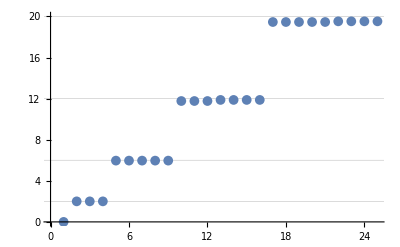

```mathematica
ListPlot[e8,PlotRange->{{0,25},{0,20}},GridLines->{{},{2,6,12,20}},PlotMarkers->{Automatic,10}]
```

```mathematica
Clear[e8data];
e8data=Riffle[Drop[Table[Table[n,{l,1,2n+1}],{n,0,25}]//Flatten,-(676-642)],e8]//Partition[#,2]&;
```

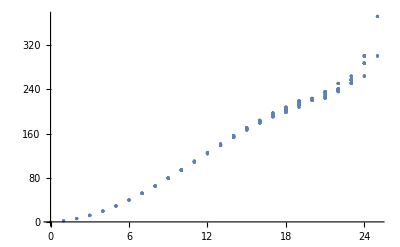

```mathematica
ListPlot[e8data]
```

```mathematica
timfirst=Join[{0},Table[Sum[2i+1,{i,0,j}],{j,0,25}]]
```

{0,1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676}

```mathematica
Clear[avg8data];
avg8data=Riffle[Table[i,{i,0,24}],Table[Mean[e8[[timfirst[[i]]+1;;timfirst[[i+1]]]]],{i,1,25}]]//Partition[#,2]&
```

{{0,-1.60427×10^-14},{1,2.},{2,5.96554},{3,11.8289},{4,19.4888},{5,28.8139},{6,39.6453},{7,51.7964},{8,65.0595},{9,79.2094},{10,94.0025},{11,109.185},{12,124.495},{13,139.662},{14,154.408},{15,168.447},{16,181.414},{17,193.024},{18,203.03},{19,214.494},{20,221.918},{21,231.61},{22,240.827},{23,255.895},{24,289.581}}

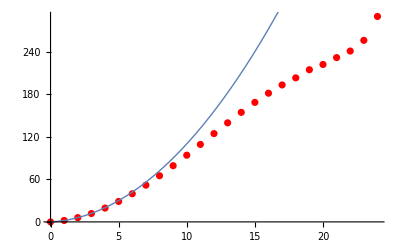

```mathematica
Show[ListPlot[avg8data,PlotStyle->Directive[Red,10]],Plot[x(x+1),{x,0,25},PlotStyle->Thin]]
```

#### s=48

```mathematica
Clear[e48];
e48=Eigenvalues[mxy]//Flatten//Reverse;
```

```mathematica
Length[e48]
```

23042

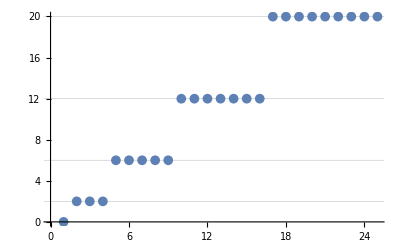

```mathematica
ListPlot[e48,PlotRange->{{0,25},{0,20}},GridLines->{{},{2,6,12,20}},PlotMarkers->{Automatic,10}]
```

```mathematica
Clear[e48data];
e48data=Riffle[Drop[Table[Table[n,{l,1,2n+1}],{n,0,25}]//Flatten,-(676-642)],e48]//Partition[#,2]&;
```

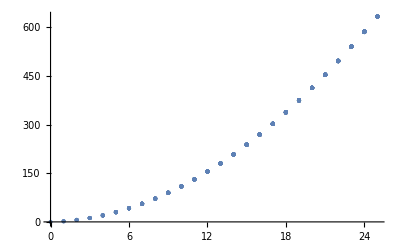

```mathematica
ListPlot[e48data]
```

```mathematica
timfirst=Join[{0},Table[Sum[2i+1,{i,0,j}],{j,0,27}]]
```

{0,1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784}

```mathematica
Clear[avg48data];
avg48data=Riffle[Table[i,{i,0,26}],Table[Mean[e48[[timfirst[[i]]+1;;timfirst[[i+1]]]]],{i,1,27}]]//Partition[#,2]&;
```

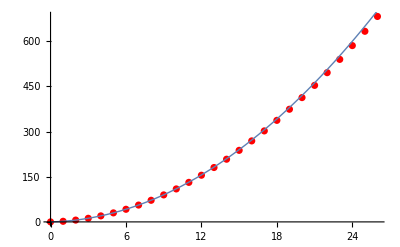

```mathematica
Show[ListPlot[avg48data,PlotStyle->Directive[Red,10]],Plot[x(x+1),{x,0,27},PlotStyle->Thin]]
```

### Data definitions

#### s=8

```mathematica
Clear[e8];
e8={-1.60427*10^-14,2.,2.,2.,5.96554,5.96554,5.96554,5.96554,5.96554,11.7684,11.7684,11.7684,11.8742,11.8742,11.8742,11.8742,19.4595,19.4595,19.4595,19.4595,19.4595,19.5254,19.5254,19.5254,19.5254,28.747,28.747,28.747,28.747,28.747,28.8266,28.8266,28.8266,28.9128,28.9128,28.9128,39.4892,39.4892,39.4892,39.4892,39.4892,39.6591,39.7482,39.7482,39.7482,39.7482,39.7638,39.7638,39.7638,51.6023,51.6023,51.6023,51.7697,51.7697,51.7697,51.7697,51.7697,51.8503,51.8503,51.8503,51.8503,51.9632,51.9632,51.9632,64.8162,64.8162,64.8162,64.8162,64.9273,64.9273,64.9273,64.9273,64.9273,65.1603,65.1603,65.1603,65.3259,65.3259,65.3259,65.3259,65.3259,78.7757,78.7757,78.7757,78.7757,78.9277,78.9277,78.9277,79.2407,79.2407,79.2407,79.2407,79.2407,79.4138,79.4138,79.4138,79.6621,79.6621,79.6621,79.6621,93.3294,93.4667,93.4667,93.4667,93.7175,93.7175,93.7175,93.7175,93.7175,93.8963,93.8963,93.8963,94.3878,94.3878,94.3878,94.3878,94.4992,94.4992,94.4992,94.4992,94.4992,108.443,108.443,108.443,108.443,108.617,108.617,108.617,108.872,108.872,108.872,108.872,108.872,109.563,109.563,109.563,109.563,109.563,109.761,109.761,109.761,110.056,110.056,110.056,123.496,123.496,123.496,123.496,123.752,123.752,123.752,123.752,123.752,124.068,124.068,124.068,124.919,124.919,124.919,124.919,124.919,125.087,125.087,125.087,125.087,125.564,125.564,125.564,125.791,138.34,138.34,138.34,138.654,138.654,138.654,138.654,138.654,138.875,138.875,138.875,138.875,140.154,140.154,140.154,140.157,140.157,140.157,140.157,140.434,140.434,140.434,140.434,140.434,141.274,141.274,141.274,152.877,152.877,152.877,152.877,152.877,153.229,153.229,153.229,153.307,153.307,153.307,153.307,154.745,154.745,154.745,154.745,154.745,155.001,155.001,155.001,155.001,155.101,155.101,155.101,156.302,156.302,156.302,156.302,156.302,166.649,166.649,166.649,166.649,166.649,166.707,166.707,166.707,167.15,167.15,167.15,167.475,168.454,168.454,168.454,168.547,168.547,168.547,168.547,169.166,169.166,169.166,169.166,169.166,170.249,170.249,170.249,170.861,170.861,170.861,170.861,179.202,179.202,179.202,179.202,179.202,179.868,179.868,179.868,179.868,180.01,180.01,180.01,180.8,181.223,181.223,181.223,181.352,181.352,181.352,181.902,181.902,181.902,181.902,181.902,183.305,183.305,183.305,183.305,183.979,183.979,183.979,183.979,183.979,190.372,190.372,190.372,190.746,190.746,190.746,190.746,190.746,190.954,190.954,190.954,190.954,191.079,191.079,191.079,192.361,192.361,192.361,192.361,192.361,193.178,193.178,193.178,194.005,194.005,194.005,194.005,197.042,197.042,197.042,197.042,197.042,197.125,197.125,197.125,198.368,198.368,198.368,198.368,198.368,198.586,198.586,198.586,201.388,201.388,201.388,201.388,201.779,201.779,201.779,201.779,201.837,201.837,201.837,203.113,203.113,203.113,205.162,205.162,205.162,205.162,205.162,206.248,206.248,206.248,206.248,207.669,207.669,207.669,207.669,207.752,207.752,207.752,207.752,207.752,211.635,211.635,211.635,211.635,211.635,211.639,211.639,211.639,211.639,212.062,212.062,212.062,212.807,212.807,212.807,212.807,212.807,215.914,215.914,215.914,216.537,217.247,217.247,217.247,217.247,217.247,217.861,217.861,217.861,218.644,218.644,218.644,218.644,218.644,219.878,219.878,219.878,219.878,220.032,220.032,220.032,220.703,220.703,220.703,220.703,220.902,220.902,220.902,221.233,221.233,221.233,221.233,221.233,221.68,222.089,222.089,222.089,222.379,222.379,222.379,222.379,222.379,222.653,222.653,222.653,222.653,222.653,222.767,222.767,222.767,223.623,223.623,223.623,223.623,223.623,223.632,223.951,223.951,223.951,223.951,224.476,224.476,224.476,226.217,226.217,226.217,226.797,226.797,226.797,226.797,229.952,229.952,229.952,229.952,229.952,232.914,232.914,232.914,234.723,234.723,234.723,234.741,234.741,234.741,234.741,235.527,235.527,235.527,235.739,235.739,235.739,235.739,235.835,235.835,235.835,235.835,235.835,235.917,235.917,235.917,236.032,236.032,236.032,236.032,236.032,236.473,236.473,236.473,236.473,237.663,237.663,237.663,239.095,239.095,239.095,239.095,239.095,239.197,239.197,239.197,239.197,239.994,239.994,239.994,239.994,239.994,240.434,240.434,240.434,240.573,240.981,240.981,240.981,240.981,240.981,241.189,241.189,241.189,250.781,250.781,250.781,250.781,250.781,250.852,250.852,250.852,250.866,250.866,250.866,250.866,250.866,251.064,251.064,251.064,251.064,251.26,251.26,251.26,251.269,251.269,251.269,251.269,256.23,256.23,256.23,256.23,256.522,256.522,256.522,256.522,256.522,257.411,257.411,257.411,257.411,257.726,257.726,257.726,257.917,257.917,257.917,257.917,257.917,258.486,258.486,258.486,263.626,263.877,263.877,263.877,264.065,264.065,264.065,264.065,264.065,264.117,264.117,264.117,287.203,287.203,287.203,287.245,287.245,287.245,287.245,287.245,287.265,287.265,287.265,287.285,287.285,287.285,287.285,287.361,287.361,287.361,287.361,287.361,287.384,287.384,287.384,287.384,300.491,300.491,300.491,300.491,300.491,300.502,300.502,300.502,300.502,300.502,300.503,300.503,300.503,300.535,300.535,300.535,300.535,300.598,300.598,300.598,300.598,300.605,300.605,300.605,372.124,372.124,372.124,372.124,372.124,372.124,372.124,372.124,372.125,372.125,372.125,372.126};
```

#### s=48

```mathematica
Clear[e48];
e48={-3.86172*10^-11,2.,2.,2.,5.99904,5.99904,5.99904,5.99904,5.99904,11.9934,11.9934,11.9934,11.9965,11.9965,11.9965,11.9965,19.9847,19.9847,19.9847,19.9847,19.9847,19.9867,19.9867,19.9867,19.9867,29.9643,29.9643,29.9643,29.9643,29.9643,29.9667,29.9667,29.9667,29.9695,29.9695,29.9695,41.9276,41.9276,41.9276,41.9276,41.9276,41.9328,41.9363,41.9363,41.9363,41.9363,41.9366,41.9366,41.9366,55.8723,55.8723,55.8723,55.8782,55.8782,55.8782,55.8782,55.8782,55.8812,55.8812,55.8812,55.8812,55.8841,55.8841,55.8841,71.7896,71.7896,71.7896,71.7896,71.7938,71.7938,71.7938,71.7938,71.7938,71.803,71.803,71.803,71.8072,71.8072,71.8072,71.8072,71.8072,89.6667,89.6667,89.6667,89.6667,89.6729,89.6729,89.6729,89.6863,89.6863,89.6863,89.6863,89.6863,89.6882,89.6882,89.6882,89.7001,89.7001,89.7001,89.7001,109.497,109.504,109.504,109.504,109.515,109.515,109.515,109.515,109.515,109.523,109.523,109.523,109.54,109.54,109.54,109.54,109.542,109.542,109.542,109.542,109.542,131.283,131.283,131.283,131.283,131.291,131.291,131.291,131.306,131.306,131.306,131.306,131.306,131.327,131.327,131.327,131.327,131.327,131.341,131.341,131.341,131.346,131.346,131.346,154.993,154.993,154.993,154.993,155.009,155.009,155.009,155.009,155.009,155.031,155.031,155.031,155.053,155.053,155.053,155.053,155.053,155.073,155.073,155.073,155.073,155.081,155.087,155.087,155.087,180.623,180.623,180.623,180.646,180.646,180.646,180.646,180.646,180.664,180.664,180.664,180.664,180.713,180.713,180.713,180.724,180.724,180.724,180.724,180.725,180.725,180.725,180.725,180.725,180.755,180.755,180.755,208.173,208.173,208.173,208.173,208.173,208.198,208.198,208.198,208.212,208.212,208.212,208.212,208.279,208.279,208.279,208.279,208.286,208.286,208.286,208.286,208.286,208.301,208.301,208.301,208.338,208.338,208.338,208.338,208.338,237.608,237.608,237.608,237.625,237.625,237.625,237.625,237.625,237.656,237.656,237.656,237.67,237.727,237.727,237.727,237.727,237.754,237.754,237.754,237.775,237.775,237.775,237.775,237.775,237.806,237.806,237.806,237.829,237.829,237.829,237.829,268.926,268.926,268.926,268.926,268.926,268.96,268.96,268.96,268.979,268.979,268.979,268.979,269.081,269.081,269.081,269.095,269.104,269.104,269.104,269.104,269.104,269.13,269.13,269.13,269.18,269.18,269.18,269.18,269.197,269.197,269.197,269.197,269.197,302.097,302.097,302.097,302.136,302.136,302.136,302.136,302.136,302.165,302.165,302.165,302.165,302.291,302.291,302.291,302.291,302.332,302.332,302.332,302.336,302.336,302.336,302.336,302.336,302.414,302.414,302.414,302.414,302.414,302.44,302.44,302.44,302.468,302.468,302.468,337.134,337.134,337.134,337.134,337.165,337.165,337.165,337.165,337.165,337.211,337.211,337.211,337.345,337.345,337.345,337.345,337.398,337.398,337.398,337.398,337.398,337.419,337.419,337.419,337.513,337.513,337.513,337.513,337.513,337.542,337.542,337.542,337.542,337.578,337.58,337.58,337.58,373.99,373.99,373.99,373.99,374.011,374.011,374.011,374.062,374.062,374.062,374.062,374.062,374.257,374.257,374.257,374.27,374.27,374.27,374.27,374.27,374.33,374.33,374.33,374.33,374.47,374.47,374.47,374.472,374.472,374.472,374.472,374.472,374.474,374.474,374.474,374.474,374.548,374.548,374.548,412.624,412.656,412.656,412.656,412.709,412.709,412.709,412.709,412.709,412.733,412.733,412.733,412.974,412.974,412.974,412.974,412.974,412.986,412.986,412.986,413.049,413.049,413.049,413.049,413.206,413.206,413.206,413.206,413.235,413.235,413.235,413.235,413.235,413.236,413.236,413.236,413.333,413.333,413.333,413.333,413.333,453.113,453.113,453.113,453.113,453.136,453.136,453.136,453.2,453.2,453.2,453.2,453.2,453.452,453.452,453.452,453.508,453.508,453.508,453.508,453.508,453.538,453.567,453.567,453.567,453.718,453.718,453.718,453.718,453.819,453.819,453.819,453.819,453.819,453.822,453.822,453.822,453.895,453.895,453.895,453.928,453.928,453.928,453.928,495.339,495.339,495.339,495.339,495.381,495.381,495.381,495.381,495.381,495.452,495.452,495.452,495.758,495.758,495.758,495.758,495.758,495.779,495.779,495.779,495.857,495.857,495.857,495.857,496.063,496.063,496.063,496.109,496.109,496.109,496.109,496.109,496.183,496.197,496.197,496.197,496.264,496.264,496.264,496.264,496.304,496.304,496.304,496.304,496.304,539.289,539.289,539.289,539.368,539.368,539.368,539.368,539.368,539.412,539.412,539.412,539.412,539.79,539.79,539.79,539.812,539.812,539.812,539.812,539.812,539.896,539.896,539.896,539.896,540.143,540.143,540.143,540.143,540.234,540.234,540.234,540.234,540.234,540.289,540.289,540.289,540.397,540.397,540.397,540.397,540.397,540.438,540.438,540.438,540.497,540.497,540.497,585.008,585.008,585.008,585.008,585.008,585.095,585.095,585.095,585.119,585.119,585.119,585.119,585.537,585.537,585.537,585.537,585.624,585.624,585.624,585.624,585.624,585.656,585.656,585.656,585.948,585.948,585.948,585.948,586.081,586.081,586.081,586.088,586.088,586.088,586.088,586.088,586.31,586.31,586.31,586.31,586.31,586.331,586.331,586.331,586.331,586.381,586.381,586.381,586.383,632.418,632.418,632.418,632.45,632.45,632.45,632.45,632.45,632.529,632.529,632.529,632.592,633.014,633.014,633.014,633.014,633.091,633.091,633.091,633.127,633.127,633.127,633.127,633.127,633.523,633.523,633.523,633.523,633.523,633.558,633.558,633.558,633.687,633.687,633.687,633.687,633.903,633.903,633.903,633.903,633.903,633.95,633.95,633.95,633.95,633.961,633.961,633.961,634.035,634.035,634.035,681.491,681.491,681.491,681.491,681.491,681.593,681.593,681.593,681.619,681.619,681.619,681.619,682.173,682.173,682.173,682.187,682.255,682.255,682.255,682.255,682.255,682.31,682.31,682.31,682.734,682.734,682.734,682.781,682.781,682.781,682.781,682.781,682.929,682.929,682.929,682.929,683.173,683.173,683.173,683.173,683.213,683.213,683.213,683.276,683.276,683.276,683.276,683.276,683.393,683.393,683.393,683.393,683.393,732.197,732.197,732.197,732.308,732.308,732.308,732.308,732.308,732.361,732.361,732.361,732.361,732.991,732.991,732.991,732.991,733.061,733.061,733.061,733.123,733.123,733.123,733.123,733.123,733.578,733.578,733.578,733.662,733.733,733.733,733.733,733.733,733.733,733.841,733.841,733.841,734.051,734.051,734.051,734.051,734.258,734.258,734.258,734.258,734.258,734.355,734.355,734.355,734.366,734.366,734.366,734.4,734.4,734.4,734.4,784.597,784.597,784.597,784.597,784.654,784.654,784.654,784.654,784.654,784.773,784.773,784.773,785.444,785.444,785.444,785.444,785.527,785.527,785.527,785.527,785.527,785.602,785.602,785.602,786.145,786.145,786.145,786.208,786.208,786.208,786.208,786.208,786.391,786.391,786.391,786.391,786.678,786.678,786.678,786.777,786.777,786.777,786.777,786.777,787.013,787.013,787.013,787.026,787.026,787.026,787.026,787.07,787.088,787.088,787.088,787.088,787.088,838.561,838.561,838.561,838.561,838.59,838.59,838.59,838.717,838.717,838.717,838.717,838.717,839.49,839.49,839.49,839.574,839.574,839.574,839.574,839.574,839.656,839.656,839.656,839.656,840.304,840.304,840.304,840.304,840.304,840.384,840.384,840.384,840.537,840.537,840.537,840.537,840.893,840.893,840.893,840.893,841.068,841.068,841.068,841.068,841.068,841.236,841.236,841.236,841.339,841.339,841.339,841.339,841.339,841.395,841.395,841.395,841.506,841.506,841.506,894.007,894.099,894.099,894.099,894.21,894.21,894.21,894.21,894.21,894.252,894.252,894.252,895.146,895.146,895.146,895.146,895.146,895.244,895.244,895.244,895.299,895.299,895.299,895.299,895.992,895.992,895.992,895.992,896.166,896.166,896.166,896.235,896.235,896.235,896.235,896.235,896.678,896.678,896.678,896.678,896.918,896.918,896.918,896.954,896.954,896.954,896.954,896.954,897.325,897.325,897.325,897.325,897.33,897.334,897.334,897.334,897.372,897.372,897.372,897.372,897.372,951.183,951.183,951.183,951.183,951.215,951.215,951.215,951.359,951.359,951.359,951.359,951.359,952.334,952.334,952.334,952.387,952.387,952.387,952.387,952.387,952.495,952.495,952.495,952.555,953.298,953.298,953.298,953.298,953.467,953.467,953.467,953.467,953.467,953.546,953.546,953.546,954.112,954.112,954.112,954.112,954.112,954.221,954.221,954.221,954.46,954.46,954.46,954.46,954.7,954.7,954.7,954.7,954.7,954.879,954.879,954.879,954.895,954.895,954.895,954.895,954.936,954.936,954.936,1009.78,1009.78,1009.78,1009.78,1009.86,1009.86,1009.86,1009.86,1009.86,1010.01,1010.01,1010.01,1011.04,1011.04,1011.04,1011.04,1011.04,1011.17,1011.17,1011.17,1011.21,1011.21,1011.21,1011.21,1012.13,1012.13,1012.13,1012.25,1012.25,1012.25,1012.25,1012.25,1012.32,1012.37,1012.37,1012.37,1012.97,1012.97,1012.97,1013.13,1013.13,1013.13,1013.13,1013.13,1013.38,1013.38,1013.38,1013.38,1013.73,1013.73,1013.73,1013.73,1013.76,1013.76,1013.76,1013.9,1013.9,1013.9,1013.9,1013.9,1014.1,1014.1,1014.1,1014.1,1014.1,1069.82,1069.82,1069.82,1069.98,1069.98,1069.98,1069.98,1069.98,1070.05,1070.05,1070.05,1070.05,1071.22,1071.22,1071.22,1071.35,1071.35,1071.35,1071.35,1071.35,1071.42,1071.42,1071.42,1071.42,1072.45,1072.45,1072.45,1072.45,1072.64,1072.64,1072.64,1072.65,1072.65,1072.65,1072.65,1072.65,1073.34,1073.34,1073.34,1073.36,1073.67,1073.67,1073.67,1073.67,1073.67,1073.86,1073.86,1073.86,1074.06,1074.06,1074.06,1074.06,1074.48,1074.48,1074.48,1074.48,1074.48,1074.56,1074.56,1074.56,1074.56,1074.56,1074.56,1074.56,1074.76,1074.76,1074.76,1131.4,1131.4,1131.4,1131.4,1131.4,1131.57,1131.57,1131.57,1131.61,1131.61,1131.61,1131.61,1132.92,1132.92,1132.92,1132.92,1133.,1133.,1133.,1133.,1133.,1133.15,1133.15,1133.15,1134.25,1134.25,1134.25,1134.25,1134.43,1134.43,1134.43,1134.43,1134.43,1134.46,1134.46,1134.46,1135.2,1135.2,1135.2,1135.48,1135.48,1135.48,1135.48,1135.48,1135.81,1135.81,1135.81,1135.81,1136.1,1136.1,1136.1,1136.28,1136.28,1136.28,1136.28,1136.28,1136.64,1136.64,1136.64,1136.64,1136.72,1136.72,1136.72,1136.72,1136.72,1136.81,1136.81,1136.81,1136.99,1194.39,1194.39,1194.39,1194.44,1194.44,1194.44,1194.44,1194.44,1194.59,1194.59,1194.59,1194.71,1196.02,1196.02,1196.02,1196.02,1196.07,1196.07,1196.07,1196.22,1196.22,1196.22,1196.22,1196.22,1197.52,1197.52,1197.52,1197.57,1197.57,1197.57,1197.57,1197.57,1197.73,1197.73,1197.73,1197.73,1198.59,1198.59,1198.59,1198.59,1198.59,1198.94,1198.94,1198.94,1199.14,1199.14,1199.14,1199.14,1199.57,1199.57,1199.57,1199.57,1199.83,1199.83,1199.83,1199.83,1199.83,1200.08,1200.08,1200.08,1200.28,1200.28,1200.28,1200.28,1200.28,1200.33,1200.33,1200.33,1200.61,1200.61,1200.61,1258.74,1258.74,1258.74,1258.74,1258.74,1258.93,1258.93,1258.93,1258.97,1258.97,1258.97,1258.97,1260.42,1260.52,1260.52,1260.52,1260.66,1260.66,1260.66,1260.66,1260.66,1260.72,1260.72,1260.72,1262.16,1262.16,1262.16,1262.16,1262.16,1262.24,1262.24,1262.24,1262.37,1262.37,1262.37,1262.37,1263.32,1263.32,1263.32,1263.32,1263.55,1263.55,1263.55,1263.91,1263.91,1263.91,1263.91,1263.91,1264.38,1264.38,1264.38,1264.38,1264.81,1264.81,1264.81,1264.82,1264.82,1264.82,1264.82,1264.82,1265.21,1265.24,1265.24,1265.24,1265.38,1265.38,1265.38,1265.38,1265.61,1265.61,1265.61,1265.61,1265.61,1324.42,1324.42,1324.42,1324.61,1324.61,1324.61,1324.61,1324.61,1324.7,1324.7,1324.7,1324.7,1326.39,1326.39,1326.39,1326.39,1326.44,1326.44,1326.44,1326.61,1326.61,1326.61,1326.61,1326.61,1328.15,1328.15,1328.15,1328.24,1328.24,1328.24,1328.24,1328.24,1328.38,1328.38,1328.38,1328.4,1329.51,1329.51,1329.51,1329.51,1329.74,1329.74,1329.74,1329.74,1329.74,1330.15,1330.15,1330.15,1330.74,1330.74,1330.74,1330.74,1330.74,1330.9,1330.9,1330.9,1331.35,1331.35,1331.35,1331.35,1331.53,1331.53,1331.53,1331.53,1331.53,1331.71,1331.71,1331.71,1332.04,1332.04,1332.04,1332.04,1332.12,1332.12,1332.12,1391.54,1391.54,1391.54,1391.54,1391.64,1391.64,1391.64,1391.64,1391.64,1391.84,1391.84,1391.84,1393.59,1393.59,1393.59,1393.59,1393.68,1393.68,1393.68,1393.68,1393.68,1393.87,1393.87,1393.87,1395.52,1395.52,1395.52,1395.52,1395.52,1395.64,1395.64,1395.64,1395.74,1395.74,1395.74,1395.74,1397.03,1397.03,1397.03,1397.19,1397.19,1397.19,1397.19,1397.19,1397.42,1397.42,1397.42,1397.67,1398.28,1398.28,1398.28,1398.55,1398.55,1398.55,1398.55,1398.55,1398.87,1398.87,1398.87,1398.87,1399.39,1399.39,1399.39,1399.47,1399.47,1399.47,1399.47,1399.51,1399.51,1399.51,1399.51,1399.51,1400.07,1400.07,1400.07,1400.07,1400.07,1459.89,1459.89,1459.89,1459.89,1459.94,1459.94,1459.94,1460.15,1460.15,1460.15,1460.15,1460.15,1462.03,1462.03,1462.03,1462.22,1462.22,1462.22,1462.22,1462.22,1462.32,1462.32,1462.32,1462.32,1464.14,1464.14,1464.14,1464.27,1464.27,1464.27,1464.27,1464.27,1464.4,1464.4,1464.4,1464.4,1465.85,1465.85,1465.85,1465.85,1466.14,1466.14,1466.14,1466.14,1466.14,1466.21,1466.21,1466.21,1466.94,1467.18,1467.18,1467.18,1467.71,1467.71,1467.71,1467.71,1467.71,1467.96,1467.96,1467.96,1468.1,1468.1,1468.1,1468.1,1468.75,1468.75,1468.75,1468.75,1468.87,1468.87,1468.87,1468.87,1468.87,1468.87,1468.87,1468.87,1469.43,1469.43,1469.43,1529.35,1529.51,1529.51,1529.51,1529.69,1529.69,1529.69,1529.69,1529.69,1529.76,1529.76,1529.76,1531.85,1531.85,1531.85,1531.85,1531.85,1532.05,1532.05,1532.05,1532.1,1532.1,1532.1,1532.1,1534.1,1534.1,1534.1,1534.1,1534.22,1534.22,1534.22,1534.22,1534.22,1534.37,1534.37,1534.37,1535.97,1535.97,1535.97,1535.97,1536.24,1536.24,1536.24,1536.29,1536.29,1536.29,1536.29,1536.29,1537.11,1537.11,1537.11,1537.8,1537.8,1537.8,1537.8,1537.8,1538.34,1538.34,1538.34,1538.34,1538.52,1538.52,1538.52,1538.78,1538.78,1538.78,1538.78,1538.78,1539.32,1539.32,1539.32,1539.32,1539.47,1539.47,1539.47,1539.47,1539.47,1539.82,1539.82,1539.82,1540.17,1600.35,1600.35,1600.35,1600.35,1600.4,1600.4,1600.4,1600.63,1600.63,1600.63,1600.63,1600.63,1602.87,1602.87,1602.87,1602.94,1602.94,1602.94,1602.94,1602.94,1603.11,1603.11,1603.11,1603.25,1605.26,1605.26,1605.26,1605.26,1605.35,1605.35,1605.35,1605.51,1605.51,1605.51,1605.51,1605.51,1607.43,1607.43,1607.43,1607.43,1607.43,1607.45,1607.45,1607.45,1607.71,1607.71,1607.71,1607.71,1608.68,1608.68,1608.68,1608.68,1608.68,1609.54,1609.54,1609.54,1609.75,1609.75,1609.75,1609.75,1610.32,1610.32,1610.32,1610.32,1610.53,1610.53,1610.53,1610.53,1610.53,1610.77,1610.77,1610.77,1611.3,1611.3,1611.3,1611.33,1611.33,1611.33,1611.33,1611.33,1611.93,1611.93,1611.93,1672.38,1672.38,1672.38,1672.38,1672.49,1672.49,1672.49,1672.49,1672.49,1672.73,1672.73,1672.73,1675.05,1675.05,1675.05,1675.05,1675.05,1675.27,1675.27,1675.27,1675.32,1675.32,1675.32,1675.32,1677.55,1677.63,1677.63,1677.63,1677.8,1677.8,1677.8,1677.8,1677.8,1677.88,1677.88,1677.88,1679.98,1679.98,1679.98,1679.98,1679.98,1680.01,1680.01,1680.01,1680.27,1680.27,1680.27,1680.27,1681.36,1681.36,1681.36,1681.36,1681.66,1681.66,1681.66,1682.6,1682.6,1682.6,1682.6,1682.6,1682.96,1682.96,1682.96,1682.96,1683.57,1683.57,1683.57,1683.57,1683.57,1683.71,1683.71,1683.71,1683.86,1683.96,1683.96,1683.96,1684.43,1684.43,1684.43,1684.43,1684.94,1684.94,1684.94,1684.94,1684.94,1745.48,1745.48,1745.48,1745.73,1745.73,1745.73,1745.73,1745.73,1745.85,1745.85,1745.85,1745.85,1748.35,1748.35,1748.35,1748.58,1748.58,1748.58,1748.58,1748.58,1748.68,1748.68,1748.68,1748.68,1751.17,1751.17,1751.17,1751.17,1751.25,1751.25,1751.25,1751.43,1751.43,1751.43,1751.43,1751.43,1753.63,1753.63,1753.63,1753.8,1753.8,1753.8,1753.8,1753.8,1753.9,1753.98,1753.98,1753.98,1755.35,1755.35,1755.35,1755.35,1755.62,1755.62,1755.62,1755.62,1755.62,1756.75,1756.75,1756.75,1757.2,1757.2,1757.2,1757.2,1757.2,1757.32,1757.32,1757.32,1758.11,1758.11,1758.11,1758.11,1758.16,1758.16,1758.16,1758.16,1758.16,1758.24,1758.24,1758.24,1759.15,1759.15,1759.15,1759.15,1759.3,1759.3,1759.3,1819.84,1819.84,1819.84,1819.84,1819.84,1820.1,1820.1,1820.1,1820.16,1820.16,1820.16,1820.16,1822.91,1822.91,1822.91,1822.91,1823.02,1823.02,1823.02,1823.02,1823.02,1823.26,1823.26,1823.26,1825.83,1825.83,1825.83,1825.83,1825.95,1825.95,1825.95,1825.95,1825.95,1826.15,1826.15,1826.15,1828.56,1828.56,1828.56,1828.56,1828.56,1828.64,1828.64,1828.64,1828.83,1828.83,1828.83,1828.83,1830.44,1830.44,1830.44,1830.65,1830.65,1830.65,1830.65,1830.65,1830.95,1830.95,1830.95,1831.95,1832.42,1832.42,1832.42,1832.67,1832.67,1832.67,1832.67,1832.67,1832.94,1832.94,1832.94,1832.94,1833.72,1833.72,1833.72,1833.73,1833.73,1833.73,1833.73,1833.73,1834.08,1834.08,1834.08,1834.08,1834.91,1834.91,1834.91,1834.91,1834.91,1895.26,1895.26,1895.26,1895.34,1895.34,1895.34,1895.34,1895.34,1895.56,1895.56,1895.56,1895.74,1898.48,1898.48,1898.48,1898.48,1898.53,1898.53,1898.53,1898.78,1898.78,1898.78,1898.78,1898.78,1901.52,1901.52,1901.52,1901.73,1901.73,1901.73,1901.73,1901.73,1901.85,1901.85,1901.85,1901.85,1904.49,1904.49,1904.49,1904.58,1904.58,1904.58,1904.58,1904.58,1904.78,1904.78,1904.78,1904.78,1906.62,1906.62,1906.62,1906.62,1907.01,1907.01,1907.01,1907.01,1907.01,1907.13,1907.13,1907.13,1907.81,1908.72,1908.72,1908.72,1909.32,1909.32,1909.32,1909.32,1909.32,1909.52,1909.52,1909.52,1909.6,1909.6,1909.6,1909.6,1910.41,1910.41,1910.41,1910.41,1910.83,1910.83,1910.83,1910.95,1910.95,1910.95,1910.95,1910.95,1911.82,1911.82,1911.82,1971.66,1971.66,1971.66,1971.66,1971.66,1971.94,1971.94,1971.94,1972.,1972.,1972.,1972.,1974.92,1975.1,1975.1,1975.1,1975.3,1975.3,1975.3,1975.3,1975.3,1975.38,1975.38,1975.38,1978.38,1978.38,1978.38,1978.38,1978.38,1978.6,1978.6,1978.6,1978.67,1978.67,1978.67,1978.67,1981.48,1981.48,1981.48,1981.48,1981.67,1981.67,1981.67,1981.67,1981.67,1981.8,1981.8,1981.8,1983.91,1983.91,1983.91,1983.91,1984.22,1984.22,1984.22,1984.38,1984.38,1984.38,1984.38,1984.38,1985.14,1985.14,1985.14,1986.58,1986.58,1986.58,1986.58,1986.58,1987.28,1987.28,1987.28,1987.28,1987.29,1987.29,1987.29,1987.52,1987.52,1987.52,1987.52,1987.52,1988.43,1988.43,1988.43,1988.43,1988.71,1988.71,1988.71,1988.71,1988.71,1989.36,1989.36,1989.36,1989.92,2049.03,2049.03,2049.03,2049.31,2049.31,2049.31,2049.31,2049.31,2049.45,2049.45,2049.45,2049.45,2052.73,2052.73,2052.73,2052.73,2052.79,2052.79,2052.79,2053.05,2053.05,2053.05,2053.05,2053.05,2056.22,2056.22,2056.22,2056.3,2056.3,2056.3,2056.3,2056.3,2056.5,2056.5,2056.5,2056.65,2059.51,2059.51,2059.51,2059.51,2059.67,2059.67,2059.67,2059.8,2059.8,2059.8,2059.8,2059.8,2062.3,2062.3,2062.3,2062.3,2062.3,2062.43,2062.43,2062.43,2062.74,2062.74,2062.74,2062.74,2063.69,2063.69,2063.69,2063.69,2063.69,2065.4,2065.4,2065.4,2065.54,2065.54,2065.54,2065.54,2066.32,2066.32,2066.32,2066.32,2066.32,2066.41,2066.41,2066.41,2066.41,2066.48,2066.48,2066.48,2067.53,2067.53,2067.53,2067.69,2067.69,2067.69,2067.69,2067.69,2068.62,2068.62,2068.62,2127.53,2127.53,2127.53,2127.53,2127.67,2127.67,2127.67,2127.67,2127.67,2127.96,2127.96,2127.96,2131.33,2131.33,2131.33,2131.33,2131.46,2131.46,2131.46,2131.46,2131.46,2131.73,2131.73,2131.73,2135.,2135.,2135.,2135.,2135.,2135.24,2135.24,2135.24,2135.31,2135.31,2135.31,2135.31,2138.52,2138.52,2138.52,2138.52,2138.72,2138.72,2138.72,2138.72,2138.72,2138.84,2138.84,2138.84,2141.59,2141.59,2141.59,2141.64,2141.64,2141.64,2141.64,2141.64,2142.02,2142.02,2142.02,2142.02,2143.11,2143.11,2143.11,2143.11,2143.48,2143.48,2143.48,2145.34,2145.34,2145.34,2145.34,2145.34,2145.49,2145.49,2145.49,2145.49,2146.32,2146.36,2146.36,2146.36,2146.36,2146.36,2146.51,2146.51,2146.51,2146.69,2146.69,2146.69,2147.52,2147.52,2147.52,2147.52,2148.42,2148.42,2148.42,2148.42,2148.42,2206.87,2206.87,2206.87,2206.87,2206.93,2206.93,2206.93,2207.24,2207.24,2207.24,2207.24,2207.24,2210.77,2210.77,2210.77,2211.05,2211.05,2211.05,2211.05,2211.05,2211.18,2211.18,2211.18,2211.18,2214.68,2214.68,2214.68,2214.93,2214.93,2214.93,2214.93,2214.93,2215.06,2215.06,2215.06,2215.06,2218.47,2218.47,2218.47,2218.47,2218.62,2218.62,2218.62,2218.78,2218.78,2218.78,2218.78,2218.78,2221.71,2221.71,2221.71,2221.96,2221.97,2221.97,2221.97,2221.97,2221.97,2222.2,2222.2,2222.2,2223.68,2223.68,2223.68,2223.68,2223.97,2223.97,2223.97,2223.97,2223.97,2226.29,2226.29,2226.29,2226.39,2226.39,2226.39,2226.39,2226.39,2226.42,2226.42,2226.42,2227.39,2227.39,2227.39,2227.56,2227.56,2227.56,2227.56,2227.56,2227.67,2227.67,2227.67,2227.67,2229.15,2229.15,2229.15,2229.15,2229.38,2229.38,2229.38,2286.88,2287.09,2287.09,2287.09,2287.35,2287.35,2287.35,2287.35,2287.35,2287.44,2287.44,2287.44,2291.27,2291.27,2291.27,2291.27,2291.27,2291.56,2291.56,2291.56,2291.62,2291.62,2291.62,2291.62,2295.4,2295.4,2295.4,2295.4,2295.53,2295.53,2295.53,2295.53,2295.53,2295.79,2295.79,2295.79,2299.33,2299.33,2299.33,2299.33,2299.51,2299.51,2299.51,2299.51,2299.51,2299.69,2299.69,2299.69,2302.97,2302.97,2302.97,2302.97,2302.97,2302.97,2302.97,2302.97,2303.29,2303.29,2303.29,2303.29,2305.11,2305.11,2305.11,2305.34,2305.34,2305.34,2305.34,2305.34,2305.66,2305.66,2305.66,2307.99,2308.26,2308.26,2308.26,2308.28,2308.28,2308.28,2308.28,2308.28,2308.39,2308.39,2308.39,2308.39,2309.39,2309.39,2309.39,2309.39,2309.39,2309.57,2309.57,2309.57,2310.33,2310.33,2310.33,2310.33,2311.39,2311.39,2311.39,2311.39,2311.39,2368.17,2368.17,2368.17,2368.17,2368.24,2368.24,2368.24,2368.56,2368.56,2368.56,2368.56,2368.56,2372.58,2372.58,2372.58,2372.68,2372.68,2372.68,2372.68,2372.68,2372.92,2372.92,2372.92,2373.12,2376.89,2376.89,2376.89,2376.89,2376.96,2376.96,2376.96,2377.23,2377.23,2377.23,2377.23,2377.23,2381.01,2381.01,2381.01,2381.21,2381.21,2381.21,2381.21,2381.21,2381.38,2381.38,2381.38,2381.38,2384.94,2384.94,2384.94,2384.95,2384.95,2384.95,2384.95,2384.95,2385.26,2385.26,2385.26,2385.26,2387.38,2387.38,2387.38,2387.38,2387.86,2387.86,2387.86,2387.86,2387.86,2387.94,2387.94,2387.94,2388.6,2390.75,2390.75,2390.75,2391.14,2391.14,2391.14,2391.23,2391.23,2391.23,2391.23,2391.23,2391.24,2391.24,2391.24,2391.24,2392.25,2392.25,2392.25,2392.25,2393.17,2393.17,2393.17,2393.37,2393.37,2393.37,2393.37,2393.37,2394.56,2394.56,2394.56,2450.06,2450.06,2450.06,2450.06,2450.21,2450.21,2450.21,2450.21,2450.21,2450.54,2450.54,2450.54,2454.65,2454.65,2454.65,2454.65,2454.65,2454.96,2454.96,2454.96,2455.03,2455.03,2455.03,2455.03,2459.03,2459.21,2459.21,2459.21,2459.44,2459.44,2459.44,2459.44,2459.44,2459.53,2459.53,2459.53,2463.59,2463.59,2463.59,2463.59,2463.59,2463.81,2463.81,2463.81,2463.91,2463.91,2463.91,2463.91,2467.63,2467.63,2467.63,2467.63,2467.93,2467.93,2467.93,2467.93,2467.93,2467.99,2467.99,2467.99,2470.57,2470.57,2470.57,2470.57,2470.91,2470.91,2470.91,2471.14,2471.14,2471.14,2471.14,2471.14,2471.79,2471.79,2471.79,2474.45,2474.45,2474.45,2474.45,2474.45,2475.,2475.,2475.,2475.03,2475.03,2475.03,2475.03,2475.03,2475.13,2475.13,2475.13,2475.13,2476.59,2476.59,2476.59,2476.59,2477.03,2477.03,2477.03,2477.03,2477.03,2477.94,2477.94,2477.94,2478.73,2532.6,2532.6,2532.6,2532.94,2532.94,2532.94,2532.94,2532.94,2533.1,2533.1,2533.1,2533.1,2537.45,2537.45,2537.45,2537.76,2537.76,2537.76,2537.76,2537.76,2537.91,2537.91,2537.91,2537.91,2542.3,2542.3,2542.3,2542.3,2542.38,2542.38,2542.38,2542.66,2542.66,2542.66,2542.66,2542.66,2546.91,2546.91,2546.91,2547.01,2547.01,2547.01,2547.01,2547.01,2547.24,2547.24,2547.24,2547.37,2551.2,2551.2,2551.2,2551.2,2551.49,2551.49,2551.49,2551.55,2551.55,2551.55,2551.55,2551.55,2554.6,2554.6,2554.6,2554.6,2554.6,2554.82,2554.82,2554.82,2555.15,2555.15,2555.15,2555.15,2556.02,2556.02,2556.02,2556.02,2556.02,2558.98,2558.98,2558.98,2558.99,2558.99,2558.99,2558.99,2559.65,2559.65,2559.65,2559.67,2559.67,2559.67,2559.67,2559.67,2560.3,2560.3,2560.3,2560.3,2561.5,2561.5,2561.5,2561.77,2561.77,2561.77,2561.77,2561.77,2563.07,2563.07,2563.07,2616.08,2616.08,2616.08,2616.08,2616.08,2616.42,2616.42,2616.42,2616.5,2616.5,2616.5,2616.5,2621.17,2621.17,2621.17,2621.17,2621.32,2621.32,2621.32,2621.32,2621.32,2621.64,2621.64,2621.64,2626.13,2626.13,2626.13,2626.13,2626.28,2626.28,2626.28,2626.28,2626.28,2626.57,2626.57,2626.57,2630.96,2630.96,2630.96,2630.96,2630.96,2631.2,2631.2,2631.2,2631.3,2631.3,2631.3,2631.3,2635.52,2635.52,2635.52,2635.67,2635.75,2635.75,2635.75,2635.75,2635.75,2635.93,2635.93,2635.93,2639.27,2639.27,2639.27,2639.39,2639.39,2639.39,2639.39,2639.39,2639.86,2639.86,2639.86,2639.86,2640.87,2640.87,2640.87,2640.87,2641.28,2641.28,2641.28,2644.34,2644.34,2644.34,2644.34,2644.34,2644.35,2644.35,2644.35,2644.35,2644.91,2645.24,2645.24,2645.24,2645.63,2645.63,2645.63,2645.63,2645.63,2646.06,2646.06,2646.06,2646.98,2646.98,2646.98,2646.98,2648.31,2648.31,2648.31,2648.31,2648.31,2700.19,2700.19,2700.19,2700.3,2700.3,2700.3,2700.3,2700.3,2700.59,2700.59,2700.59,2700.83,2705.47,2705.47,2705.47,2705.47,2705.54,2705.54,2705.54,2705.87,2705.87,2705.87,2705.87,2705.87,2710.56,2710.56,2710.56,2710.86,2710.86,2710.86,2710.86,2710.86,2711.,2711.,2711.,2711.,2715.66,2715.66,2715.66,2715.9,2715.9,2715.9,2715.9,2715.9,2716.06,2716.06,2716.06,2716.06,2720.53,2720.53,2720.53,2720.53,2720.79,2720.79,2720.79,2720.88,2720.88,2720.88,2720.88,2720.88,2724.56,2724.56,2724.56,2724.79,2724.92,2724.92,2724.92,2724.92,2724.92,2725.18,2725.18,2725.18,2726.68,2726.68,2726.68,2726.68,2726.96,2726.96,2726.96,2726.96,2726.96,2730.46,2730.46,2730.46,2730.49,2730.49,2730.49,2730.49,2730.49,2730.82,2730.82,2730.82,2731.55,2731.55,2731.55,2732.03,2732.03,2732.03,2732.03,2732.03,2732.25,2732.25,2732.25,2732.25,2734.2,2734.2,2734.2,2734.2,2734.53,2734.53,2734.53,2784.89,2784.89,2784.89,2784.89,2784.89,2785.25,2785.25,2785.25,2785.33,2785.33,2785.33,2785.33,2790.19,2790.42,2790.42,2790.42,2790.69,2790.69,2790.69,2790.69,2790.69,2790.8,2790.8,2790.8,2795.81,2795.81,2795.81,2795.81,2795.81,2796.12,2796.12,2796.12,2796.19,2796.19,2796.19,2796.19,2801.14,2801.14,2801.14,2801.14,2801.3,2801.3,2801.3,2801.3,2801.3,2801.56,2801.56,2801.56,2806.2,2806.2,2806.2,2806.2,2806.46,2806.46,2806.46,2806.46,2806.46,2806.6,2806.6,2806.6,2810.7,2810.7,2810.7,2810.81,2810.81,2810.81,2810.81,2810.81,2811.16,2811.16,2811.16,2811.16,2813.09,2813.09,2813.09,2813.32,2813.32,2813.32,2813.32,2813.32,2813.63,2813.63,2813.63,2817.37,2817.37,2817.37,2817.37,2817.41,2817.41,2817.41,2817.41,2817.41,2817.88,2817.88,2817.88,2817.88,2818.7,2818.7,2818.7,2818.7,2818.7,2819.03,2819.03,2819.03,2820.28,2820.28,2820.28,2820.28,2821.55,2821.55,2821.55,2821.55,2821.55,2870.14,2870.14,2870.14,2870.5,2870.5,2870.5,2870.5,2870.5,2870.67,2870.67,2870.67,2870.67,2875.98,2875.98,2875.98,2875.98,2876.06,2876.06,2876.06,2876.4,2876.4,2876.4,2876.4,2876.4,2881.63,2881.63,2881.63,2881.73,2881.73,2881.73,2881.73,2881.73,2881.99,2881.99,2881.99,2882.2,2887.16,2887.16,2887.16,2887.16,2887.26,2887.26,2887.26,2887.53,2887.53,2887.53,2887.53,2887.53,2892.5,2892.5,2892.5,2892.65,2892.65,2892.65,2892.65,2892.65,2892.89,2892.89,2892.89,2892.89,2897.35,2897.35,2897.35,2897.35,2897.35,2897.45,2897.45,2897.45,2897.77,2897.77,2897.77,2897.77,2900.08,2900.08,2900.08,2900.08,2900.62,2900.62,2900.62,2900.62,2900.62,2900.64,2900.64,2900.64,2901.3,2904.87,2904.87,2904.87,2905.03,2905.03,2905.03,2905.03,2905.22,2905.22,2905.22,2905.44,2905.44,2905.44,2905.44,2905.44,2906.3,2906.3,2906.3,2906.3,2907.85,2907.85,2907.85,2908.1,2908.1,2908.1,2908.1,2908.1,2909.61,2909.61,2909.61,2956.17,2956.17,2956.17,2956.17,2956.34,2956.34,2956.34,2956.34,2956.34,2956.72,2956.72,2956.72,2962.11,2962.11,2962.11,2962.11,2962.28,2962.28,2962.28,2962.28,2962.28,2962.62,2962.62,2962.62,2967.96,2967.96,2967.96,2967.96,2967.96,2968.28,2968.28,2968.28,2968.35,2968.35,2968.35,2968.35,2973.6,2973.76,2973.76,2973.76,2974.01,2974.01,2974.01,2974.01,2974.01,2974.12,2974.12,2974.12,2979.38,2979.38,2979.38,2979.38,2979.38,2979.56,2979.56,2979.56,2979.73,2979.73,2979.73,2979.73,2984.41,2984.41,2984.41,2984.41,2984.81,2984.81,2984.81,2984.85,2984.85,2984.85,2984.85,2984.85,2987.8,2987.8,2987.8,2987.8,2988.14,2988.14,2988.14,2988.41,2988.41,2988.41,2988.41,2988.41,2988.98,2988.98,2988.98,2993.23,2993.23,2993.23,2993.23,2993.23,2993.33,2993.33,2993.33,2993.33,2993.33,2993.56,2993.56,2993.56,2993.77,2993.77,2993.77,2993.77,2995.7,2995.7,2995.7,2995.7,2996.29,2996.29,2996.29,2996.29,2996.29,2997.42,2997.42,2997.42,2998.44,3042.6,3042.6,3042.6,3042.6,3042.68,3042.68,3042.68,3043.06,3043.06,3043.06,3043.06,3043.06,3048.65,3048.65,3048.65,3049.,3049.,3049.,3049.,3049.,3049.17,3049.17,3049.17,3049.17,3054.77,3054.77,3054.77,3055.09,3055.09,3055.09,3055.09,3055.09,3055.25,3055.25,3055.25,3055.25,3060.89,3060.89,3060.89,3060.89,3060.99,3060.99,3060.99,3061.27,3061.27,3061.27,3061.27,3061.27,3066.74,3066.74,3066.74,3066.87,3066.87,3066.87,3066.87,3066.87,3067.12,3067.12,3067.12,3067.19,3072.11,3072.11,3072.11,3072.11,3072.51,3072.51,3072.51,3072.51,3072.51,3072.57,3072.57,3072.57,3076.07,3076.07,3076.07,3076.07,3076.07,3076.36,3076.36,3076.36,3076.69,3076.69,3076.69,3076.69,3077.47,3077.47,3077.47,3077.47,3077.47,3081.94,3081.94,3081.94,3081.94,3082.04,3082.04,3082.04,3082.14,3082.14,3082.14,3082.4,3082.4,3082.4,3082.4,3082.4,3083.73,3083.73,3083.73,3083.73,3085.,3085.,3085.,3085.34,3085.34,3085.34,3085.34,3085.34,3086.99,3086.99,3086.99,3129.25,3129.52,3129.52,3129.52,3129.83,3129.83,3129.83,3129.83,3129.83,3129.95,3129.95,3129.95,3135.88,3135.88,3135.88,3135.88,3135.88,3136.24,3136.24,3136.24,3136.31,3136.31,3136.31,3136.31,3142.25,3142.25,3142.25,3142.25,3142.41,3142.41,3142.41,3142.41,3142.41,3142.74,3142.74,3142.74,3148.5,3148.5,3148.5,3148.5,3148.67,3148.67,3148.67,3148.67,3148.67,3148.96,3148.96,3148.96,3154.62,3154.62,3154.62,3154.62,3154.62,3154.84,3154.84,3154.84,3154.99,3154.99,3154.99,3154.99,3160.3,3160.3,3160.3,3160.56,3160.56,3160.56,3160.56,3160.56,3160.68,3160.82,3160.82,3160.82,3164.73,3164.73,3164.73,3164.9,3164.9,3164.9,3164.9,3164.9,3165.43,3165.43,3165.43,3165.43,3166.34,3166.34,3166.34,3166.34,3166.79,3166.79,3166.79,3171.25,3171.25,3171.25,3171.25,3171.27,3171.27,3171.27,3171.27,3171.27,3171.41,3171.9,3171.9,3171.9,3173.08,3173.08,3173.08,3173.08,3173.08,3173.48,3173.48,3173.48,3174.5,3174.5,3174.5,3174.5,3176.25,3176.25,3176.25,3176.25,3176.25,3216.88,3216.88,3216.88,3216.88,3216.96,3216.96,3216.96,3217.35,3217.35,3217.35,3217.35,3217.35,3223.49,3223.49,3223.49,3223.61,3223.61,3223.61,3223.61,3223.61,3223.9,3223.9,3223.9,3224.16,3230.07,3230.07,3230.07,3230.07,3230.14,3230.14,3230.14,3230.48,3230.48,3230.48,3230.48,3230.48,3236.47,3236.47,3236.47,3236.77,3236.77,3236.77,3236.77,3236.77,3236.93,3236.93,3236.93,3236.93,3242.88,3242.88,3242.88,3243.1,3243.1,3243.1,3243.1,3243.1,3243.3,3243.3,3243.3,3243.3,3248.91,3248.91,3248.91,3248.91,3249.31,3249.31,3249.31,3249.31,3249.31,3249.32,3249.32,3249.32,3253.76,3253.76,3253.76,3253.94,3254.19,3254.19,3254.19,3254.19,3254.19,3254.46,3254.46,3254.46,3255.97,3255.97,3255.97,3255.97,3256.23,3256.23,3256.23,3256.23,3256.23,3261.08,3261.08,3261.08,3261.12,3261.12,3261.12,3261.12,3261.12,3261.51,3261.51,3261.51,3262.73,3262.73,3262.73,3263.15,3263.15,3263.15,3263.15,3263.15,3263.42,3263.42,3263.42,3263.42,3265.87,3265.87,3265.87,3265.87,3266.29,3266.29,3266.29,3304.64,3304.64,3304.64,3304.64,3304.82,3304.82,3304.82,3304.82,3304.82,3305.22,3305.22,3305.22,3311.44,3311.44,3311.44,3311.44,3311.44,3311.81,3311.81,3311.81,3311.89,3311.89,3311.89,3311.89,3318.05,3318.28,3318.28,3318.28,3318.56,3318.56,3318.56,3318.56,3318.56,3318.67,3318.67,3318.67,3325.,3325.,3325.,3325.,3325.,3325.3,3325.3,3325.3,3325.39,3325.39,3325.39,3325.39,3331.63,3331.63,3331.63,3331.63,3331.83,3331.83,3331.83,3331.83,3331.83,3332.07,3332.07,3332.07,3337.92,3337.92,3337.92,3337.92,3338.3,3338.3,3338.3,3338.3,3338.3,3338.35,3338.35,3338.35,3343.32,3343.32,3343.32,3343.53,3343.53,3343.53,3343.53,3343.53,3343.9,3343.9,3343.9,3343.9,3345.92,3345.92,3345.92,3346.15,3346.15,3346.15,3346.15,3346.15,3346.44,3346.44,3346.44,3351.47,3351.47,3351.47,3351.47,3351.57,3351.57,3351.57,3351.57,3351.57,3352.7,3352.7,3352.7,3352.99,3353.23,3353.23,3353.23,3353.23,3353.23,3353.64,3353.64,3353.64,3355.39,3355.39,3355.39,3355.39,3356.88,3356.88,3356.88,3356.88,3356.88,3392.61,3392.61,3392.61,3393.02,3393.02,3393.02,3393.02,3393.02,3393.2,3393.2,3393.2,3393.2,3399.69,3399.69,3399.69,3400.06,3400.06,3400.06,3400.06,3400.06,3400.24,3400.24,3400.24,3400.24,3406.85,3406.85,3406.85,3406.85,3406.93,3406.93,3406.93,3407.28,3407.28,3407.28,3407.28,3407.28,3413.83,3413.83,3413.83,3413.94,3413.94,3413.94,3413.94,3413.94,3414.21,3414.21,3414.21,3414.41,3420.7,3420.7,3420.7,3420.7,3420.84,3420.84,3420.84,3421.08,3421.08,3421.08,3421.08,3421.08,3427.38,3427.38,3427.38,3427.46,3427.46,3427.46,3427.46,3427.46,3427.78,3427.78,3427.78,3427.78,3433.17,3433.17,3433.17,3433.17,3433.17,3433.39,3433.39,3433.39,3433.7,3433.7,3433.7,3433.7,3436.2,3436.2,3436.2,3436.2,3436.75,3436.75,3436.75,3436.77,3436.77,3436.77,3436.77,3436.77,3437.4,3442.24,3442.24,3442.24,3442.43,3442.43,3442.43,3442.43,3443.32,3443.32,3443.32,3443.32,3443.32,3443.41,3443.41,3443.41,3444.05,3444.05,3444.05,3444.05,3446.22,3446.22,3446.22,3446.53,3446.53,3446.53,3446.53,3446.53,3448.33,3448.33,3448.33,3481.15,3481.15,3481.15,3481.15,3481.15,3481.56,3481.56,3481.56,3481.64,3481.64,3481.64,3481.64,3488.47,3488.47,3488.47,3488.47,3488.65,3488.65,3488.65,3488.65,3488.65,3489.03,3489.03,3489.03,3495.74,3495.74,3495.74,3495.74,3495.91,3495.91,3495.91,3495.91,3495.91,3496.26,3496.26,3496.26,3502.93,3502.93,3502.93,3502.93,3502.93,3503.26,3503.26,3503.26,3503.34,3503.34,3503.34,3503.34,3509.97,3510.08,3510.08,3510.08,3510.34,3510.34,3510.34,3510.34,3510.34,3510.47,3510.47,3510.47,3517.06,3517.06,3517.06,3517.06,3517.06,3517.17,3517.17,3517.17,3517.43,3517.43,3517.43,3517.43,3523.14,3523.14,3523.14,3523.14,3523.55,3523.55,3523.55,3523.71,3523.71,3523.71,3523.71,3523.71,3526.96,3526.96,3526.96,3526.96,3527.31,3527.31,3527.31,3527.6,3527.6,3527.6,3527.6,3527.6,3528.13,3528.13,3528.13,3533.66,3533.66,3533.66,3533.66,3533.66,3534.31,3534.31,3534.31,3534.35,3534.35,3534.35,3534.35,3534.35,3534.56,3534.56,3534.56,3534.56,3537.04,3537.04,3537.04,3537.04,3537.78,3537.78,3537.78,3537.78,3537.78,3539.09,3539.09,3539.09,3540.35,3569.9,3569.9,3569.9,3570.02,3570.02,3570.02,3570.02,3570.02,3570.36,3570.36,3570.36,3570.64,3577.4,3577.4,3577.4,3577.4,3577.48,3577.48,3577.48,3577.86,3577.86,3577.86,3577.86,3577.86,3584.77,3584.77,3584.77,3585.13,3585.13,3585.13,3585.13,3585.13,3585.3,3585.3,3585.3,3585.3,3592.25,3592.25,3592.25,3592.57,3592.57,3592.57,3592.57,3592.57,3592.74,3592.74,3592.74,3592.74,3599.73,3599.73,3599.73,3599.73,3599.86,3599.86,3599.86,3600.12,3600.12,3600.12,3600.12,3600.12,3606.92,3606.92,3606.92,3607.09,3607.09,3607.09,3607.09,3607.09,3607.34,3607.36,3607.36,3607.36,3613.46,3613.46,3613.46,3613.46,3613.9,3613.9,3613.9,3613.9,3613.9,3614.09,3614.09,3614.09,3618.,3618.,3618.,3618.,3618.,3618.34,3618.34,3618.34,3618.67,3618.67,3618.67,3618.67,3619.43,3619.43,3619.43,3619.43,3619.43,3625.35,3625.35,3625.35,3625.58,3625.58,3625.58,3625.58,3625.77,3625.77,3625.77,3625.84,3625.84,3625.84,3625.84,3625.84,3627.84,3627.84,3627.84,3627.84,3629.24,3629.24,3629.24,3629.61,3629.61,3629.61,3629.61,3629.61,3631.63,3631.63,3631.63,3658.8,3658.8,3658.8,3658.8,3658.8,3659.21,3659.21,3659.21,3659.3,3659.3,3659.3,3659.3,3666.28,3666.55,3666.55,3666.55,3666.87,3666.87,3666.87,3666.87,3666.87,3666.99,3666.99,3666.99,3674.24,3674.24,3674.24,3674.24,3674.24,3674.6,3674.6,3674.6,3674.68,3674.68,3674.68,3674.68,3681.97,3681.97,3681.97,3681.97,3682.14,3682.14,3682.14,3682.14,3682.14,3682.47,3682.47,3682.47,3689.6,3689.6,3689.6,3689.6,3689.79,3689.79,3689.79,3689.79,3689.79,3690.07,3690.07,3690.07,3697.12,3697.12,3697.12,3697.12,3697.12,3697.29,3697.29,3697.29,3697.5,3697.5,3697.5,3697.5,3703.99,3703.99,3703.99,3704.27,3704.27,3704.27,3704.27,3704.27,3704.62,3704.62,3704.62,3704.63,3709.14,3709.14,3709.14,3709.37,3709.37,3709.37,3709.37,3709.37,3709.94,3709.94,3709.94,3709.94,3710.86,3710.86,3710.86,3710.86,3711.31,3711.31,3711.31,3717.17,3717.33,3717.33,3717.33,3717.33,3717.36,3717.36,3717.36,3717.36,3717.36,3717.79,3717.79,3717.79,3719.76,3719.76,3719.76,3719.76,3719.76,3720.06,3720.06,3720.06,3721.23,3721.23,3721.23,3721.23,3723.39,3723.39,3723.39,3723.39,3723.39,3747.82,3747.82,3747.82,3748.24,3748.24,3748.24,3748.24,3748.24,3748.44,3748.44,3748.44,3748.44,3755.89,3755.89,3755.89,3755.89,3755.98,3755.98,3755.98,3756.37,3756.37,3756.37,3756.37,3756.37,3763.84,3763.84,3763.84,3763.95,3763.95,3763.95,3763.95,3763.95,3764.25,3764.25,3764.25,3764.5,3771.78,3771.78,3771.78,3771.78,3771.86,3771.86,3771.86,3772.19,3772.19,3772.19,3772.19,3772.19,3779.58,3779.58,3779.58,3779.86,3779.86,3779.86,3779.86,3779.86,3780.04,3780.04,3780.04,3780.04,3787.41,3787.41,3787.41,3787.57,3787.57,3787.57,3787.57,3787.57,3787.82,3787.82,3787.82,3787.82,3794.67,3794.67,3794.67,3794.67,3795.1,3795.1,3795.1,3795.1,3795.1,3795.24,3795.24,3795.24,3800.41,3800.41,3800.41,3800.53,3800.91,3800.91,3800.91,3800.91,3800.91,3801.19,3801.19,3801.19,3802.79,3802.79,3802.79,3802.79,3803.06,3803.06,3803.06,3803.06,3803.06,3809.38,3809.38,3809.38,3809.42,3809.42,3809.42,3809.42,3809.42,3809.75,3809.75,3809.75,3811.71,3811.71,3811.71,3811.94,3811.94,3811.94,3811.94,3811.94,3812.28,3812.28,3812.28,3812.28,3815.21,3815.21,3815.21,3815.21,3815.76,3815.76,3815.76,3837.25,3837.25,3837.25,3837.25,3837.44,3837.44,3837.44,3837.44,3837.44,3837.87,3837.87,3837.87,3845.38,3845.38,3845.38,3845.38,3845.56,3845.56,3845.56,3845.56,3845.56,3845.96,3845.96,3845.96,3853.51,3853.51,3853.51,3853.51,3853.51,3853.88,3853.88,3853.88,3853.96,3853.96,3853.96,3853.96,3861.49,3861.71,3861.71,3861.71,3861.99,3861.99,3861.99,3861.99,3861.99,3862.1,3862.1,3862.1,3869.83,3869.83,3869.83,3869.83,3869.83,3870.12,3870.12,3870.12,3870.23,3870.23,3870.23,3870.23,3877.85,3877.85,3877.85,3877.85,3878.11,3878.11,3878.11,3878.11,3878.11,3878.29,3878.29,3878.29,3885.47,3885.47,3885.47,3885.47,3885.91,3885.91,3885.91,3885.97,3885.97,3885.97,3885.97,3885.97,3891.85,3891.85,3891.85,3892.18,3892.18,3892.18,3892.18,3892.18,3892.56,3892.56,3892.56,3892.56,3894.8,3894.8,3894.8,3895.03,3895.03,3895.03,3895.03,3895.03,3895.33,3895.33,3895.33,3901.75,3901.75,3901.75,3901.75,3901.89,3901.89,3901.89,3901.89,3901.89,3903.54,3903.54,3903.54,3903.96,3903.96,3903.96,3903.96,3903.96,3904.11,3904.41,3904.41,3904.41,3906.62,3906.62,3906.62,3906.62,3908.37,3908.37,3908.37,3908.37,3908.37,3926.64,3926.64,3926.64,3926.64,3926.73,3926.73,3926.73,3927.15,3927.15,3927.15,3927.15,3927.15,3934.83,3934.83,3934.83,3935.22,3935.22,3935.22,3935.22,3935.22,3935.41,3935.41,3935.41,3935.41,3943.22,3943.22,3943.22,3943.59,3943.59,3943.59,3943.59,3943.59,3943.76,3943.76,3943.76,3943.76,3951.75,3951.75,3951.75,3951.75,3951.83,3951.83,3951.83,3952.17,3952.17,3952.17,3952.17,3952.17,3960.12,3960.12,3960.12,3960.24,3960.24,3960.24,3960.24,3960.24,3960.5,3960.5,3960.5,3960.69,3968.39,3968.39,3968.39,3968.39,3968.6,3968.6,3968.6,3968.79,3968.79,3968.79,3968.79,3968.79,3976.51,3976.51,3976.51,3976.51,3976.51,3976.54,3976.54,3976.54,3976.92,3976.92,3976.92,3976.92,3983.35,3983.35,3983.35,3983.35,3983.35,3983.7,3983.7,3983.7,3983.99,3983.99,3983.99,3983.99,3986.84,3986.84,3986.84,3986.84,3987.44,3987.44,3987.44,3987.44,3987.44,3987.45,3987.45,3987.45,3988.1,3994.32,3994.32,3994.32,3994.49,3994.49,3994.49,3994.49,3995.72,3995.72,3995.72,3995.72,3995.72,3996.04,3996.04,3996.04,3996.49,3996.49,3996.49,3996.49,3999.16,3999.16,3999.16,3999.58,3999.58,3999.58,3999.58,3999.58,4001.69,4001.69,4001.69,4015.79,4016.09,4016.09,4016.09,4016.43,4016.43,4016.43,4016.43,4016.43,4016.57,4016.57,4016.57,4024.57,4024.57,4024.57,4024.57,4024.57,4024.97,4024.97,4024.97,4025.05,4025.05,4025.05,4025.05,4033.2,4033.2,4033.2,4033.2,4033.37,4033.37,4033.37,4033.37,4033.37,4033.75,4033.75,4033.75,4041.83,4041.83,4041.83,4041.83,4041.99,4041.99,4041.99,4041.99,4041.99,4042.34,4042.34,4042.34,4050.43,4050.43,4050.43,4050.43,4050.43,4050.73,4050.73,4050.73,4050.82,4050.82,4050.82,4050.82,4058.96,4058.98,4058.98,4058.98,4059.25,4059.25,4059.25,4059.25,4059.25,4059.41,4059.41,4059.41,4067.42,4067.42,4067.42,4067.42,4067.42,4067.44,4067.44,4067.44,4067.8,4067.8,4067.8,4067.8,4074.67,4074.67,4074.67,4074.67,4075.07,4075.07,4075.07,4075.37,4075.37,4075.37,4075.37,4075.37,4079.12,4079.12,4079.12,4079.12,4079.47,4079.47,4079.47,4079.84,4079.84,4079.84,4079.84,4079.84,4080.4,4080.4,4080.4,4087.27,4087.27,4087.27,4087.27,4087.27,4088.1,4088.1,4088.1,4088.3,4088.3,4088.3,4088.3,4088.3,4088.43,4088.43,4088.43,4088.43,4091.39,4091.39,4091.39,4091.39,4092.33,4092.33,4092.33,4092.33,4092.33,4093.84,4093.84,4093.84,4095.38,4105.56,4105.56,4105.56,4105.56,4105.66,4105.66,4105.66,4106.08,4106.08,4106.08,4106.08,4106.08,4114.27,4114.27,4114.27,4114.39,4114.39,4114.39,4114.39,4114.39,4114.72,4114.72,4114.72,4114.99,4123.07,4123.07,4123.07,4123.07,4123.15,4123.15,4123.15,4123.52,4123.52,4123.52,4123.52,4123.52,4131.8,4131.8,4131.8,4132.14,4132.14,4132.14,4132.14,4132.14,4132.31,4132.31,4132.31,4132.31,4140.68,4140.68,4140.68,4140.98,4140.98,4140.98,4140.98,4140.98,4141.15,4141.15,4141.15,4141.15,4149.57,4149.57,4149.57,4149.57,4149.75,4149.75,4149.75,4149.96,4149.96,4149.96,4149.96,4149.96,4158.19,4158.19,4158.19,4158.41,4158.41,4158.41,4158.41,4158.41,4158.54,4158.69,4158.69,4158.69,4166.02,4166.02,4166.02,4166.02,4166.48,4166.48,4166.48,4166.48,4166.48,4166.84,4166.84,4166.84,4171.35,4171.35,4171.35,4171.35,4171.35,4171.81,4171.81,4171.81,4172.15,4172.15,4172.15,4172.15,4173.01,4173.01,4173.01,4173.01,4173.01,4180.28,4180.28,4180.28,4180.6,4180.6,4180.6,4180.6,4180.88,4180.88,4180.88,4180.88,4180.88,4180.91,4180.91,4180.91,4183.3,4183.3,4183.3,4183.3,4184.97,4184.97,4184.97,4185.41,4185.41,4185.41,4185.41,4185.41,4187.8,4187.8,4187.8,4195.02,4195.02,4195.02,4195.02,4195.22,4195.22,4195.22,4195.22,4195.22,4195.65,4195.65,4195.65,4203.87,4203.87,4203.87,4203.87,4203.87,4204.27,4204.27,4204.27,4204.35,4204.35,4204.35,4204.35,4212.64,4212.9,4212.9,4212.9,4213.2,4213.2,4213.2,4213.2,4213.2,4213.32,4213.32,4213.32,4221.93,4221.93,4221.93,4221.93,4221.93,4222.28,4222.28,4222.28,4222.35,4222.35,4222.35,4222.35,4231.05,4231.05,4231.05,4231.05,4231.22,4231.22,4231.22,4231.22,4231.22,4231.53,4231.53,4231.53,4240.11,4240.11,4240.11,4240.11,4240.33,4240.33,4240.33,4240.33,4240.33,4240.56,4240.56,4240.56,4249.11,4249.11,4249.11,4249.11,4249.11,4249.21,4249.21,4249.21,4249.49,4249.49,4249.49,4249.49,4257.3,4257.3,4257.3,4257.59,4257.59,4257.59,4257.59,4257.59,4258.02,4258.02,4258.02,4258.2,4263.37,4263.37,4263.37,4263.74,4263.74,4263.74,4263.74,4263.74,4264.35,4264.35,4264.35,4264.35,4265.5,4265.5,4265.5,4265.5,4265.94,4265.94,4265.94,4273.19,4273.26,4273.26,4273.26,4273.26,4273.41,4273.41,4273.41,4273.41,4273.41,4273.83,4273.83,4273.83,4276.18,4276.18,4276.18,4276.18,4276.18,4276.48,4276.48,4276.48,4277.97,4277.97,4277.97,4277.97,4280.5,4280.5,4280.5,4280.5,4280.5,4284.27,4284.27,4284.27,4284.7,4284.7,4284.7,4284.7,4284.7,4284.9,4284.9,4284.9,4284.9,4293.33,4293.33,4293.33,4293.73,4293.73,4293.73,4293.73,4293.73,4293.92,4293.92,4293.92,4293.92,4302.65,4302.65,4302.65,4302.65,4302.73,4302.73,4302.73,4303.11,4303.11,4303.11,4303.11,4303.11,4311.93,4311.93,4311.93,4312.04,4312.04,4312.04,4312.04,4312.04,4312.32,4312.32,4312.32,4312.56,4321.25,4321.25,4321.25,4321.25,4321.33,4321.33,4321.33,4321.64,4321.64,4321.64,4321.64,4321.64,4330.5,4330.5,4330.5,4330.74,4330.74,4330.74,4330.74,4330.74,4330.95,4330.95,4330.95,4330.95,4339.82,4339.82,4339.82,4339.91,4339.91,4339.91,4339.91,4339.91,4340.21,4340.21,4340.21,4340.21,4348.43,4348.43,4348.43,4348.43,4348.88,4348.88,4348.88,4348.88,4348.88,4349.17,4349.17,4349.17,4355.31,4355.31,4355.31,4355.32,4355.91,4355.91,4355.91,4355.91,4355.91,4356.24,4356.24,4356.24,4358.21,4358.21,4358.21,4358.21,4358.51,4358.51,4358.51,4358.51,4358.51,4366.04,4366.04,4366.04,4366.13,4366.13,4366.13,4366.13,4366.13,4366.59,4366.59,4366.59,4368.73,4368.73,4368.73,4369.01,4369.01,4369.01,4369.01,4369.01,4369.51,4369.51,4369.51,4369.51,4372.92,4372.92,4372.92,4372.92,4373.63,4373.63,4373.63,4373.67,4373.67,4373.67,4373.67,4373.67,4374.1,4374.1,4374.1,4374.19,4374.19,4374.19,4374.19,4382.92,4382.92,4382.92,4382.92,4383.11,4383.11,4383.11,4383.11,4383.11,4383.51,4383.51,4383.51,4392.29,4392.29,4392.29,4392.29,4392.46,4392.46,4392.46,4392.46,4392.46,4392.84,4392.84,4392.84,4401.73,4401.73,4401.73,4401.73,4401.73,4402.08,4402.08,4402.08,4402.16,4402.16,4402.16,4402.16,4411.1,4411.31,4411.31,4411.31,4411.57,4411.57,4411.57,4411.57,4411.57,4411.68,4411.68,4411.68,4420.87,4420.87,4420.87,4420.87,4420.87,4421.12,4421.12,4421.12,4421.24,4421.24,4421.24,4421.24,4430.34,4430.34,4430.34,4430.34,4430.64,4430.64,4430.64,4430.64,4430.64,4430.75,4430.75,4430.75,4439.4,4439.4,4439.4,4439.4,4439.82,4439.82,4439.82,4439.99,4439.99,4439.99,4439.99,4439.99,4446.98,4446.98,4446.98,4447.48,4447.48,4447.48,4447.48,4447.48,4447.88,4447.88,4447.88,4447.88,4450.71,4450.71,4450.71,4450.98,4450.98,4450.98,4450.98,4450.98,4451.36,4451.36,4451.36,4458.93,4458.93,4458.93,4458.93,4459.14,4459.14,4459.14,4459.14,4459.14,4460.75,4460.75,4460.75,4461.46,4461.46,4461.46,4461.46,4461.46,4461.51,4462.05,4462.05,4462.05,4462.87,4462.87,4462.87,4463.,4463.,4463.,4463.,4463.,4463.35,4463.35,4463.35,4463.64,4464.56,4464.56,4464.56,4464.56,4466.69,4466.69,4466.69,4466.69,4466.69,4472.23,4472.23,4472.23,4472.23,4472.31,4472.31,4472.31,4472.71,4472.71,4472.71,4472.71,4472.71,4481.63,4481.63,4481.63,4482.01,4482.01,4482.01,4482.01,4482.01,4482.18,4482.18,4482.18,4482.18,4491.31,4491.31,4491.31,4491.66,4491.66,4491.66,4491.66,4491.66,4491.82,4491.82,4491.82,4491.82,4501.19,4501.19,4501.19,4501.19,4501.27,4501.27,4501.27,4501.58,4501.58,4501.58,4501.58,4501.58,4510.99,4510.99,4510.99,4511.1,4511.1,4511.1,4511.1,4511.1,4511.35,4511.35,4511.35,4511.5,4520.72,4520.72,4520.72,4520.72,4520.99,4520.99,4520.99,4521.11,4521.11,4521.11,4521.11,4521.11,4530.29,4530.29,4530.29,4530.29,4530.29,4530.43,4530.43,4530.43,4530.78,4530.78,4530.78,4530.78,4538.5,4538.5,4538.5,4538.5,4538.5,4539.04,4539.04,4539.04,4539.28,4539.28,4539.28,4539.28,4542.97,4542.97,4542.97,4542.97,4543.63,4543.63,4543.63,4543.63,4543.63,4543.8,4543.8,4543.8,4544.47,4551.79,4551.79,4551.79,4551.79,4551.79,4551.89,4551.89,4551.89,4551.97,4551.97,4551.97,4551.97,4552.22,4552.22,4552.22,4552.32,4552.32,4552.32,4552.32,4553.09,4553.09,4553.09,4553.09,4553.09,4553.37,4553.37,4553.37,4554.33,4554.33,4554.33,4554.33,4557.19,4557.19,4557.19,4557.8,4557.8,4557.8,4557.8,4557.8,4560.31,4560.31,4560.31,4561.06,4561.33,4561.33,4561.33,4561.66,4561.66,4561.66,4561.66,4561.66,4561.78,4561.78,4561.78,4571.,4571.,4571.,4571.,4571.,4571.37,4571.37,4571.37,4571.45,4571.45,4571.45,4571.45,4580.89,4580.89,4580.89,4580.89,4581.05,4581.05,4581.05,4581.05,4581.05,4581.39,4581.39,4581.39,4590.85,4590.85,4590.85,4590.85,4591.01,4591.01,4591.01,4591.01,4591.01,4591.32,4591.32,4591.32,4600.87,4600.87,4600.87,4600.87,4600.87,4601.14,4601.14,4601.14,4601.24,4601.24,4601.24,4601.24,4610.88,4610.88,4610.88,4610.95,4611.13,4611.13,4611.13,4611.13,4611.13,4611.31,4611.31,4611.31,4620.79,4620.79,4620.79,4620.86,4620.86,4620.86,4620.86,4620.86,4621.22,4621.22,4621.22,4621.22,4629.52,4629.52,4629.52,4629.52,4629.89,4629.89,4629.89,4630.36,4630.36,4630.36,4630.36,4630.36,4635.12,4635.12,4635.12,4635.12,4635.53,4635.53,4635.53,4636.1,4636.1,4636.1,4636.1,4636.1,4636.85,4636.85,4636.85,4640.44,4640.44,4640.44,4640.86,4640.86,4640.86,4640.86,4640.86,4641.06,4641.06,4641.06,4641.06,4644.87,4644.87,4644.87,4644.87,4644.87,4645.44,4645.44,4645.44,4645.45,4645.45,4645.45,4645.45,4645.45,4645.97,4645.97,4645.97,4645.97,4649.22,4649.22,4649.22,4649.22,4650.2,4650.2,4650.2,4650.2,4650.29,4650.29,4650.29,4650.45,4650.45,4650.45,4650.45,4650.45,4650.69,4650.69,4650.69,4650.69,4650.69,4652.23,4652.23,4652.23,4654.12,4660.05,4660.05,4660.05,4660.17,4660.17,4660.17,4660.17,4660.17,4660.47,4660.47,4660.47,4660.72,4670.08,4670.08,4670.08,4670.08,4670.15,4670.15,4670.15,4670.5,4670.5,4670.5,4670.5,4670.5,4680.14,4680.14,4680.14,4680.45,4680.45,4680.45,4680.45,4680.45,4680.61,4680.61,4680.61,4680.61,4690.42,4690.42,4690.42,4690.69,4690.69,4690.69,4690.69,4690.69,4690.85,4690.85,4690.85,4690.85,4700.76,4700.76,4700.76,4700.76,4700.97,4700.97,4700.97,4701.12,4701.12,4701.12,4701.12,4701.12,4710.9,4710.9,4710.9,4711.13,4711.13,4711.13,4711.13,4711.13,4711.15,4711.4,4711.4,4711.4,4720.23,4720.23,4720.23,4720.23,4720.7,4720.7,4720.7,4720.7,4720.7,4721.2,4721.2,4721.2,4726.9,4726.9,4726.9,4726.9,4726.9,4727.6,4727.6,4727.6,4727.99,4727.99,4727.99,4727.99,4729.07,4729.07,4729.07,4729.07,4729.26,4729.26,4729.26,4729.26,4729.26,4729.27,4729.27,4729.27,4729.27,4729.27,4729.69,4729.69,4729.69,4737.32,4737.32,4737.32,4737.32,4737.78,4737.78,4737.78,4737.79,4737.79,4737.79,4738.18,4738.18,4738.18,4738.18,4738.18,4738.79,4738.79,4738.79,4738.79,4738.98,4738.98,4738.98,4738.98,4738.98,4739.37,4739.37,4739.37,4740.37,4740.37,4740.37,4740.37,4742.64,4742.64,4742.64,4743.23,4743.23,4743.23,4743.23,4743.23,4746.04,4746.04,4746.04,4748.75,4748.75,4748.75,4748.75,4748.75,4749.11,4749.11,4749.11,4749.19,4749.19,4749.19,4749.19,4758.74,4758.98,4758.98,4758.98,4759.25,4759.25,4759.25,4759.25,4759.25,4759.36,4759.36,4759.36,4769.3,4769.3,4769.3,4769.3,4769.3,4769.61,4769.61,4769.61,4769.69,4769.69,4769.69,4769.69,4779.8,4779.8,4779.8,4779.8,4779.96,4779.96,4779.96,4779.96,4779.96,4780.22,4780.22,4780.22,4790.3,4790.3,4790.3,4790.3,4790.53,4790.53,4790.53,4790.53,4790.53,4790.71,4790.71,4790.71,4800.85,4800.85,4800.85,4800.85,4800.85,4800.88,4800.88,4800.88,4801.2,4801.2,4801.2,4801.2,4810.57,4810.57,4810.57,4810.85,4810.85,4810.85,4810.85,4810.85,4811.34,4811.34,4811.34,4811.69,4817.24,4817.24,4817.24,4817.24,4817.33,4817.33,4817.33,4817.75,4817.75,4817.75,4817.75,4817.75,4818.07,4818.07,4818.07,4818.72,4818.72,4818.72,4818.72,4818.72,4819.39,4819.39,4819.39,4819.39,4821.31,4821.31,4821.31,4821.31,4821.72,4821.72,4821.72,4826.93,4826.93,4826.93,4827.32,4827.32,4827.32,4827.32,4827.32,4827.51,4827.51,4827.51,4827.51,4829.43,4829.43,4829.43,4829.43,4829.88,4829.88,4829.88,4829.88,4829.88,4830.37,4830.83,4830.83,4830.83,4832.58,4832.58,4832.58,4832.58,4832.58,4833.08,4833.08,4833.08,4835.21,4835.21,4835.21,4835.21,4837.05,4837.05,4837.05,4837.42,4837.42,4837.42,4837.42,4837.42,4837.59,4837.59,4837.59,4837.59,4838.02,4838.02,4838.02,4838.02,4838.02,4847.53,4847.53,4847.53,4847.53,4847.6,4847.6,4847.6,4847.93,4847.93,4847.93,4847.93,4847.93,4858.06,4858.06,4858.06,4858.16,4858.16,4858.16,4858.16,4858.16,4858.41,4858.41,4858.41,4858.62,4868.73,4868.73,4868.73,4868.73,4868.82,4868.82,4868.82,4869.09,4869.09,4869.09,4869.09,4869.09,4879.46,4879.46,4879.46,4879.64,4879.64,4879.64,4879.64,4879.64,4879.84,4879.84,4879.84,4879.84,4890.3,4890.3,4890.3,4890.33,4890.33,4890.33,4890.33,4890.33,4890.63,4890.63,4890.63,4890.63,4900.46,4900.46,4900.46,4900.46,4900.87,4900.87,4900.87,4900.87,4900.87,4901.28,4901.28,4901.28,4904.79,4905.08,4905.08,4905.08,4905.41,4905.41,4905.41,4905.41,4905.41,4905.54,4905.54,4905.54,4908.81,4909.01,4909.01,4909.01,4909.74,4909.74,4909.74,4909.74,4909.74,4910.15,4910.15,4910.15,4913.2,4913.2,4913.2,4913.2,4913.61,4913.61,4913.61,4913.61,4913.61,4914.94,4914.94,4914.94,4914.94,4914.94,4915.33,4915.33,4915.33,4915.41,4915.41,4915.41,4915.41,4921.58,4921.58,4921.58,4921.71,4921.71,4921.71,4921.71,4921.71,4922.64,4922.64,4922.64,4924.01,4924.01,4924.01,4924.77,4924.77,4924.77,4924.77,4924.77,4925.2,4925.2,4925.2,4925.2,4925.37,4925.37,4925.37,4925.37,4925.37,4925.53,4925.53,4925.53,4925.53,4925.73,4925.73,4925.73,4929.42,4929.42,4929.42,4929.42,4930.34,4930.34,4930.34,4935.69,4935.69,4935.69,4935.69,4935.84,4935.84,4935.84,4935.84,4935.84,4936.18,4936.18,4936.18,4946.36,4946.36,4946.36,4946.36,4946.36,4946.67,4946.67,4946.67,4946.73,4946.73,4946.73,4946.73,4957.09,4957.26,4957.26,4957.26,4957.49,4957.49,4957.49,4957.49,4957.49,4957.59,4957.59,4957.59,4968.25,4968.25,4968.25,4968.25,4968.25,4968.45,4968.45,4968.45,4968.58,4968.58,4968.58,4968.58,4979.22,4979.22,4979.22,4979.22,4979.52,4979.52,4979.52,4979.52,4979.52,4979.57,4979.57,4979.57,4989.88,4989.88,4989.88,4989.88,4990.24,4990.24,4990.24,4990.5,4990.5,4990.5,4990.5,4990.5,4992.53,4992.53,4992.53,4992.53,4992.61,4992.61,4992.61,4993.03,4993.03,4993.03,4993.03,4993.03,4999.14,4999.14,4999.14,4999.81,4999.81,4999.81,4999.81,4999.81,5000.24,5000.24,5000.24,5000.24,5002.49,5002.49,5002.49,5002.61,5002.61,5002.61,5002.61,5002.61,5002.92,5002.92,5002.92,5003.18,5004.59,5004.59,5004.59,5004.95,5004.95,5004.95,5004.95,5004.95,5005.59,5005.59,5005.59,5012.8,5012.8,5012.8,5012.8,5012.88,5012.88,5012.88,5013.24,5013.24,5013.24,5013.24,5013.24,5013.68,5013.68,5013.68,5013.68,5013.8,5013.8,5013.8,5013.8,5013.8,5014.28,5014.28,5014.28,5014.96,5016.38,5016.38,5016.38,5016.38,5016.38,5017.06,5017.06,5017.06,5019.5,5019.5,5019.5,5019.5,5022.23,5022.23,5022.23,5022.23,5022.23,5023.3,5023.3,5023.3,5023.63,5023.63,5023.63,5023.63,5023.63,5023.78,5023.78,5023.78,5023.78,5034.17,5034.17,5034.17,5034.47,5034.47,5034.47,5034.47,5034.47,5034.61,5034.61,5034.61,5034.61,5045.33,5045.33,5045.33,5045.33,5045.41,5045.41,5045.41,5045.67,5045.67,5045.67,5045.67,5045.67,5056.53,5056.53,5056.53,5056.63,5056.63,5056.63,5056.63,5056.63,5056.85,5056.85,5056.85,5056.96,5067.76,5067.76,5067.76,5067.76,5068.02,5068.02,5068.02,5068.1,5068.1,5068.1,5068.1,5068.1,5078.9,5078.9,5078.9,5078.9,5078.9,5079.1,5079.1,5079.1,5079.38,5079.38,5079.38,5079.38,5079.55,5079.55,5079.55,5079.55,5079.74,5079.74,5079.74,5079.74,5079.74,5080.15,5080.15,5080.15,5088.92,5088.92,5088.92,5088.92,5088.92,5089.52,5089.52,5089.52,5089.52,5089.52,5089.61,5089.61,5089.61,5089.74,5089.74,5089.74,5089.74,5089.9,5089.9,5089.9,5089.98,5089.98,5089.98,5089.98,5095.38,5095.38,5095.38,5095.38,5096.15,5096.15,5096.15,5096.15,5096.15,5096.81,5096.81,5096.81,5097.64,5099.71,5099.95,5099.95,5099.95,5100.23,5100.23,5100.23,5100.23,5100.23,5100.34,5100.34,5100.34,5105.2,5105.2,5105.2,5105.61,5105.61,5105.61,5105.61,5105.61,5105.63,5105.63,5105.63,5105.63,5105.69,5105.69,5105.69,5108.27,5108.27,5108.27,5108.27,5110.6,5110.6,5110.6,5110.64,5110.64,5110.64,5110.64,5110.64,5110.96,5110.96,5110.96,5111.03,5111.03,5111.03,5111.03,5111.5,5111.5,5111.5,5111.5,5111.5,5114.53,5114.53,5114.53,5121.67,5121.67,5121.67,5121.67,5121.81,5121.81,5121.81,5121.81,5121.81,5122.11,5122.11,5122.11,5132.9,5132.9,5132.9,5132.9,5133.04,5133.04,5133.04,5133.04,5133.04,5133.3,5133.3,5133.3,5144.3,5144.3,5144.3,5144.3,5144.3,5144.52,5144.52,5144.52,5144.61,5144.61,5144.61,5144.61,5155.79,5155.79,5155.79,5155.87,5156.,5156.,5156.,5156.,5156.,5156.15,5156.15,5156.15,5165.97,5165.97,5165.97,5166.38,5166.38,5166.38,5166.38,5166.38,5166.56,5166.56,5166.56,5166.56,5167.26,5167.26,5167.26,5167.38,5167.38,5167.38,5167.38,5167.38,5167.66,5167.66,5167.66,5167.66,5176.01,5176.01,5176.01,5176.38,5176.38,5176.38,5176.38,5176.38,5176.56,5176.56,5176.56,5176.56,5177.89,5177.89,5177.89,5177.89,5178.15,5178.15,5178.15,5178.69,5178.69,5178.69,5178.69,5178.69,5185.63,5185.63,5185.63,5185.63,5186.09,5186.09,5186.09,5186.59,5186.59,5186.59,5186.59,5186.67,5186.67,5186.67,5187.01,5187.01,5187.01,5187.01,5187.01,5187.13,5187.13,5187.13,5187.13,5187.13,5188.63,5188.63,5188.63,5195.7,5195.7,5195.7,5195.7,5195.7,5196.93,5196.93,5196.93,5197.41,5197.41,5197.41,5197.45,5197.45,5197.45,5197.45,5197.47,5197.47,5197.47,5197.47,5197.47,5197.51,5197.51,5197.51,5197.51,5197.51,5197.77,5197.77,5197.77,5197.99,5201.01,5201.01,5201.01,5201.01,5202.45,5202.45,5202.45,5202.45,5202.45,5204.5,5204.5,5204.5,5206.85,5208.54,5208.54,5208.54,5208.54,5208.6,5208.6,5208.6,5208.9,5208.9,5208.9,5208.9,5208.9,5219.84,5219.84,5219.84,5220.1,5220.1,5220.1,5220.1,5220.1,5220.23,5220.23,5220.23,5220.23,5231.46,5231.46,5231.46,5231.68,5231.68,5231.68,5231.68,5231.68,5231.82,5231.82,5231.82,5231.82,5243.25,5243.25,5243.25,5243.25,5243.43,5243.43,5243.43,5243.54,5243.54,5243.54,5243.54,5243.54,5252.14,5252.14,5252.14,5252.14,5252.14,5252.53,5252.53,5252.53,5252.62,5252.62,5252.62,5252.62,5254.98,5254.98,5254.98,5255.15,5255.17,5255.17,5255.17,5255.17,5255.17,5255.38,5255.38,5255.38,5262.2,5262.2,5262.2,5262.2,5262.37,5262.37,5262.37,5262.37,5262.37,5262.74,5262.74,5262.74,5266.16,5266.16,5266.16,5266.16,5266.54,5266.54,5266.54,5266.54,5266.54,5267.02,5267.02,5267.02,5272.69,5272.69,5272.69,5272.69,5272.85,5272.85,5272.85,5272.85,5272.85,5273.19,5273.19,5273.19,5275.08,5275.08,5275.08,5275.08,5275.08,5276.17,5276.17,5276.17,5276.56,5276.56,5276.56,5276.56,5279.33,5279.33,5279.33,5279.33,5279.33,5283.56,5283.56,5283.56,5283.56,5283.56,5283.87,5283.87,5283.87,5283.94,5283.94,5283.94,5283.94,5286.07,5286.07,5286.07,5286.07,5286.44,5286.44,5286.44,5288.56,5288.56,5288.56,5288.56,5288.56,5288.96,5288.96,5288.96,5289.1,5289.1,5289.1,5289.1,5292.72,5292.72,5292.72,5293.4,5293.4,5293.4,5293.4,5293.4,5294.63,5294.83,5294.83,5294.83,5295.06,5295.06,5295.06,5295.06,5295.06,5295.15,5295.15,5295.15,5296.51,5296.51,5296.51,5306.35,5306.35,5306.35,5306.35,5306.35,5306.6,5306.6,5306.6,5306.66,5306.66,5306.66,5306.66,5318.14,5318.14,5318.14,5318.14,5318.28,5318.28,5318.28,5318.28,5318.28,5318.49,5318.49,5318.49,5330.08,5330.08,5330.08,5330.08,5330.26,5330.26,5330.26,5330.26,5330.26,5330.4,5330.4,5330.4,5337.7,5337.7,5337.7,5337.82,5337.82,5337.82,5337.82,5337.82,5338.13,5338.13,5338.13,5338.4,5342.18,5342.18,5342.18,5342.18,5342.18,5342.21,5342.21,5342.21,5342.44,5342.44,5342.44,5342.44,5347.7,5347.7,5347.7,5347.7,5347.78,5347.78,5347.78,5348.14,5348.14,5348.14,5348.14,5348.14,5353.76,5353.76,5353.76,5353.97,5353.97,5353.97,5353.97,5353.97,5354.34,5354.34,5354.34,5354.7,5358.09,5358.09,5358.09,5358.43,5358.43,5358.43,5358.43,5358.43,5358.58,5358.58,5358.58,5358.58,5363.56,5363.56,5363.56,5364.45,5364.45,5364.45,5364.45,5364.45,5365.01,5365.01,5365.01,5365.01,5369.06,5369.06,5369.06,5369.36,5369.36,5369.36,5369.36,5369.36,5369.36,5369.36,5369.36,5369.36,5369.5,5369.5,5369.5,5369.5,5369.72,5369.72,5369.72,5376.5,5376.5,5376.5,5376.5,5376.5,5376.55,5376.55,5376.55,5376.55,5379.82,5379.82,5379.82,5379.82,5379.82,5379.95,5379.95,5379.95,5379.98,5379.98,5379.98,5380.,5380.51,5380.51,5380.51,5380.51,5380.56,5380.56,5380.56,5380.84,5380.84,5380.84,5380.84,5380.84,5383.36,5383.36,5383.36,5383.36,5386.11,5386.11,5386.11,5386.11,5386.11,5392.17,5392.17,5392.17,5392.25,5392.25,5392.25,5392.25,5392.25,5392.46,5392.46,5392.46,5392.63,5404.11,5404.11,5404.11,5404.11,5404.19,5404.19,5404.19,5404.39,5404.39,5404.39,5404.39,5404.39,5416.24,5416.24,5416.24,5416.39,5416.39,5416.39,5416.39,5416.39,5416.53,5416.53,5416.53,5416.53,5422.61,5422.61,5422.61,5422.61,5422.61,5422.99,5422.99,5422.99,5423.07,5423.07,5423.07,5423.07,5428.59,5428.59,5428.59,5428.63,5428.63,5428.63,5428.63,5428.63,5428.82,5428.82,5428.82,5428.82,5432.35,5432.59,5432.59,5432.59,5432.88,5432.88,5432.88,5432.88,5432.88,5432.99,5432.99,5432.99,5440.61,5440.61,5440.61,5440.61,5440.86,5440.86,5440.86,5440.86,5440.86,5441.2,5441.2,5441.2,5443.07,5443.07,5443.07,5443.07,5443.07,5443.39,5443.39,5443.39,5443.46,5443.46,5443.46,5443.46,5451.33,5451.63,5451.63,5451.63,5452.18,5452.18,5452.18,5452.18,5452.18,5452.51,5452.51,5452.51,5454.1,5454.1,5454.1,5454.1,5454.23,5454.23,5454.23,5454.23,5454.23,5454.53,5454.53,5454.53,5458.67,5458.67,5458.67,5458.67,5459.31,5459.31,5459.31,5459.31,5459.31,5465.51,5465.51,5465.51,5465.51,5465.57,5465.57,5465.57,5465.64,5465.64,5465.64,5465.64,5465.64,5465.91,5465.91,5465.91,5466.35,5466.35,5466.35,5466.35,5466.35,5467.07,5467.07,5467.07,5470.39,5470.39,5470.39,5470.39,5470.39,5470.58,5470.58,5470.58,5470.58,5470.6,5470.6,5470.6,5474.84,5474.84,5474.84,5474.84,5476.01,5476.01,5476.01,5477.28,5477.28,5477.28,5477.28,5477.28,5477.52,5477.52,5477.52,5477.57,5477.57,5477.57,5477.57,5489.27,5489.39,5489.39,5489.39,5489.57,5489.57,5489.57,5489.57,5489.57,5489.65,5489.65,5489.65,5501.73,5501.73,5501.73,5501.73,5501.73,5501.9,5501.9,5501.9,5501.97,5501.97,5501.97,5501.97,5506.84,5506.84,5506.84,5507.22,5507.22,5507.22,5507.22,5507.22,5507.39,5507.39,5507.39,5507.39,5514.25,5514.25,5514.25,5514.25,5514.4,5514.4,5514.4,5514.4,5514.4,5514.48,5514.48,5514.48,5516.85,5516.85,5516.85,5516.85,5516.92,5516.92,5516.92,5517.27,5517.27,5517.27,5517.27,5517.27,5526.67,5526.67,5526.67,5526.67,5526.89,5526.89,5526.89,5527.05,5527.05,5527.05,5527.05,5527.05,5527.33,5527.33,5527.33,5527.43,5527.43,5527.43,5527.43,5527.43,5527.68,5527.68,5527.68,5527.9,5538.34,5538.34,5538.34,5538.34,5538.4,5538.4,5538.4,5538.43,5538.43,5538.43,5538.69,5538.69,5538.69,5538.69,5538.69,5538.81,5538.81,5538.81,5538.81,5538.81,5538.98,5538.98,5538.98,5538.98,5547.06,5547.06,5547.06,5547.49,5547.49,5547.49,5547.49,5547.49,5548.74,5548.74,5548.74,5549.73,5549.73,5549.73,5549.99,5549.99,5549.99,5549.99,5549.99,5550.11,5550.11,5550.11,5550.11,5553.56,5554.08,5554.08,5554.08,5555.92,5555.92,5555.92,5555.92,5555.92,5557.17,5557.17,5557.17,5557.17,5560.14,5560.14,5560.14,5560.54,5560.54,5560.54,5560.54,5560.54,5561.5,5561.5,5561.5,5561.5,5561.62,5561.62,5561.62,5561.86,5561.86,5561.86,5561.86,5561.86,5561.96,5561.96,5561.96,5561.96,5565.05,5565.05,5565.05,5565.05,5565.05,5573.92,5573.92,5573.92,5573.92,5573.99,5573.99,5573.99,5574.18,5574.18,5574.18,5574.18,5574.18,5586.45,5586.45,5586.45,5586.51,5586.51,5586.51,5586.51,5586.51,5586.66,5586.66,5586.66,5586.77,5590.65,5590.65,5590.65,5590.65,5590.82,5590.82,5590.82,5590.82,5590.82,5591.18,5591.18,5591.18,5599.18,5599.18,5599.18,5599.18,5599.26,5599.26,5599.26,5599.38,5599.38,5599.38,5599.38,5599.38,5600.42,5600.42,5600.42,5600.42,5600.58,5600.58,5600.58,5600.58,5600.58,5600.91,5600.91,5600.91,5610.82,5610.82,5610.82,5610.82,5610.82,5611.12,5611.12,5611.12,5611.19,5611.19,5611.19,5611.19,5612.01,5612.01,5612.01,5612.01,5612.01,5612.06,5612.06,5612.06,5612.21,5612.21,5612.21,5612.21,5621.66,5621.85,5621.85,5621.85,5622.08,5622.08,5622.08,5622.08,5622.08,5622.16,5622.16,5622.16,5624.44,5624.44,5624.44,5624.44,5624.44,5624.58,5624.58,5624.58,5624.58,5624.69,5624.69,5624.69,5633.35,5633.35,5633.35,5633.35,5633.35,5633.6,5633.6,5633.6,5633.65,5633.65,5633.65,5633.65,5634.35,5634.35,5634.35,5634.35,5634.95,5634.95,5634.95,5634.95,5634.95,5636.54,5636.54,5636.54,5639.01,5641.8,5641.8,5641.8,5643.96,5643.96,5643.96,5643.96,5643.96,5645.34,5645.34,5645.34,5645.34,5645.44,5645.44,5645.44,5645.44,5645.44,5645.67,5645.67,5645.67,5645.85,5645.85,5645.85,5646.78,5646.78,5646.78,5646.78,5649.72,5649.72,5649.72,5649.72,5650.58,5650.58,5650.58,5650.79,5650.79,5650.79,5650.79,5650.79,5654.26,5654.26,5654.26,5657.68,5657.68,5657.68,5657.68,5657.79,5657.79,5657.79,5657.79,5657.79,5657.97,5657.97,5657.97,5670.34,5670.34,5670.34,5670.34,5670.34,5670.51,5670.51,5670.51,5670.56,5670.56,5670.56,5670.56,5673.63,5673.63,5673.63,5673.63,5673.71,5673.71,5673.71,5674.07,5674.07,5674.07,5674.07,5674.07,5683.16,5683.16,5683.16,5683.21,5683.3,5683.3,5683.3,5683.41,5683.41,5683.41,5683.41,5683.41,5683.45,5683.45,5683.45,5683.49,5683.49,5683.49,5683.49,5683.49,5683.64,5683.64,5683.64,5683.64,5693.52,5693.52,5693.52,5693.81,5693.81,5693.81,5693.81,5693.81,5693.95,5693.95,5693.95,5693.95,5696.41,5696.41,5696.41,5696.41,5696.41,5696.45,5696.45,5696.45,5696.49,5696.49,5696.49,5696.49,5704.6,5704.6,5704.6,5704.6,5704.65,5704.65,5704.65,5704.92,5704.92,5704.92,5704.92,5704.92,5709.35,5709.35,5709.35,5709.37,5709.37,5709.37,5709.37,5709.37,5709.37,5709.37,5709.37,5709.37,5716.13,5716.13,5716.13,5716.2,5716.2,5716.2,5716.2,5716.2,5716.4,5716.4,5716.4,5716.57,5720.54,5720.54,5720.54,5720.54,5720.73,5720.73,5720.73,5721.72,5721.72,5721.72,5721.72,5721.72,5727.07,5727.07,5727.07,5728.16,5728.16,5728.16,5728.16,5728.2,5728.2,5728.2,5728.42,5728.42,5728.42,5728.42,5728.42,5730.19,5730.19,5730.19,5730.19,5730.19,5732.14,5732.14,5732.14,5732.14,5734.25,5734.25,5734.25,5736.06,5736.06,5736.06,5736.06,5736.06,5738.47,5738.47,5738.47,5738.47,5739.26,5739.26,5739.26,5739.26,5739.26,5740.44,5740.44,5740.44,5740.54,5740.54,5740.54,5740.72,5740.72,5740.72,5740.72,5740.72,5740.82,5740.82,5740.82,5740.82,5743.26,5753.37,5753.37,5753.37,5753.52,5753.52,5753.52,5753.52,5753.52,5753.61,5753.61,5753.61,5753.61,5755.66,5755.9,5755.9,5755.9,5756.17,5756.17,5756.17,5756.17,5756.17,5756.28,5756.28,5756.28,5765.34,5765.34,5765.34,5765.34,5765.34,5765.65,5765.65,5765.65,5765.72,5765.72,5765.72,5765.72,5766.53,5766.53,5766.53,5766.55,5766.55,5766.55,5766.55,5766.69,5766.69,5766.69,5766.69,5766.69,5775.6,5775.6,5775.6,5775.6,5775.74,5775.74,5775.74,5775.74,5775.74,5776.02,5776.02,5776.02,5779.86,5779.86,5779.86,5779.86,5779.86,5779.9,5779.9,5779.9,5779.92,5779.92,5779.92,5780.11,5786.52,5786.52,5786.52,5786.52,5786.64,5786.64,5786.64,5786.64,5786.64,5786.9,5786.9,5786.9,5793.11,5793.11,5793.11,5793.23,5793.23,5793.23,5793.23,5793.23,5793.24,5793.24,5793.24,5793.24,5798.03,5798.03,5798.03,5798.03,5798.03,5798.26,5798.26,5798.26,5798.31,5798.31,5798.31,5798.31,5805.59,5805.59,5805.59,5805.59,5805.59,5805.81,5805.81,5805.81,5805.81,5806.03,5806.03,5806.03,5809.97,5810.12,5810.12,5810.12,5810.28,5810.28,5810.28,5810.28,5810.28,5810.34,5810.34,5810.34,5814.28,5814.28,5814.28,5814.28,5814.28,5816.94,5816.94,5816.94,5816.94,5816.99,5816.99,5816.99,5821.19,5821.19,5821.19,5821.19,5822.64,5822.64,5822.64,5822.64,5822.64,5822.81,5822.81,5822.81,5822.85,5822.85,5822.85,5822.85,5823.01,5823.01,5823.01,5823.01,5823.01,5825.59,5825.59,5825.59,5826.56,5826.56,5826.56,5826.72,5826.72,5826.72,5826.72,5826.72,5828.91,5828.91,5828.91,5835.58,5835.58,5835.58,5835.58,5835.66,5835.66,5835.66,5835.66,5835.66,5835.8,5835.8,5835.8,5837.39,5837.39,5837.39,5837.39,5837.46,5837.46,5837.46,5837.8,5837.8,5837.8,5837.8,5837.8,5846.66,5846.66,5846.66,5846.76,5846.76,5846.76,5846.76,5846.76,5847.,5847.,5847.,5847.21,5848.87,5848.87,5848.87,5848.87,5848.87,5848.88,5848.88,5848.88,5848.88,5849.05,5849.05,5849.05,5856.76,5856.76,5856.76,5856.76,5856.82,5856.82,5856.82,5857.09,5857.09,5857.09,5857.09,5857.09,5862.35,5862.35,5862.35,5862.35,5862.35,5862.39,5862.39,5862.39,5862.39,5862.59,5862.59,5862.59,5867.51,5867.51,5867.51,5867.76,5867.76,5867.76,5867.76,5867.76,5867.87,5867.87,5867.87,5867.87,5875.85,5875.88,5875.88,5875.88,5876.09,5876.09,5876.09,5876.09,5876.09,5876.14,5876.14,5876.14,5879.02,5879.02,5879.02,5879.24,5879.24,5879.24,5879.24,5879.24,5879.34,5879.34,5879.34,5879.34,5888.85,5888.85,5888.85,5888.85,5889.39,5889.39,5889.39,5889.39,5889.39,5889.63,5889.63,5889.63,5891.18,5891.18,5891.18,5891.18,5891.21,5891.21,5891.21,5891.41,5891.41,5891.41,5891.41,5891.41,5900.13,5900.13,5900.13,5900.14,5900.14,5900.14,5900.14,5901.3,5901.3,5901.3,5901.3,5901.3,5903.77,5903.77,5903.77,5903.82,5903.82,5903.82,5903.82,5903.82,5903.96,5903.96,5903.96,5904.07,5906.96,5906.96,5906.96,5906.96,5907.91,5907.91,5907.91,5910.54,5910.54,5910.54,5910.54,5910.54,5913.21,5913.21,5913.21,5913.3,5913.3,5913.3,5913.3,5914.17,5914.76,5914.76,5914.76,5914.76,5914.76,5916.8,5916.8,5916.8,5916.8,5916.85,5916.85,5916.85,5916.98,5916.98,5916.98,5916.98,5916.98,5918.09,5918.09,5918.09,5918.09,5918.24,5918.24,5918.24,5918.24,5918.24,5918.56,5918.56,5918.56,5927.1,5927.1,5927.1,5927.1,5927.1,5927.39,5927.39,5927.39,5927.45,5927.45,5927.45,5927.45,5930.15,5930.15,5930.15,5930.3,5930.3,5930.3,5930.3,5930.33,5930.33,5930.33,5930.33,5930.33,5936.87,5937.05,5937.05,5937.05,5937.26,5937.26,5937.26,5937.26,5937.26,5937.34,5937.34,5937.34,5943.83,5943.83,5943.83,5943.88,5943.88,5943.88,5943.88,5944.1,5944.1,5944.1,5944.1,5944.1,5947.75,5947.75,5947.75,5947.75,5947.75,5947.98,5947.98,5947.98,5948.03,5948.03,5948.03,5948.03,5957.54,5957.54,5957.54,5957.83,5957.83,5957.83,5957.83,5957.83,5958.02,5958.02,5958.02,5958.02,5959.21,5959.21,5959.21,5959.21,5959.31,5959.31,5959.31,5959.31,5959.31,5959.52,5959.52,5959.52,5970.94,5970.94,5970.94,5971.27,5971.27,5971.27,5971.27,5971.27,5971.29,5971.29,5971.29,5971.29,5971.37,5971.37,5971.37,5971.37,5971.37,5971.56,5971.56,5971.56,5972.27,5972.27,5972.27,5972.79,5983.91,5983.91,5983.91,5983.91,5983.91,5983.97,5983.97,5983.97,5984.04,5984.04,5984.04,5984.04,5984.04,5984.07,5984.07,5984.07,5984.1,5984.1,5984.1,5984.1,5984.32,5984.32,5984.32,5984.32,5991.91,5991.91,5991.91,5991.91,5991.91,5994.16,5994.16,5994.16,5994.68,5994.68,5994.68,5994.68,5996.99,5997.03,5997.03,5997.03,5997.14,5997.14,5997.14,5997.14,5997.14,5997.2,5997.2,5997.2,5997.85,5997.85,5997.85,5998.16,5998.16,5998.16,5998.16,5998.16,5998.3,5998.3,5998.3,5998.3,5998.9,5998.9,5998.9,5998.9,5998.9,5999.48,5999.48,5999.48,5999.48,6000.75,6000.75,6000.75,6000.86,6000.86,6000.86,6006.62,6006.62,6006.62,6006.9,6006.9,6006.9,6006.9,6006.9,6007.02,6007.02,6007.02,6007.02,6010.55,6010.55,6010.55,6010.55,6010.55,6010.64,6010.64,6010.64,6010.64,6010.73,6010.73,6010.73,6016.43,6016.43,6016.43,6016.43,6016.48,6016.48,6016.48,6016.73,6016.73,6016.73,6016.73,6016.73,6024.29,6024.29,6024.29,6024.29,6024.29,6024.57,6024.57,6024.57,6024.57,6024.6,6024.6,6024.6,6027.01,6027.01,6027.01,6027.08,6027.08,6027.08,6027.08,6027.08,6027.26,6027.26,6027.26,6027.41,6038.23,6038.23,6038.23,6038.23,6038.23,6038.36,6038.36,6038.36,6038.36,6038.4,6038.4,6038.4,6038.6,6038.6,6038.6,6038.6,6038.6,6038.71,6038.71,6038.71,6038.78,6038.78,6038.78,6038.78,6050.35,6050.35,6050.35,6050.52,6050.52,6050.52,6050.52,6050.52,6050.59,6050.59,6050.59,6050.59,6051.81,6051.81,6051.81,6051.81,6052.55,6052.55,6052.55,6052.55,6052.55,6053.9,6053.9,6053.9,6063.01,6063.01,6063.01,6063.16,6063.16,6063.16,6063.16,6063.16,6063.22,6063.22,6063.22,6063.22,6065.18,6065.18,6065.18,6065.22,6066.47,6066.47,6066.47,6066.47,6066.47,6067.07,6067.07,6067.07,6076.19,6076.19,6076.19,6076.23,6076.23,6076.23,6076.23,6076.29,6076.29,6076.29,6076.38,6076.38,6076.38,6076.38,6076.38,6076.92,6076.92,6076.92,6076.92,6076.92,6077.22,6077.22,6077.22,6077.25,6077.25,6077.25,6077.25,6077.25,6077.28,6077.28,6077.28,6077.28,6077.35,6077.35,6077.35,6077.35,6083.27,6083.27,6083.27,6084.01,6084.01,6084.01,6084.01,6084.82,6084.82,6084.82,6084.82,6084.82,6085.39,6085.39,6085.39,6085.39,6085.51,6085.51,6085.51,6085.51,6085.51,6085.78,6085.78,6085.78,6086.78,6086.78,6086.78,6086.78,6086.78,6089.88,6089.88,6089.88,6089.88,6089.88,6089.91,6089.91,6089.91,6089.92,6089.92,6089.92,6090.11,6094.86,6094.86,6094.86,6094.86,6094.97,6094.97,6094.97,6094.97,6094.97,6095.21,6095.21,6095.21,6103.6,6103.6,6103.6,6103.95,6103.95,6103.95,6103.95,6103.95,6104.02,6104.02,6104.02,6104.02,6105.24,6105.24,6105.24,6105.24,6105.24,6105.45,6105.45,6105.45,6105.5,6105.5,6105.5,6105.5,6116.37,6116.5,6116.5,6116.5,6116.65,6116.65,6116.65,6116.65,6116.65,6116.71,6116.71,6116.71,6117.8,6117.8,6117.8,6117.8,6117.9,6117.9,6117.9,6118.51,6118.51,6118.51,6118.51,6118.51,6128.47,6128.47,6128.47,6128.47,6128.47,6128.64,6128.64,6128.64,6128.66,6128.66,6128.66,6128.66,6131.53,6131.53,6131.53,6131.53,6132.15,6132.15,6132.15,6133.43,6133.43,6133.43,6133.43,6133.43,6141.15,6141.15,6141.15,6141.15,6141.19,6141.19,6141.19,6141.19,6141.19,6141.33,6141.33,6141.33,6144.73,6144.73,6144.73,6146.85,6146.85,6146.85,6146.85,6146.85,6148.35,6148.35,6148.35,6148.35,6154.34,6154.34,6154.34,6154.34,6154.42,6154.42,6154.42,6154.42,6154.42,6154.49,6154.49,6154.49,6155.04,6155.04,6155.04,6155.13,6155.13,6155.13,6155.13,6155.13,6155.35,6155.35,6155.35,6155.55,6158.49,6158.49,6158.49,6159.14,6159.14,6159.14,6159.14,6159.14,6160.13,6160.13,6160.13,6160.22,6163.11,6163.11,6163.11,6163.11,6163.17,6163.17,6163.17,6163.42,6163.42,6163.42,6163.42,6163.42,6167.31,6167.31,6167.31,6167.31,6167.31,6167.57,6167.57,6167.57,6167.57,6168.05,6168.05,6168.05,6168.05,6168.05,6168.1,6168.1,6168.1,6168.1,6168.17,6168.17,6168.17,6168.59,6168.59,6168.59,6171.42,6171.42,6171.42,6171.42,6172.05,6172.05,6172.05,6172.3,6172.3,6172.3,6172.45,6172.45,6172.45,6172.45,6172.45,6172.56,6172.56,6172.56,6172.56,6181.72,6182.01,6182.01,6182.01,6182.27,6182.27,6182.27,6182.27,6182.27,6182.34,6182.34,6182.34,6182.42,6182.42,6182.42,6182.62,6182.62,6182.62,6182.62,6182.62,6182.71,6182.71,6182.71,6182.71,6193.59,6193.59,6193.59,6193.59,6193.62,6193.62,6193.62,6193.79,6193.79,6193.79,6193.79,6193.79,6196.17,6196.17,6196.17,6196.17,6196.49,6196.49,6196.49,6196.49,6196.49,6197.18,6197.18,6197.18,6205.49,6205.49,6205.49,6205.53,6205.53,6205.53,6205.53,6205.53,6205.64,6205.64,6205.64,6205.75,6210.11,6210.11,6210.11,6210.11,6210.11,6211.37,6211.37,6211.37,6212.05,6212.05,6212.05,6212.05,6218.11,6218.11,6218.11,6218.12,6218.12,6218.12,6218.12,6218.24,6218.24,6218.24,6218.24,6218.24,6223.52,6223.52,6223.52,6223.52,6223.52,6227.32,6227.32,6227.32,6228.03,6228.03,6228.03,6228.03,6231.32,6231.32,6231.32,6231.38,6231.38,6231.38,6231.38,6231.38,6231.45,6231.45,6231.45,6231.45,6232.16,6232.16,6232.16,6232.16,6232.16,6232.43,6232.43,6232.43,6232.49,6232.49,6232.49,6232.49,6238.06,6238.06,6238.06,6238.06,6239.69,6239.85,6239.85,6239.85,6240.05,6240.05,6240.05,6240.05,6240.05,6240.07,6240.07,6240.07,6240.07,6240.07,6240.12,6240.12,6240.12,6242.41,6242.41,6242.41,6245.06,6245.06,6245.06,6245.14,6245.14,6245.14,6245.14,6245.15,6245.15,6245.15,6245.15,6245.15,6248.69,6248.69,6248.69,6248.69,6248.69,6248.9,6248.9,6248.9,6248.95,6248.95,6248.95,6248.95,6249.49,6249.49,6249.49,6250.04,6250.04,6250.04,6250.04,6250.04,6250.58,6250.58,6250.58,6251.19,6254.78,6254.78,6254.78,6254.78,6256.48,6256.48,6256.48,6256.48,6256.48,6258.65,6258.65,6258.65,6258.65,6258.76,6258.76,6258.76,6258.76,6258.76,6258.92,6258.92,6258.92,6258.95,6258.95,6258.95,6259.33,6259.33,6259.33,6259.33,6259.33,6259.48,6259.48,6259.48,6259.48,6269.57,6269.57,6269.57,6269.57,6269.64,6269.64,6269.64,6269.64,6269.64,6269.8,6269.8,6269.8,6273.33,6273.33,6273.33,6273.58,6273.58,6273.58,6273.58,6273.58,6274.21,6274.21,6274.21,6274.72,6281.34,6281.34,6281.34,6281.34,6281.34,6281.48,6281.48,6281.48,6281.5,6281.5,6281.5,6281.5,6287.09,6287.09,6287.09,6288.44,6288.44,6288.44,6288.44,6288.44,6289.35,6289.35,6289.35,6289.35,6293.81,6293.93,6293.93,6293.93,6294.,6294.,6294.,6294.,6294.,6294.01,6294.01,6294.01,6300.85,6300.85,6300.85,6300.85,6301.79,6301.79,6301.79,6306.89,6306.89,6306.89,6306.89,6306.89,6307.14,6307.14,6307.14,6307.14,6307.14,6307.18,6307.18,6307.18,6307.22,6307.22,6307.22,6307.22,6308.27,6308.27,6308.27,6308.53,6308.53,6308.53,6308.53,6308.53,6308.64,6308.64,6308.64,6308.64,6315.57,6315.57,6315.57,6315.57,6315.62,6315.62,6315.62,6315.84,6315.84,6315.84,6315.84,6315.84,6316.13,6316.13,6316.13,6316.13,6318.51,6318.51,6318.51,6320.93,6320.93,6320.93,6320.93,6320.94,6320.94,6320.94,6320.94,6320.94,6320.98,6320.98,6320.98,6321.13,6321.13,6321.13,6321.13,6321.13,6324.05,6324.05,6324.05,6324.12,6324.12,6324.12,6324.12,6324.12,6324.27,6324.27,6324.27,6324.41,6329.67,6329.67,6329.67,6331.2,6331.2,6331.2,6331.2,6331.2,6332.64,6332.64,6332.64,6332.64,6333.7,6333.7,6333.7,6333.7,6333.73,6333.73,6333.73,6333.91,6333.91,6333.91,6333.91,6333.91,6334.92,6334.92,6334.92,6334.92,6334.92,6335.3,6335.3,6335.3,6335.38,6335.38,6335.38,6335.38,6337.35,6337.35,6337.35,6338.37,6338.37,6338.37,6338.37,6338.37,6340.82,6340.82,6340.82,6344.36,6344.36,6344.36,6344.51,6344.51,6344.51,6344.51,6344.51,6344.57,6344.57,6344.57,6344.57,6349.25,6349.25,6349.25,6349.25,6349.67,6349.67,6349.67,6349.67,6349.67,6350.46,6350.46,6350.46,6356.01,6356.01,6356.01,6356.13,6356.13,6356.13,6356.13,6356.13,6356.17,6356.17,6356.17,6356.17,6362.62,6363.45,6363.45,6363.45,6364.81,6364.81,6364.81,6364.81,6364.81,6365.39,6365.39,6365.39,6368.51,6368.51,6368.51,6368.54,6368.54,6368.54,6368.54,6368.62,6368.62,6368.62,6368.62,6368.62,6376.67,6376.67,6376.67,6376.67,6378.75,6378.75,6378.75,6378.75,6378.75,6381.71,6381.71,6381.71,6381.72,6381.72,6381.72,6381.72,6381.72,6381.76,6381.76,6381.76,6381.79,6383.53,6383.53,6383.53,6383.53,6383.64,6383.64,6383.64,6383.64,6383.64,6383.88,6383.88,6383.88,6384.89,6384.89,6384.89,6390.22,6390.22,6390.22,6390.22,6390.32,6390.32,6390.32,6390.32,6390.32,6390.53,6390.53,6390.53,6393.39,6393.39,6393.39,6393.39,6393.39,6395.48,6395.48,6395.48,6395.48,6395.51,6395.51,6395.51,6395.51,6395.51,6395.52,6395.52,6395.52,6396.31,6396.31,6396.31,6398.27,6398.27,6398.27,6398.27,6398.27,6398.45,6398.45,6398.45,6398.49,6398.49,6398.49,6398.49,6399.,6399.,6399.,6399.,6407.29,6407.29,6407.29,6407.29,6407.29,6407.49,6407.6,6407.6,6407.6,6407.73,6407.73,6407.73,6407.73,6407.73,6407.77,6407.77,6407.77,6409.53,6409.53,6409.53,6409.53,6409.64,6409.64,6409.64,6410.01,6410.01,6410.01,6410.01,6410.01,6412.78,6412.78,6412.78,6413.41,6413.41,6413.41,6413.41,6417.99,6417.99,6417.99,6417.99,6417.99,6418.06,6418.06,6418.06,6418.06,6418.14,6418.14,6418.14,6418.69,6418.69,6418.69,6418.69,6420.51,6420.51,6420.51,6420.51,6420.51,6422.67,6422.67,6422.67,6423.84,6423.84,6423.84,6423.84,6424.13,6424.13,6424.13,6424.92,6424.93,6424.93,6424.93,6424.93,6424.93,6429.54,6429.54,6429.54,6429.54,6429.56,6429.56,6429.56,6429.56,6429.56,6429.67,6429.67,6429.67,6437.61,6437.61,6437.61,6439.18,6439.18,6439.18,6439.18,6439.18,6440.15,6440.15,6440.15,6440.15,6441.88,6441.88,6441.88,6441.88,6441.88,6441.9,6441.9,6441.9,6441.9,6441.98,6441.98,6441.98,6451.4,6451.4,6451.4,6452.56,6452.56,6452.56,6452.56,6452.56,6454.99,6454.99,6454.99,6454.99,6454.99,6455.02,6455.02,6455.02,6455.02,6455.04,6455.04,6455.04,6455.97,6455.97,6455.97,6457.65,6457.65,6457.65,6457.65,6457.7,6457.7,6457.7,6457.92,6457.92,6457.92,6457.92,6457.92,6461.59,6463.7,6463.7,6463.7,6463.9,6463.9,6463.9,6463.9,6463.9,6463.99,6463.99,6463.99,6463.99,6467.54,6467.54,6467.54,6468.72,6468.72,6468.72,6468.73,6468.73,6468.73,6468.73,6468.73,6468.78,6468.78,6468.78,6468.84,6471.31,6471.31,6471.31,6471.48,6471.48,6471.48,6471.48,6471.48,6471.55,6471.55,6471.55,6471.55,6471.67,6471.67,6471.67,6471.67,6471.67,6474.51,6474.51,6474.51,6474.51,6480.31,6480.31,6480.31,6480.31,6480.33,6480.33,6480.33,6480.48,6480.48,6480.48,6480.48,6480.48,6482.78,6482.78,6482.78,6482.78,6482.99,6482.99,6482.99,6482.99,6482.99,6483.07,6483.07,6483.07,6483.07,6483.34,6483.34,6483.34,6484.81,6484.81,6484.81,6490.45,6490.45,6490.45,6490.48,6490.48,6490.48,6490.48,6490.48,6490.58,6490.58,6490.58,6490.67,6493.74,6493.74,6493.74,6493.74,6493.74,6497.04,6497.04,6497.04,6497.04,6497.04,6497.87,6497.87,6497.87,6497.98,6497.98,6497.98,6497.98,6498.22,6498.22,6498.22,6498.22,6500.57,6500.57,6500.57,6501.62,6501.62,6501.62,6501.62,6501.62,6501.71,6501.71,6501.71,6501.84,6501.84,6501.84,6501.84,6502.46,6502.46,6502.46,6502.46,6502.46,6505.86,6505.86,6505.86,6511.19,6511.19,6511.19,6511.19,6511.19,6512.92,6512.92,6512.92,6513.45,6513.45,6513.45,6513.45,6513.92,6513.92,6513.92,6513.95,6513.95,6513.95,6513.95,6514.01,6514.01,6514.01,6514.01,6514.01,6524.7,6524.7,6524.7,6524.7,6526.38,6526.38,6526.38,6526.38,6526.38,6526.93,6526.93,6526.93,6526.93,6526.94,6526.94,6526.94,6527.,6527.,6527.,6527.,6527.,6529.73,6529.73,6529.73,6530.55,6530.69,6530.69,6530.69,6530.86,6530.86,6530.86,6530.86,6530.86,6530.92,6530.92,6530.92,6535.22,6536.16,6536.16,6536.16,6536.16,6536.16,6536.34,6536.34,6536.34,6536.38,6536.38,6536.38,6536.38,6540.58,6540.58,6540.58,6540.58,6540.61,6540.61,6540.61,6540.61,6540.61,6540.74,6540.74,6540.74,6542.34,6542.34,6542.34,6543.25,6543.25,6543.25,6543.25,6543.32,6543.32,6543.32,6543.32,6543.32,6543.48,6543.48,6543.48,6546.98,6546.98,6546.98,6546.98,6546.98,6549.27,6549.27,6549.27,6551.77,6551.77,6551.77,6551.77,6551.82,6551.82,6551.82,6551.82,6551.82,6551.96,6551.96,6551.96,6554.63,6554.63,6554.63,6554.77,6554.77,6554.77,6554.77,6554.77,6555.08,6555.08,6555.08,6555.22,6556.33,6556.33,6556.33,6556.33,6560.69,6560.69,6560.69,6560.69,6560.69,6561.58,6561.58,6561.58,6561.58,6561.58,6561.68,6561.68,6561.68,6561.69,6561.69,6561.69,6561.69,6568.58,6568.58,6568.58,6569.49,6569.49,6569.49,6569.49,6569.49,6570.11,6570.11,6570.11,6570.11,6572.47,6572.47,6572.47,6572.53,6572.54,6572.54,6572.54,6572.55,6572.55,6572.55,6572.55,6572.55,6573.41,6573.41,6573.41,6577.31,6577.31,6577.31,6577.31,6577.31,6579.23,6579.23,6579.23,6581.71,6581.71,6581.71,6581.71,6583.08,6583.08,6583.08,6583.08,6583.55,6583.55,6583.55,6584.62,6584.62,6584.62,6584.62,6584.62,6584.71,6584.71,6584.71,6584.71,6584.79,6584.79,6584.79,6585.43,6585.43,6585.43,6585.43,6585.43,6585.82,6585.82,6585.82,6585.82,6585.82,6596.43,6596.43,6596.43,6596.43,6597.46,6597.46,6597.46,6597.46,6597.46,6597.55,6597.55,6597.55,6597.56,6597.56,6597.56,6597.65,6597.65,6597.65,6597.65,6600.08,6600.08,6600.08,6600.08,6600.08,6602.63,6602.63,6602.63,6602.63,6602.66,6602.66,6602.66,6602.86,6602.86,6602.86,6602.86,6602.86,6606.81,6606.81,6606.81,6607.41,6607.41,6607.41,6607.46,6607.46,6607.46,6607.46,6607.46,6607.59,6607.59,6607.59,6607.71,6611.01,6611.01,6611.01,6611.03,6611.03,6611.03,6611.03,6611.21,6611.21,6611.21,6611.21,6611.21,6613.9,6613.9,6613.9,6613.9,6613.93,6613.93,6613.93,6614.07,6614.07,6614.07,6614.07,6614.07,6618.58,6618.58,6618.58,6618.58,6618.58,6621.9,6621.9,6621.9,6622.01,6622.01,6622.01,6622.01,6622.01,6622.05,6622.05,6622.05,6622.05,6622.34,6622.34,6622.34,6622.34,6625.02,6625.02,6625.02,6625.02,6625.24,6625.24,6625.24,6625.24,6625.24,6625.48,6625.48,6625.48,6628.95,6628.95,6628.95,6631.29,6631.29,6631.29,6631.29,6631.29,6631.36,6631.36,6631.36,6631.46,6631.46,6631.46,6631.46,6631.46,6631.46,6631.46,6631.46,6631.46,6636.62,6636.62,6636.62,6638.52,6639.06,6639.06,6639.06,6640.04,6640.04,6640.04,6640.04,6640.04,6640.52,6640.52,6640.52,6642.03,6642.03,6642.03,6642.03,6642.08,6642.08,6642.08,6642.11,6642.11,6642.11,6642.11,6642.11,6650.99,6652.57,6652.57,6652.57,6653.29,6653.29,6653.29,6653.29,6653.54,6653.54,6653.54,6653.54,6653.54,6653.83,6653.83,6653.83,6654.28,6654.28,6654.28,6654.28,6654.28,6654.76,6655.42,6655.42,6655.42,6656.23,6656.23,6656.23,6656.97,6656.97,6656.97,6656.97,6656.97,6658.6,6658.6,6658.6,6658.6,6663.6,6663.6,6663.6,6663.6,6665.07,6665.07,6665.07,6666.52,6666.52,6666.52,6666.65,6666.65,6666.65,6666.65,6666.65,6666.74,6666.74,6666.74,6666.74,6666.74,6667.21,6667.21,6667.21,6667.21,6668.71,6668.71,6668.71,6670.1,6670.1,6670.1,6670.1,6673.41,6673.41,6673.41,6673.41,6673.49,6673.49,6673.49,6673.49,6673.49,6673.67,6673.67,6673.67,6677.14,6677.14,6677.14,6677.14,6677.14,6677.41,6677.41,6677.41,6677.41,6677.41,6677.55,6677.55,6677.55,6677.59,6677.59,6677.59,6677.59,6679.97,6679.97,6679.97,6679.97,6679.97,6680.2,6680.2,6680.2,6680.2,6680.3,6680.3,6680.3,6683.19,6683.27,6683.27,6683.27,6683.37,6683.37,6683.37,6683.37,6683.37,6683.4,6683.4,6683.4,6690.77,6690.77,6690.77,6690.77,6690.77,6690.87,6690.87,6690.87,6690.88,6690.88,6690.88,6690.88,6691.87,6691.87,6691.87,6692.95,6692.95,6692.95,6692.95,6693.9,6693.9,6693.9,6693.9,6694.08,6694.08,6694.08,6694.2,6694.2,6694.2,6694.2,6694.2,6699.68,6699.68,6699.68,6699.68,6699.81,6699.81,6699.81,6699.81,6699.81,6699.91,6699.91,6699.91,6700.01,6700.01,6700.01,6700.01,6703.15,6703.15,6703.15,6703.15,6703.15,6706.93,6706.93,6706.93,6707.35,6707.35,6707.35,6708.51,6708.51,6708.51,6708.51,6708.51,6709.39,6709.39,6709.39,6709.39,6710.14,6710.14,6710.14,6710.14,6710.17,6710.17,6710.17,6710.17,6710.17,6710.2,6710.2,6710.2,6711.55,6721.39,6721.39,6721.39,6721.53,6721.53,6721.53,6721.53,6721.53,6721.65,6721.65,6721.65,6721.65,6721.69,6721.69,6721.69,6722.7,6722.7,6722.7,6722.7,6722.7,6724.22,6724.22,6724.22,6725.57,6730.88,6730.88,6730.88,6732.37,6732.37,6732.37,6732.37,6732.37,6732.48,6732.48,6732.48,6734.05,6734.31,6734.31,6734.31,6734.73,6734.73,6734.73,6735.75,6735.75,6735.75,6735.75,6735.75,6736.59,6736.59,6736.59,6736.59,6736.59,6737.36,6737.36,6737.36,6738.55,6738.55,6738.55,6738.55,6738.85,6738.85,6738.85,6738.85,6742.12,6742.12,6742.12,6742.12,6742.12,6742.96,6742.96,6742.96,6743.12,6743.12,6743.12,6743.12,6743.12,6743.19,6743.19,6743.19,6743.19,6745.34,6745.34,6745.34,6745.34,6746.13,6746.13,6746.13,6746.26,6746.26,6746.26,6746.26,6746.26,6746.32,6746.32,6746.32,6746.32,6746.67,6746.67,6746.67,6747.36,6747.36,6747.36,6747.82,6747.82,6747.82,6747.82,6748.23,6748.23,6748.23,6748.23,6748.23,6751.32,6751.32,6751.32,6751.32,6751.33,6751.33,6751.33,6751.44,6751.44,6751.44,6751.44,6751.44,6758.24,6758.24,6758.24,6758.26,6758.26,6758.26,6758.26,6758.26,6758.33,6758.33,6758.33,6758.39,6761.13,6761.13,6761.13,6761.33,6761.33,6761.33,6761.33,6761.33,6761.48,6761.48,6761.48,6761.48,6763.26,6763.26,6763.26,6763.26,6763.26,6766.71,6766.71,6766.71,6766.71,6766.76,6766.76,6766.76,6766.86,6766.86,6766.86,6766.86,6766.86,6768.26,6768.26,6768.26,6768.26,6771.56,6771.56,6771.56,6774.17,6774.17,6774.17,6774.17,6774.17,6774.48,6774.48,6774.48,6774.48,6774.48,6775.81,6775.81,6775.81,6776.64,6776.64,6776.64,6776.64,6776.76,6776.76,6776.76,6776.77,6776.77,6776.77,6776.77,6776.79,6776.79,6776.79,6776.79,6776.79,6779.13,6779.13,6779.13,6787.8,6787.8,6787.8,6787.8,6787.8,6787.92,6787.92,6787.92,6787.93,6787.93,6787.93,6787.93,6788.33,6788.33,6788.33,6788.33,6790.17,6790.17,6790.17,6790.17,6790.17,6791.66,6791.66,6791.66,6799.61,6799.61,6799.61,6799.61,6799.65,6799.65,6799.65,6799.65,6799.65,6800.05,6800.05,6800.05,6801.36,6801.39,6801.39,6801.39,6804.51,6804.51,6804.51,6804.51,6804.51,6804.77,6804.77,6804.77,6808.13,6808.13,6808.13,6808.13,6808.13,6810.79,6810.79,6810.79,6811.17,6811.17,6811.17,6811.17,6811.39,6811.39,6811.39,6811.39,6811.39,6811.53,6811.53,6811.53,6811.55,6811.55,6811.55,6811.55,6811.91,6811.91,6811.91,6811.91,6811.93,6811.93,6811.93,6811.93,6811.93,6812.5,6812.5,6812.5,6813.02,6813.63,6813.63,6813.63,6813.63,6813.66,6813.66,6813.66,6813.66,6813.66,6813.79,6813.79,6813.79,6813.84,6813.84,6813.84,6813.84,6813.84,6815.84,6815.84,6815.84,6817.,6817.,6817.,6817.,6817.,6817.98,6817.98,6817.98,6817.98,6818.02,6818.02,6818.02,6818.02,6818.02,6818.11,6818.11,6818.11,6819.37,6819.37,6819.37,6824.25,6824.25,6824.25,6824.25,6824.25,6824.32,6824.32,6824.32,6824.33,6824.33,6824.33,6824.33,6826.61,6826.61,6826.61,6826.61,6826.61,6827.06,6827.06,6827.06,6827.06,6827.8,6827.8,6827.8,6831.84,6831.84,6831.84,6832.19,6832.26,6832.26,6832.26,6832.26,6832.26,6832.27,6832.27,6832.27,6832.37,6832.37,6832.37,6836.12,6836.12,6836.12,6836.12,6836.12,6837.67,6837.67,6837.67,6839.2,6839.2,6839.2,6839.2,6840.55,6840.55,6840.55,6841.12,6841.12,6841.12,6841.12,6841.86,6841.86,6841.86,6841.86,6841.86,6841.93,6841.93,6841.93,6841.99,6841.99,6841.99,6841.99,6841.99,6842.05,6842.05,6842.05,6842.05,6845.17,6845.17,6845.17,6845.17,6845.17,6852.49,6852.49,6852.49,6852.6,6852.6,6852.6,6852.6,6852.69,6852.69,6852.69,6852.69,6852.69,6853.09,6853.09,6853.09,6853.09,6854.83,6854.83,6854.83,6856.39,6856.39,6856.39,6856.39,6856.39,6863.95,6863.95,6863.95,6864.21,6864.21,6864.21,6864.21,6864.4,6864.4,6864.4,6864.4,6864.4,6865.61,6865.61,6865.61,6868.47,6868.47,6868.47,6868.47,6868.47,6870.51,6870.51,6870.51,6870.51,6876.07,6876.07,6876.07,6876.07,6876.39,6876.39,6876.39,6876.7,6876.7,6876.7,6876.7,6876.7,6876.7,6876.7,6876.7,6878.07,6878.07,6878.07,6878.07,6878.07,6878.52,6878.52,6878.52,6878.57,6878.57,6878.57,6878.57,6878.57,6878.67,6878.67,6878.67,6878.75,6879.72,6879.72,6879.72,6879.72,6879.74,6879.74,6879.74,6879.85,6879.85,6879.85,6879.85,6879.85,6880.25,6880.25,6880.25,6881.95,6881.95,6881.95,6882.84,6882.84,6882.84,6882.84,6883.19,6883.19,6883.19,6883.27,6883.27,6883.27,6883.27,6883.27,6883.31,6883.31,6883.31,6883.31,6886.84,6886.84,6886.84,6886.84,6887.49,6887.56,6887.56,6887.56,6888.04,6888.04,6888.04,6888.04,6888.04,6888.77,6888.77,6888.77,6888.83,6888.83,6888.83,6888.83,6888.83,6888.84,6888.84,6888.84,6888.84,6890.92,6890.92,6890.92,6891.03,6891.03,6891.03,6891.03,6891.03,6893.86,6893.86,6893.86,6896.18,6896.18,6896.18,6896.2,6896.2,6896.2,6896.2,6896.2,6896.24,6896.24,6896.24,6896.24,6897.05,6897.47,6900.66,6900.66,6900.66,6902.27,6902.27,6902.27,6902.27,6902.27,6902.27,6902.27,6902.27,6902.27,6903.63,6903.63,6903.63,6903.63,6903.63,6904.37,6904.37,6904.37,6904.37,6905.22,6905.22,6905.22,6905.46,6905.46,6905.46,6905.46,6905.46,6905.53,6905.53,6905.53,6905.6,6906.01,6906.01,6906.01,6908.7,6908.7,6908.7,6908.7,6908.8,6908.8,6908.8,6915.49,6915.49,6915.49,6915.49,6915.49,6915.58,6915.58,6915.58,6915.58,6915.58,6915.75,6915.75,6915.75,6915.75,6915.84,6915.84,6915.84,6918.59,6918.59,6918.59,6919.09,6919.09,6919.09,6919.09,6926.66,6926.66,6926.66,6926.66,6926.66,6926.8,6926.8,6926.8,6926.8,6927.32,6927.32,6927.32,6928.02,6928.02,6928.02,6928.02,6928.02,6933.21,6933.21,6933.21,6933.47,6933.47,6933.47,6933.47,6938.29,6938.29,6938.29,6938.29,6938.77,6938.77,6938.77,6938.84,6938.84,6938.84,6938.84,6938.84,6938.96,6938.96,6938.96,6938.96,6938.96,6940.95,6940.95,6940.95,6940.95,6941.77,6944.33,6944.33,6944.33,6944.33,6944.33,6944.38,6944.39,6944.39,6944.39,6944.44,6944.44,6944.44,6944.49,6944.49,6944.49,6944.49,6944.53,6944.53,6944.53,6944.53,6944.53,6944.59,6944.59,6944.59,6946.23,6946.23,6946.23,6946.98,6946.98,6946.98,6946.98,6946.98,6947.04,6947.04,6947.04,6947.04,6947.1,6947.1,6947.1,6948.52,6948.52,6948.52,6950.75,6950.75,6950.75,6950.75,6950.75,6951.15,6951.15,6951.15,6951.15,6951.77,6951.77,6951.77,6951.77,6951.77,6951.79,6951.79,6951.79,6951.79,6951.81,6951.81,6951.81,6952.96,6952.96,6952.96,6952.96,6952.96,6954.95,6954.95,6954.95,6954.95,6956.98,6956.98,6956.98,6956.98,6956.98,6958.06,6958.06,6958.06,6958.49,6958.49,6958.49,6958.5,6958.5,6958.5,6958.5,6958.5,6958.62,6958.62,6958.62,6958.62,6962.49,6962.49,6962.49,6963.13,6963.13,6963.13,6963.13,6963.13,6963.46,6963.46,6963.46,6963.53,6963.53,6963.53,6963.53,6963.53,6965.75,6965.75,6965.75,6966.11,6966.11,6966.11,6966.11,6967.4,6967.4,6967.4,6967.42,6967.42,6967.42,6967.42,6967.42,6967.45,6967.87,6967.87,6967.87,6968.06,6968.06,6968.06,6968.06,6968.55,6968.55,6968.55,6970.17,6970.17,6970.17,6970.17,6970.17,6974.23,6974.23,6974.23,6976.84,6976.84,6976.84,6977.01,6977.01,6977.01,6977.06,6977.06,6977.06,6977.06,6977.2,6977.2,6977.2,6977.2,6977.2,6977.69,6979.97,6979.97,6979.97,6979.97,6979.97,6982.82,6982.82,6982.82,6987.38,6987.38,6987.38,6987.79,6987.79,6987.79,6987.79,6987.8,6987.8,6987.8,6987.8,6987.8,6990.92,6990.92,6990.92,6990.92,6996.36,6996.36,6996.36,6996.36,6996.36,6998.,6998.,6998.,6998.,6998.,6998.3,6998.3,6998.3,6998.3,6999.6,6999.6,6999.6,7001.93,7001.93,7001.93,7001.93,7004.94,7004.94,7004.94,7005.1,7005.1,7005.1,7005.1,7005.1,7007.51,7007.51,7007.51,7007.69,7007.69,7007.69,7007.69,7007.71,7007.71,7007.71,7007.77,7007.77,7007.77,7007.77,7007.77,7008.85,7008.85,7008.85,7008.94,7008.94,7008.94,7008.94,7008.94,7008.94,7008.94,7008.94,7008.94,7008.94,7008.99,7008.99,7008.99,7008.99,7009.2,7009.2,7009.2,7009.2,7009.22,7009.22,7009.22,7009.22,7009.22,7009.23,7009.23,7009.23,7009.25,7009.25,7009.25,7009.27,7012.77,7012.77,7012.77,7013.12,7013.12,7013.12,7013.14,7013.14,7013.14,7013.14,7013.14,7013.16,7013.16,7013.16,7013.16,7017.13,7017.13,7017.13,7017.13,7017.13,7019.,7019.,7019.,7019.,7019.06,7019.06,7019.06,7019.2,7019.2,7019.2,7019.2,7019.2,7019.29,7019.29,7019.29,7020.62,7020.62,7020.62,7020.62,7020.63,7020.63,7020.63,7020.63,7020.63,7021.73,7021.73,7021.73,7022.54,7023.27,7023.27,7023.27,7023.27,7023.27,7024.83,7024.83,7024.83,7024.83,7025.89,7025.89,7025.89,7025.89,7025.96,7025.96,7025.96,7025.96,7025.96,7026.23,7026.23,7026.23,7026.81,7026.81,7026.81,7026.81,7026.81,7026.9,7026.9,7026.9,7026.91,7026.91,7026.91,7026.91,7028.61,7028.61,7028.61,7028.61,7028.61,7028.92,7028.92,7028.92,7029.47,7029.47,7029.47,7035.3,7035.3,7035.3,7036.39,7036.39,7036.39,7036.39,7036.39,7036.46,7036.46,7036.46,7036.46,7036.46,7036.87,7036.87,7036.87,7036.87,7037.05,7037.05,7037.05,7038.31,7038.31,7038.31,7043.13,7043.13,7043.13,7043.13,7044.24,7044.24,7044.24,7045.09,7045.09,7045.09,7045.09,7045.09,7045.83,7045.83,7045.83,7047.58,7047.75,7047.75,7047.75,7047.75,7047.75,7054.78,7054.78,7054.78,7054.78,7055.47,7055.47,7055.47,7056.56,7056.56,7056.56,7056.56,7056.56,7057.78,7057.78,7057.78,7057.78,7058.17,7058.17,7058.17,7058.34,7058.34,7058.34,7060.69,7060.69,7060.69,7060.69,7060.69,7061.9,7061.9,7061.9,7063.47,7063.47,7063.47,7063.47,7063.47,7063.55,7063.55,7063.55,7063.55,7066.73,7066.73,7066.73,7066.73,7066.73,7069.37,7069.37,7069.37,7069.37,7069.45,7069.45,7069.45,7069.45,7069.45,7069.51,7069.51,7069.51,7069.63,7069.63,7069.63,7069.76,7069.76,7069.76,7069.82,7069.82,7069.82,7069.82,7069.82,7069.86,7069.86,7069.86,7069.86,7070.64,7070.64,7070.64,7071.18,7071.18,7071.18,7072.,7072.,7072.,7072.,7072.04,7072.04,7072.04,7072.04,7072.04,7072.11,7072.11,7072.11,7072.59,7072.59,7072.59,7072.59,7072.59,7072.74,7072.74,7072.74,7072.8,7072.8,7072.8,7072.8,7072.8,7072.86,7072.89,7072.89,7072.89,7073.,7073.,7073.,7073.,7074.66,7074.66,7074.66,7074.66,7077.64,7077.64,7077.64,7077.64,7077.81,7077.81,7077.81,7077.81,7077.81,7078.,7078.,7078.,7078.36,7078.36,7078.36,7079.13,7079.13,7079.13,7079.13,7081.34,7081.34,7081.34,7081.34,7081.68,7081.68,7081.68,7081.68,7081.68,7083.35,7083.85,7083.85,7083.85,7083.85,7083.85,7083.94,7083.94,7083.94,7084.01,7084.01,7084.01,7084.4,7084.4,7084.4,7084.4,7085.41,7085.41,7085.41,7085.73,7085.73,7085.73,7085.87,7085.87,7085.87,7085.87,7085.87,7086.32,7087.05,7087.05,7087.05,7087.05,7090.2,7090.2,7090.2,7090.2,7090.2,7093.92,7093.92,7093.92,7094.71,7094.71,7094.71,7094.71,7094.71,7095.22,7095.22,7095.22,7095.22,7096.89,7096.89,7096.89,7096.89,7098.69,7098.69,7098.69,7101.18,7101.18,7101.18,7101.18,7101.18,7102.14,7102.14,7102.14,7102.28,7102.28,7102.28,7103.14,7103.14,7103.14,7103.14,7104.99,7104.99,7104.99,7104.99,7104.99,7107.64,7107.64,7107.64,7107.64,7107.64,7108.62,7108.62,7108.62,7113.41,7114.15,7114.15,7114.15,7114.15,7116.63,7116.63,7116.63,7116.63,7116.63,7116.67,7116.67,7116.67,7117.57,7117.57,7117.57,7117.57,7121.02,7121.02,7121.02,7121.31,7121.31,7121.31,7121.31,7121.31,7123.27,7123.27,7123.27,7125.94,7125.94,7125.94,7125.94,7125.94,7126.34,7126.34,7126.34,7127.02,7128.57,7128.57,7128.57,7128.57,7128.57,7128.6,7128.6,7128.6,7128.6,7128.78,7128.78,7128.78,7128.81,7128.81,7128.81,7128.81,7129.61,7129.61,7129.61,7129.61,7129.61,7129.65,7129.65,7129.65,7129.65,7129.69,7129.69,7129.69,7130.33,7130.33,7130.33,7130.5,7130.5,7130.5,7130.5,7130.5,7131.22,7131.22,7131.22,7131.22,7132.52,7132.52,7132.52,7132.52,7132.52,7133.67,7133.67,7133.67,7133.7,7133.7,7133.7,7133.7,7133.7,7133.75,7133.75,7133.75,7133.75,7134.03,7134.03,7134.03,7134.03,7134.03,7134.59,7134.59,7134.59,7134.59,7135.27,7135.31,7135.31,7135.31,7135.54,7135.54,7135.54,7135.97,7135.97,7135.97,7137.29,7137.29,7137.29,7137.29,7137.29,7137.37,7137.37,7137.37,7139.14,7139.14,7139.14,7139.18,7139.18,7139.18,7139.18,7139.77,7139.77,7139.77,7139.77,7139.77,7140.67,7140.67,7140.67,7140.67,7140.67,7141.08,7141.08,7141.08,7141.08,7142.26,7142.26,7142.26,7142.75,7142.75,7142.75,7142.75,7142.75,7142.99,7142.99,7142.99,7144.07,7144.07,7144.07,7144.07,7145.06,7145.06,7145.06,7145.06,7145.7,7145.7,7145.7,7145.99,7145.99,7145.99,7149.11,7149.11,7149.11,7149.11,7149.76,7149.76,7149.76,7149.76,7149.76,7149.92,7149.92,7149.92,7152.44,7152.44,7152.44,7152.44,7152.44,7155.24,7155.24,7155.24,7155.24,7155.24,7158.4,7158.4,7158.4,7159.34,7159.34,7159.34,7159.34,7159.4,7159.4,7159.4,7159.4,7161.46,7161.46,7161.46,7161.46,7161.46,7164.1,7164.1,7164.1,7164.98,7165.25,7165.25,7165.25,7165.25,7167.95,7167.95,7167.95,7167.95,7167.95,7169.46,7169.46,7169.46,7169.73,7169.73,7169.73,7172.11,7172.11,7172.11,7172.11,7172.11,7173.21,7173.21,7173.21,7173.21,7173.21,7173.27,7173.27,7173.27,7173.27,7178.13,7178.13,7178.13,7178.37,7178.37,7178.37,7178.37,7178.37,7180.84,7180.84,7180.84,7180.88,7180.88,7180.88,7180.88,7183.79,7183.79,7183.79,7183.79,7183.79,7185.38,7185.38,7185.38,7185.38,7185.38,7185.39,7185.39,7185.39,7185.39,7185.84,7185.84,7185.84,7186.1,7186.1,7186.1,7186.1,7186.1,7186.57,7186.57,7186.57,7186.57,7186.66,7186.66,7186.66,7186.74,7186.74,7186.74,7186.74,7186.74,7187.16,7187.16,7187.16,7187.21,7187.21,7187.21,7187.21,7188.16,7188.16,7188.16,7188.19,7188.19,7188.19,7188.19,7188.45,7188.45,7188.45,7188.45,7188.45,7189.02,7189.93,7189.93,7189.93,7189.93,7189.93,7190.14,7190.14,7190.14,7190.27,7190.27,7190.27,7190.27,7190.27,7190.76,7191.03,7191.03,7191.03,7191.03,7193.17,7193.17,7193.17,7193.71,7193.71,7193.71,7193.79,7193.79,7193.79,7193.79,7193.79,7193.99,7193.99,7193.99,7193.99,7193.99,7193.99,7194.34,7196.06,7196.06,7196.06,7196.51,7196.51,7196.51,7197.03,7197.03,7197.03,7197.03,7197.21,7197.21,7197.21,7197.21,7197.21,7197.69,7197.69,7197.69,7197.69,7197.69,7198.11,7198.11,7198.11,7198.11,7198.28,7198.28,7198.28,7198.45,7198.45,7198.45,7198.52,7198.52,7198.52,7198.52,7198.52,7198.93,7198.93,7198.93,7199.15,7199.15,7199.15,7199.15,7199.15,7199.44,7199.44,7199.44,7199.44,7200.24,7200.24,7200.24,7200.96,7200.96,7200.96,7201.98,7203.26,7203.26,7203.26,7203.26,7203.58,7203.58,7203.58,7203.58,7203.58,7205.32,7205.32,7205.32,7206.12,7206.12,7206.12,7206.12,7206.12,7206.78,7206.78,7206.78,7206.78,7206.78,7208.14,7208.14,7208.14,7208.14,7209.74,7209.74,7209.74,7209.74,7209.74,7209.97,7209.97,7209.97,7213.63,7213.63,7213.63,7213.63,7215.92,7219.2,7219.2,7219.2,7219.2,7219.2,7219.59,7219.59,7219.59,7219.59,7219.97,7219.97,7219.97,7221.9,7221.9,7221.9,7221.9,7221.9,7224.1,7224.1,7224.1,7224.81,7224.81,7224.81,7224.81,7225.72,7225.72,7225.72,7226.88,7226.88,7226.88,7226.88,7226.88,7231.84,7231.84,7231.84,7231.84,7231.84,7232.64,7232.64,7232.64,7232.64,7235.91,7235.91,7235.91,7235.91,7235.91,7236.27,7236.27,7236.27,7236.27,7237.82,7237.82,7237.82,7238.93,7238.93,7238.93,7239.88,7239.88,7239.88,7239.88,7239.88,7240.,7240.06,7240.06,7240.06,7240.06,7240.06,7240.07,7240.07,7240.07,7240.07,7240.26,7240.26,7240.26,7240.38,7240.38,7240.38,7240.38,7240.46,7240.46,7240.46,7240.94,7240.94,7240.94,7240.94,7240.94,7241.39,7241.39,7241.39,7241.39,7241.84,7241.84,7241.84,7242.46,7242.46,7242.46,7242.46,7242.86,7242.86,7242.86,7243.,7243.,7243.,7243.,7243.,7244.41,7244.41,7244.41,7244.63,7244.63,7244.63,7244.96,7244.96,7244.96,7244.96,7244.96,7245.03,7245.54,7245.54,7245.54,7246.84,7246.84,7246.84,7246.84,7248.42,7248.42,7248.42,7248.42,7248.42,7248.9,7248.9,7248.9,7250.45,7250.45,7250.45,7250.66,7250.66,7250.66,7250.66,7252.,7252.,7252.,7252.11,7252.11,7252.11,7252.11,7252.89,7252.89,7252.89,7252.89,7252.89,7252.97,7252.97,7252.97,7253.2,7253.2,7253.2,7253.28,7253.28,7253.28,7253.28,7253.28,7253.32,7253.32,7253.32,7253.32,7256.05,7256.05,7256.05,7257.01,7257.01,7257.01,7257.01,7257.01,7257.82,7257.82,7257.82,7257.82,7257.82,7259.61,7259.61,7259.61,7259.61,7259.61,7261.47,7261.47,7261.47,7261.59,7261.59,7261.59,7261.59,7262.56,7262.56,7262.56,7263.39,7265.58,7265.58,7265.58,7265.58,7266.44,7266.44,7266.44,7266.55,7266.55,7266.55,7268.38,7268.38,7268.38,7268.38,7268.38,7269.5,7269.5,7269.5,7269.5,7272.93,7272.93,7272.93,7272.93,7272.93,7273.3,7273.3,7273.3,7273.3,7273.74,7273.74,7273.74,7275.72,7275.72,7275.72,7279.09,7279.09,7279.09,7279.09,7279.09,7279.8,7279.8,7279.8,7280.48,7280.48,7280.48,7280.48,7281.59,7281.59,7281.59,7281.96,7281.96,7281.96,7281.96,7281.96,7284.13,7284.13,7284.13,7284.13,7284.13,7287.71,7287.71,7287.71,7290.06,7290.06,7290.06,7290.35,7290.35,7290.35,7290.55,7290.55,7290.55,7290.55,7290.55,7291.52,7291.52,7291.52,7291.52,7292.61,7292.61,7292.61,7293.15,7293.15,7293.15,7293.15,7293.15,7293.16,7293.16,7293.16,7293.16,7293.89,7293.89,7293.89,7293.89,7294.02,7294.02,7294.02,7294.02,7294.02,7294.27,7294.8,7294.8,7294.8,7294.8,7294.8,7295.46,7295.46,7295.46,7295.9,7295.9,7295.9,7296.02,7296.02,7296.02,7296.15,7296.15,7296.15,7296.15,7296.15,7297.38,7297.38,7297.38,7297.38,7297.38,7297.46,7297.46,7297.46,7297.46,7297.85,7297.85,7297.85,7297.85,7298.06,7298.06,7298.06,7298.06,7298.06,7298.18,7298.18,7298.18,7298.35,7298.35,7298.35,7298.62,7298.62,7298.62,7298.75,7298.75,7298.75,7298.75,7298.75,7299.63,7299.63,7299.63,7299.63,7300.18,7300.18,7300.18,7300.67,7300.67,7300.67,7300.67,7300.67,7301.06,7301.06,7301.06,7301.06,7301.44,7301.44,7301.44,7301.49,7301.49,7301.49,7301.49,7301.87,7302.53,7302.53,7302.53,7306.28,7306.28,7306.28,7306.28,7306.28,7306.47,7306.47,7306.47,7306.47,7306.85,7306.85,7306.85,7309.74,7309.74,7309.74,7310.,7310.,7310.,7310.,7310.,7310.16,7310.27,7310.27,7310.27,7310.27,7311.56,7311.56,7311.56,7311.56,7311.56,7311.76,7311.76,7311.76,7312.4,7312.4,7312.4,7312.53,7312.53,7312.53,7313.37,7313.37,7313.37,7313.37,7313.37,7313.95,7313.95,7313.95,7313.95,7313.95,7316.91,7316.91,7316.91,7316.91,7321.76,7321.76,7321.76,7322.57,7322.57,7322.57,7322.57,7322.57,7324.39,7325.88,7325.88,7325.88,7325.88,7325.88,7326.22,7326.22,7326.22,7326.22,7326.22,7326.22,7326.22,7326.22,7326.37,7326.37,7326.37,7326.74,7326.74,7326.74,7328.98,7328.98,7328.98,7328.98,7328.98,7331.2,7331.2,7331.2,7336.65,7336.65,7336.65,7336.75,7336.75,7336.75,7336.75,7337.34,7337.34,7337.34,7337.34,7337.68,7337.68,7337.68,7337.68,7337.68,7338.84,7338.84,7338.84,7338.84,7338.84,7341.11,7341.11,7341.11,7341.22,7341.22,7341.22,7341.22,7342.13,7342.13,7342.13,7342.13,7342.13,7342.26,7343.38,7343.38,7343.38,7343.52,7343.52,7343.52,7343.52,7343.52,7343.95,7343.95,7343.95,7344.46,7344.46,7344.46,7344.95,7344.95,7344.95,7344.95,7345.58,7345.58,7345.58,7346.58,7346.58,7346.58,7346.58,7346.58,7347.9,7347.9,7347.9,7347.9,7347.9,7347.97,7347.97,7347.97,7347.97,7348.46,7348.46,7348.46,7348.66,7348.66,7348.66,7349.32,7349.32,7349.32,7349.32,7349.98,7349.98,7349.98,7350.09,7350.09,7350.09,7350.09,7350.09,7352.06,7352.06,7352.06,7352.06,7352.06,7352.25,7352.25,7352.25,7353.24,7353.24,7353.24,7353.24,7354.74,7354.74,7354.74,7354.74,7354.74,7355.06,7355.06,7355.06,7355.06,7355.1,7355.1,7355.1,7355.1,7355.1,7356.65,7356.65,7356.65,7356.67,7356.67,7356.67,7356.67,7357.94,7358.37,7358.37,7358.37,7359.51,7359.51,7359.51,7359.51,7360.86,7360.86,7360.86,7362.4,7362.4,7362.4,7362.77,7362.77,7362.77,7362.77,7362.77,7364.51,7364.51,7364.51,7364.86,7364.86,7364.86,7364.86,7365.37,7365.37,7365.37,7365.37,7365.37,7365.88,7365.88,7365.88,7366.64,7366.64,7366.64,7366.64,7367.09,7367.09,7367.09,7367.09,7367.09,7372.05,7372.05,7372.05,7373.3,7373.3,7373.3,7373.3,7373.3,7374.32,7374.32,7374.32,7374.32,7375.46,7375.46,7375.46,7375.46,7375.46,7376.31,7376.31,7376.31,7376.31,7378.45,7378.45,7378.45,7378.48,7378.48,7378.48,7378.48,7378.48,7381.37,7381.37,7381.37,7381.37,7381.37,7381.91,7381.91,7381.91,7381.91,7382.1,7382.1,7382.1,7383.75,7385.37,7385.37,7385.37,7386.91,7386.91,7386.91,7386.91,7387.25,7387.25,7387.25,7387.25,7387.25,7389.59,7389.59,7389.59,7389.59,7389.89,7389.89,7389.89,7389.89,7389.89,7390.32,7390.32,7390.32,7390.32,7391.5,7392.55,7392.55,7392.55,7392.69,7392.69,7392.69,7392.69,7392.69,7393.3,7393.3,7393.3,7393.69,7393.69,7393.69,7393.7,7393.7,7393.7,7393.7,7393.7,7394.51,7394.51,7394.51,7394.54,7394.54,7394.54,7394.54,7394.54,7395.03,7395.03,7395.03,7395.03,7395.14,7395.14,7395.14,7395.14,7395.55,7395.55,7395.55,7395.55,7395.55,7395.61,7395.61,7395.61,7395.61,7395.61,7395.67,7396.81,7396.81,7396.81,7396.81,7396.81,7398.06,7398.06,7398.06,7398.06,7398.27,7398.27,7398.27,7399.6,7399.6,7399.6,7399.6,7401.34,7401.34,7401.34,7401.85,7401.85,7401.85,7401.85,7401.85,7403.,7403.,7403.,7403.01,7403.01,7403.01,7403.7,7403.7,7403.7,7403.7,7403.82,7403.82,7403.82,7405.48,7405.61,7405.61,7405.61,7405.61,7405.61,7406.45,7406.45,7406.45,7406.45,7407.72,7407.72,7407.72,7408.71,7408.71,7408.71,7408.71,7408.71,7409.74,7409.74,7409.74,7409.74,7409.74,7409.74,7409.74,7409.74,7409.74,7409.74,7409.75,7409.75,7409.75,7409.75,7409.75,7409.75,7409.75,7409.75,7409.75,7409.75,7409.75,7409.75,7409.75,7409.76,7409.76,7409.76,7409.76,7409.76,7409.76,7409.76,7410.63,7410.63,7410.63,7410.63,7411.2,7411.2,7411.2,7412.1,7412.1,7412.1,7412.1,7412.1,7412.64,7412.64,7412.64,7412.64,7412.64,7415.04,7415.04,7415.04,7415.52,7415.52,7415.52,7415.61,7415.61,7415.61,7417.46,7417.46,7417.46,7417.46,7417.46,7419.62,7419.62,7419.62,7419.62,7419.64,7419.64,7419.64,7420.03,7420.03,7420.03,7420.03,7420.03,7420.64,7420.64,7420.64,7420.64,7420.64,7421.4,7421.4,7421.4,7421.4,7423.33,7423.33,7423.33,7423.99,7423.99,7423.99,7424.24,7424.24,7424.24,7426.19,7426.19,7426.19,7426.19,7426.19,7426.27,7426.27,7426.27,7426.27,7428.71,7431.49,7431.49,7431.49,7431.49,7431.49,7432.29,7432.29,7432.29,7435.77,7435.77,7435.77,7435.77,7435.77,7435.78,7435.78,7435.78,7435.78,7436.29,7436.29,7436.29,7436.29,7436.54,7436.54,7436.54,7436.96,7436.96,7436.96,7437.47,7437.47,7437.47,7437.47,7438.6,7438.6,7438.6,7438.73,7438.73,7438.73,7438.73,7438.73,7439.4,7439.4,7439.4,7439.4,7439.4,7439.97,7439.97,7439.97,7439.97,7442.03,7442.03,7442.03,7442.55,7442.55,7442.55,7442.65,7442.65,7442.65,7442.65,7443.16,7443.16,7443.16,7443.3,7443.3,7443.3,7443.3,7443.3,7443.67,7443.67,7443.67,7443.77,7443.77,7443.77,7443.77,7443.77,7446.79,7446.79,7446.79,7446.79,7446.79,7447.2,7447.2,7447.2,7447.2,7447.43,7447.43,7447.43,7447.43,7447.43,7448.79,7448.94,7448.94,7448.94,7451.56,7451.56,7451.56,7451.56,7452.,7452.,7452.,7453.01,7453.01,7453.01,7456.28,7456.28,7456.28,7456.28,7456.34,7456.34,7456.34,7456.34,7456.34,7457.09,7457.09,7457.09,7457.09,7457.22,7457.22,7457.22,7459.36,7459.36,7459.36,7460.51,7460.51,7460.51,7461.,7461.,7461.,7461.,7461.,7461.95,7461.95,7461.95,7462.41,7462.41,7462.41,7462.41,7462.41,7462.7,7462.7,7462.7,7462.7,7463.04,7463.04,7463.04,7463.04,7463.04,7463.15,7463.15,7463.15,7463.15,7464.16,7464.16,7464.16,7466.02,7466.02,7466.02,7466.02,7466.02,7466.21,7466.21,7466.21,7469.5,7469.5,7469.5,7469.5,7471.45,7471.45,7471.45,7471.45,7471.45,7471.54,7471.57,7471.57,7471.57,7472.28,7472.28,7472.28,7473.85,7473.85,7473.85,7473.85,7473.85,7476.07,7476.07,7476.07,7476.07,7477.57,7477.57,7477.57,7481.86,7481.86,7481.86,7481.86,7482.8,7482.8,7482.8,7482.8,7482.8,7483.26,7483.26,7483.26,7483.26,7483.44,7483.44,7483.44,7483.74,7483.74,7483.74,7483.74,7483.74,7483.81,7483.81,7483.81,7485.86,7485.86,7485.86,7486.62,7486.62,7486.62,7486.62,7486.62,7487.29,7487.29,7487.29,7487.29,7487.72,7487.72,7487.72,7487.72,7487.72,7488.99,7488.99,7488.99,7488.99,7488.99,7490.49,7490.49,7490.49,7490.88,7490.88,7490.88,7490.88,7490.89,7490.89,7490.89,7490.89,7491.25,7491.25,7491.25,7491.25,7491.25,7491.56,7491.56,7491.56,7491.63,7491.63,7491.63,7491.63,7491.63,7491.81,7492.13,7492.13,7492.13,7492.33,7492.33,7492.33,7492.76,7492.76,7492.76,7493.2,7493.2,7493.2,7493.2,7493.26,7493.26,7493.26,7493.47,7493.47,7493.47,7493.47,7493.47,7494.63,7494.63,7494.63,7495.7,7495.7,7495.7,7496.16,7496.16,7496.16,7496.16,7497.65,7497.65,7497.65,7497.76,7497.76,7497.76,7497.76,7497.76,7498.38,7498.38,7498.38,7498.38,7502.65,7502.65,7502.65,7502.65,7502.65,7503.22,7503.22,7503.22,7503.22,7504.08,7505.21,7505.21,7505.21,7505.39,7505.39,7505.39,7505.39,7505.39,7507.49,7507.49,7507.49,7507.49,7507.49,7507.78,7507.78,7507.78,7507.78,7508.2,7508.2,7508.2,7508.34,7508.35,7508.35,7508.35,7508.35,7508.35,7508.36,7508.36,7508.36,7508.37,7508.37,7508.37,7508.37,7508.38,7508.38,7508.38,7508.38,7508.38,7508.39,7508.39,7508.39,7508.39,7508.42,7508.42,7508.42,7508.42,7508.42,7508.52,7508.52,7508.52,7510.14,7510.14,7510.14,7510.14,7510.14,7510.4,7510.4,7510.4,7510.4,7510.4,7510.6,7511.43,7511.43,7511.43,7512.41,7512.41,7512.41,7514.35,7514.35,7514.35,7514.35,7514.35,7515.03,7515.03,7515.03,7517.1,7517.1,7517.1,7517.6,7517.6,7517.6,7517.6,7520.17,7520.17,7520.17,7520.17,7520.74,7520.74,7520.74,7521.19,7521.19,7521.19,7521.19,7521.19,7521.62,7521.62,7521.62,7521.74,7521.74,7521.74,7521.74,7521.78,7521.78,7521.78,7522.41,7522.41,7522.41,7522.89,7522.89,7522.89,7525.48,7525.48,7525.48,7525.48,7525.48,7525.81,7526.03,7528.49,7528.49,7528.49,7528.49,7528.49,7530.17,7530.17,7530.17,7530.17,7530.17,7530.42,7530.42,7530.42,7531.03,7531.03,7531.03,7531.03,7531.93,7531.93,7531.93,7533.08,7533.08,7533.08,7533.08,7533.37,7533.37,7533.37,7533.37,7533.37,7534.19,7534.19,7534.19,7534.19,7534.19,7535.3,7535.3,7535.3,7535.3,7535.3,7535.45,7538.04,7538.04,7538.04,7538.04,7538.13,7538.13,7538.13,7538.13,7538.22,7538.22,7538.22,7540.43,7540.43,7540.43,7540.43,7540.43,7541.,7541.,7541.,7541.,7541.,7541.25,7541.25,7541.25,7541.89,7541.89,7541.89,7542.05,7542.05,7542.05,7542.05,7542.7,7542.7,7542.7,7542.7,7542.7,7543.08,7543.08,7543.08,7544.82,7544.82,7544.82,7545.86,7545.86,7545.86,7548.53,7548.53,7548.53,7548.53,7548.53,7549.41,7549.41,7549.41,7549.41,7550.04,7550.04,7550.04,7550.04,7550.46,7550.46,7550.46,7550.46,7550.46,7551.4,7551.4,7551.4,7552.26,7552.26,7552.26,7554.09,7554.09,7554.09,7554.09,7554.63,7554.63,7554.63,7556.07,7556.07,7556.07,7556.07,7556.07,7558.64,7558.76,7558.76,7558.76,7559.61,7559.61,7559.61,7559.61,7559.61,7560.99,7560.99,7560.99,7562.66,7562.66,7562.66,7562.66,7562.66,7562.78,7562.78,7562.78,7563.48,7563.48,7563.48,7564.76,7564.76,7564.76,7565.92,7565.92,7565.92,7565.92,7566.86,7566.86,7566.86,7566.86,7567.62,7567.87,7567.87,7567.87,7567.87,7567.87,7569.89,7569.89,7569.89,7569.89,7570.31,7570.31,7570.31,7570.31,7570.31,7571.14,7571.14,7571.14,7571.77,7571.77,7571.77,7571.77,7571.77,7572.75,7572.75,7572.75,7573.55,7573.55,7573.55,7573.76,7573.76,7573.76,7575.12,7575.12,7575.12,7575.12,7575.12,7576.87,7576.87,7576.87,7576.87,7577.,7578.09,7578.09,7578.09,7578.09,7580.54,7580.54,7580.54,7580.54,7581.18,7581.18,7581.18,7581.18,7581.18,7582.62,7582.62,7582.62,7582.62,7582.62,7584.58,7584.58,7584.58,7584.58,7584.64,7584.64,7584.64,7584.64,7584.64,7584.7,7584.7,7584.7,7584.76,7584.76,7584.76,7584.95,7584.95,7584.95,7585.62,7585.62,7585.62,7585.62,7585.62,7585.65,7585.65,7585.65,7586.01,7586.01,7586.01,7586.01,7586.2,7586.36,7586.36,7586.36,7586.36,7586.36,7587.1,7587.1,7587.1,7587.1,7587.1,7588.04,7588.04,7588.04,7588.04,7588.04,7589.58,7589.58,7589.58,7590.76,7590.76,7590.76,7590.76,7590.87,7590.87,7590.87,7590.87,7592.09,7592.09,7592.09,7592.56,7592.56,7592.56,7592.56,7593.48,7593.48,7593.48,7593.48,7593.48,7593.6,7593.6,7593.6,7593.6,7594.28,7594.28,7594.28,7594.28,7594.28,7594.84,7594.84,7594.84,7594.89,7594.89,7594.89,7597.92,7600.22,7600.22,7600.22,7600.22,7600.22,7600.52,7600.52,7600.52,7600.52,7600.52,7602.,7602.,7602.,7602.,7604.83,7604.83,7604.83,7604.83,7604.83,7605.89,7605.89,7605.89,7605.89,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.9,7605.91,7605.91,7605.91,7605.91,7605.91,7605.91,7605.91,7605.91,7605.91,7606.59,7606.59,7606.59,7606.59,7606.76,7606.76,7606.76,7608.01,7608.01,7608.01,7608.01,7610.3,7610.3,7610.3,7610.73,7610.73,7610.73,7610.73,7610.73,7612.38,7612.38,7612.38,7613.12,7613.12,7613.12,7613.12,7613.18,7613.18,7613.18,7613.3,7613.3,7613.3,7613.3,7615.07,7615.07,7615.07,7615.07,7615.07,7615.87,7615.87,7615.87,7616.78,7616.78,7616.78,7616.78,7616.78,7617.27,7617.27,7617.27,7617.94,7617.94,7617.94,7618.12,7618.12,7618.12,7618.12,7618.12,7618.52,7618.52,7618.52,7618.52,7620.55,7620.55,7620.55,7620.55,7621.37,7621.37,7621.37,7621.37,7621.37,7622.45,7622.45,7622.45,7623.33,7623.33,7623.33,7623.33,7623.96,7623.96,7623.96,7624.51,7624.51,7624.51,7624.75,7624.75,7624.75,7624.75,7624.75,7626.82,7626.82,7626.82,7626.83,7626.83,7626.83,7628.23,7628.23,7628.23,7628.23,7628.33,7628.33,7628.33,7628.33,7628.33,7628.41,7628.41,7628.41,7628.41,7628.41,7628.67,7628.67,7628.67,7629.76,7629.76,7629.76,7629.76,7629.76,7630.23,7630.23,7630.23,7630.23,7631.96,7631.96,7631.96,7636.75,7636.75,7636.75,7636.75,7637.69,7637.69,7637.69,7637.69,7638.36,7638.36,7638.36,7638.67,7638.67,7638.67,7638.67,7638.67,7639.85,7639.85,7639.85,7639.85,7639.85,7641.1,7641.1,7641.1,7641.89,7641.89,7641.89,7642.25,7642.25,7642.25,7642.25,7642.25,7642.59,7642.59,7642.59,7645.26,7647.55,7647.55,7647.55,7647.55,7652.42,7652.42,7652.42,7652.44,7652.44,7652.44,7652.66,7652.66,7652.66,7652.66,7652.66,7652.82,7652.82,7652.82,7652.82,7654.9,7654.9,7654.9,7654.9,7654.9,7654.97,7654.97,7654.97,7654.97,7656.,7656.,7656.,7656.21,7656.21,7656.21,7656.21,7657.39,7658.54,7658.54,7658.54,7658.54,7658.54,7658.61,7658.61,7658.61,7660.78,7660.78,7660.78,7660.81,7660.81,7660.81,7662.54,7662.54,7662.54,7662.54,7662.54,7662.82,7662.82,7662.82,7662.82,7662.82,7663.78,7663.78,7663.78,7664.39,7664.39,7664.39,7664.39,7664.69,7664.69,7664.69,7664.69,7664.69,7665.93,7665.93,7665.93,7665.93,7666.73,7666.73,7666.73,7667.13,7667.13,7667.13,7668.82,7668.82,7668.82,7668.82,7668.82,7669.36,7669.36,7669.36,7669.36,7670.03,7670.03,7670.03,7670.03,7670.03,7670.58,7670.58,7670.58,7670.71,7670.71,7670.71,7671.65,7671.65,7671.65,7671.65,7672.4,7672.4,7672.4,7672.89,7672.89,7672.89,7672.89,7673.16,7673.16,7673.16,7673.16,7673.16,7675.22,7675.41,7675.41,7675.41,7676.32,7676.32,7676.32,7676.32,7676.32,7676.88,7676.88,7676.88,7676.88,7677.27,7677.27,7677.27,7677.27,7677.27,7677.69,7677.69,7677.69,7678.37,7678.37,7678.37,7678.37,7678.37,7678.74,7678.74,7678.74,7678.74,7678.98,7678.98,7678.98,7678.98,7678.98,7679.23,7679.23,7679.23,7679.52,7679.52,7679.52,7680.97,7680.97,7680.97,7681.24,7681.24,7681.24,7681.24,7683.13,7683.13,7683.13,7683.13,7684.21,7684.21,7684.21,7684.21,7684.21,7684.92,7684.92,7684.92,7685.02,7685.02,7685.02,7685.02,7685.02,7687.2,7687.2,7687.2,7687.2,7687.26,7687.26,7687.26,7687.43,7687.43,7687.43,7687.43,7687.43,7689.61,7689.61,7689.61,7689.61,7692.25,7692.25,7692.25,7693.76,7693.76,7693.76,7693.76,7695.41,7695.41,7695.41,7695.41,7695.41,7695.49,7695.49,7695.49,7695.49,7695.49,7697.49,7698.49,7698.49,7698.49,7699.96,7699.96,7699.96,7699.96,7699.96,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.38,7700.67,7700.67,7700.67,7701.7,7701.7,7701.7,7701.7,7701.75,7701.75,7701.75,7701.75,7702.12,7702.12,7702.12,7702.12,7702.12,7702.12,7702.13,7702.13,7702.13,7702.13,7702.13,7702.13,7702.14,7702.14,7702.14,7702.14,7702.14,7702.14,7702.14,7702.14,7702.14,7702.14,7702.15,7702.15,7702.15,7702.15,7702.17,7702.17,7702.17,7702.17,7702.55,7702.55,7702.55,7704.77,7704.77,7704.77,7705.14,7705.14,7705.14,7705.14,7705.14,7705.42,7705.42,7705.42,7705.42,7705.42,7706.51,7706.51,7706.51,7707.69,7707.69,7707.69,7707.69,7707.69,7708.34,7711.99,7711.99,7711.99,7714.15,7714.15,7714.15,7714.36,7714.36,7714.36,7714.36,7714.36,7715.77,7715.77,7715.77,7716.1,7716.1,7716.1,7716.1,7716.17,7716.17,7716.17,7716.17,7716.17,7717.98,7717.98,7717.98,7717.98,7717.98,7718.78,7718.78,7718.78,7718.78,7718.97,7719.02,7719.02,7719.02,7719.76,7719.76,7719.76,7719.84,7719.84,7719.84,7720.17,7720.17,7720.17,7720.17,7720.17,7721.94,7721.94,7721.94,7723.78,7723.78,7723.78,7723.78,7723.81,7723.81,7723.81,7723.81,7725.18,7725.18,7725.18,7725.18,7725.18,7725.74,7725.74,7725.74,7725.76,7725.76,7725.76,7725.76,7725.83,7725.83,7725.83,7725.83,7725.83,7725.93,7725.93,7725.93,7725.93,7726.23,7727.03,7727.03,7727.03,7727.99,7727.99,7727.99,7727.99,7727.99,7730.19,7730.19,7730.19,7731.17,7731.17,7731.17,7731.17,7732.01,7732.01,7732.01,7736.05,7736.05,7736.05,7736.05,7736.05,7736.47,7736.47,7736.47,7736.47,7737.32,7737.32,7737.32,7737.42,7737.42,7737.42,7738.13,7738.13,7738.13,7738.61,7738.61,7738.61,7738.61,7739.72,7739.72,7739.72,7739.72,7739.72,7740.15,7740.15,7740.15,7740.15,7741.2,7741.2,7741.2,7741.2,7741.2,7742.04,7742.04,7742.04,7743.5,7743.5,7743.5,7743.5,7743.5,7746.79,7746.79,7746.79,7746.79,7747.13,7747.13,7747.13,7748.85,7748.85,7748.85,7748.85,7748.85,7750.01,7750.01,7750.01,7750.02,7750.02,7750.02,7750.02,7750.02,7750.25,7750.25,7750.25,7750.25,7750.25,7750.68,7750.68,7750.68,7751.98,7752.13,7752.13,7752.13,7753.98,7753.98,7753.98,7753.98,7753.98,7758.15,7758.15,7758.15,7758.15,7759.47,7759.47,7759.47,7763.64,7763.64,7763.64,7763.64,7764.46,7764.46,7764.46,7764.46,7764.46,7765.26,7765.26,7765.26,7765.26,7765.26,7765.99,7765.99,7765.99,7765.99,7768.77,7768.77,7768.77,7768.81,7769.26,7769.26,7769.26,7769.26,7769.44,7769.44,7769.44,7769.44,7769.44,7770.2,7770.2,7770.2,7770.29,7770.29,7770.29,7770.29,7770.79,7770.79,7770.79,7770.79,7770.79,7770.9,7770.9,7770.9,7770.9,7770.9,7771.39,7771.74,7771.74,7771.74,7771.96,7771.96,7771.96,7772.91,7772.91,7772.91,7775.35,7775.35,7775.35,7775.35,7775.35,7775.68,7775.68,7775.68,7775.79,7776.27,7776.27,7776.27,7776.27,7776.27,7778.57,7778.57,7778.57,7778.58,7778.58,7778.58,7778.58,7779.19,7779.19,7779.19,7779.42,7779.42,7779.42,7779.42,7781.04,7781.04,7781.04,7781.04,7781.04,7781.48,7781.48,7781.48,7782.28,7782.28,7782.28,7782.28,7782.28,7782.3,7782.3,7782.3,7782.74,7782.74,7782.74,7784.34,7784.34,7784.34,7784.34,7785.35,7785.35,7785.35,7785.35,7785.35,7785.94,7785.94,7785.94,7785.94,7786.65,7787.53,7787.53,7787.53,7787.53,7787.53,7788.6,7788.6,7788.6,7789.24,7789.24,7789.24,7789.24,7789.24,7789.34,7789.34,7789.34,7789.58,7789.58,7789.58,7789.58,7789.62,7789.62,7789.62,7789.62,7789.74,7789.74,7789.74,7789.74,7789.74,7789.79,7789.79,7789.79,7790.39,7790.39,7790.39,7790.39,7791.33,7791.33,7791.33,7791.76,7791.76,7791.76,7793.38,7793.38,7793.38,7793.38,7793.38,7793.39,7793.39,7793.39,7793.39,7793.39,7794.54,7794.54,7794.54,7794.74,7794.74,7794.74,7794.74,7795.83,7795.83,7795.83,7795.83,7795.83,7796.37,7796.37,7796.37,7796.37,7796.76,7796.76,7796.76,7796.79,7796.79,7796.79,7796.79,7796.8,7796.8,7796.8,7796.81,7796.81,7796.81,7796.81,7796.81,7796.81,7796.81,7796.81,7796.81,7796.81,7796.81,7796.81,7796.81,7796.83,7796.83,7796.83,7797.,7797.,7797.,7797.,7797.4,7797.4,7797.4,7798.49,7798.49,7798.49,7798.49,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7798.62,7800.14,7800.14,7800.14,7800.14,7800.14,7800.87,7800.87,7800.87,7802.95,7802.95,7802.95,7802.95,7803.13,7803.13,7803.13,7804.48,7804.48,7804.48,7806.08,7806.08,7806.08,7806.08,7806.08,7807.08,7807.08,7807.08,7807.08,7808.55,7808.55,7808.55,7808.55,7808.55,7809.94,7809.94,7809.94,7811.49,7811.49,7811.49,7811.49,7812.58,7812.58,7812.58,7813.93,7813.93,7813.93,7816.53,7816.53,7816.53,7816.53,7816.53,7818.19,7818.19,7818.19,7818.19,7818.19,7818.32,7818.32,7818.32,7819.15,7819.15,7819.15,7819.15,7819.18,7819.18,7819.18,7823.4,7823.4,7823.4,7823.4,7823.4,7824.32,7824.32,7824.32,7826.26,7826.26,7826.26,7826.26,7826.75,7826.75,7826.75,7826.75,7826.75,7827.33,7827.33,7827.33,7828.34,7828.34,7828.34,7828.34,7829.28,7829.28,7829.28,7829.28,7829.28,7830.57,7830.57,7830.57,7830.57,7830.57,7831.01,7831.01,7831.01,7831.27,7831.27,7831.27,7831.27,7832.69,7832.69,7832.69,7833.41,7833.95,7833.95,7833.95,7833.95,7836.62,7838.26,7838.26,7838.26,7838.44,7838.44,7838.44,7838.44,7838.44,7841.89,7841.89,7841.89,7841.89,7841.89,7842.94,7842.94,7842.94,7842.94,7842.94,7843.91,7843.91,7843.91,7844.08,7844.08,7844.08,7844.08,7844.2,7844.2,7844.2,7844.2,7845.04,7845.04,7845.04,7845.04,7845.04,7846.97,7846.97,7846.97,7846.97,7846.97,7850.07,7850.07,7850.07,7851.22,7851.22,7851.22,7851.22,7851.22,7852.51,7852.51,7852.51,7852.98,7852.98,7852.98,7852.98,7855.15,7855.15,7855.15,7855.89,7855.89,7855.89,7857.19,7857.33,7857.33,7857.33,7857.33,7857.99,7857.99,7857.99,7857.99,7858.01,7858.01,7858.01,7858.01,7858.01,7858.33,7858.33,7858.33,7858.69,7858.69,7858.69,7858.69,7858.69,7859.05,7859.05,7859.05,7859.05,7859.05,7859.05,7859.05,7859.77,7859.77,7859.77,7859.91,7859.91,7859.91,7859.91,7859.91,7860.16,7860.16,7860.16,7860.16,7860.16,7860.29,7860.29,7860.29,7860.29,7860.73,7860.73,7860.73,7860.96,7860.96,7860.96,7860.96,7860.96,7860.96,7861.15,7861.92,7861.92,7861.92,7862.58,7862.58,7862.58,7862.58,7862.58,7863.31,7863.31,7863.31,7863.45,7863.45,7863.45,7863.97,7863.97,7863.97,7863.97,7865.19,7865.19,7865.19,7865.19,7865.19,7866.16,7869.39,7869.39,7869.39,7869.39,7869.39,7870.04,7870.04,7870.04,7870.81,7870.81,7870.81,7871.48,7871.48,7871.48,7871.48,7872.02,7872.02,7872.02,7872.02,7872.1,7872.1,7872.1,7872.1,7872.1,7877.38,7877.43,7877.43,7877.43,7879.78,7879.78,7879.78,7879.78,7879.9,7879.9,7879.9,7879.9,7879.9,7879.98,7879.98,7879.98,7879.98,7879.98,7880.82,7880.82,7880.82,7882.26,7882.26,7882.26,7882.55,7882.55,7882.55,7884.38,7884.38,7884.38,7884.38,7884.38,7884.45,7884.45,7884.45,7884.65,7884.65,7884.65,7884.65,7884.65,7884.65,7884.65,7886.9,7886.9,7886.9,7887.,7887.,7887.,7887.,7887.,7887.93,7887.93,7887.93,7887.93,7889.2,7889.2,7889.2,7889.2,7889.2,7889.58,7889.58,7889.58,7889.58,7889.58,7889.58,7889.58,7889.58,7889.59,7889.59,7889.59,7889.59,7889.59,7889.59,7889.59,7889.59,7889.59,7889.6,7889.6,7889.6,7889.6,7889.6,7889.61,7889.61,7889.61,7889.61,7889.61,7889.63,7889.63,7889.63,7890.87,7890.87,7890.87,7890.87,7892.55,7892.55,7892.55,7893.93,7893.93,7893.93,7893.93,7893.93,7894.32,7894.32,7894.32,7894.66,7894.66,7894.66,7894.66,7894.66,7894.74,7894.74,7894.74,7894.74,7894.74,7894.74,7895.6,7895.6,7895.6,7895.6,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7895.64,7896.51,7896.51,7896.51,7896.51,7897.3,7897.3,7897.3,7899.73,7899.73,7899.73,7899.73,7899.73,7902.12,7902.13,7902.13,7902.13,7902.13,7902.13,7902.84,7902.84,7902.84,7902.84,7902.84,7904.35,7904.35,7904.35,7904.35,7905.87,7905.87,7905.87,7905.88,7905.88,7905.88,7905.88,7907.21,7907.21,7907.21,7907.21,7907.21,7907.23,7907.23,7907.23,7907.23,7907.23,7910.94,7910.94,7910.94,7913.28,7913.28,7913.28,7915.31,7915.31,7915.31,7915.65,7915.65,7915.65,7915.65,7917.74,7917.74,7917.74,7917.74,7917.74,7917.84,7917.84,7917.84,7917.84,7920.29,7920.29,7920.29,7923.5,7923.5,7923.5,7923.5,7924.51,7924.51,7924.51,7924.51,7924.51,7924.87,7924.87,7924.87,7926.15,7926.15,7926.15,7929.15,7930.72,7930.72,7930.72,7930.72,7930.88,7930.88,7930.88,7930.88,7930.88,7931.47,7931.47,7931.47,7931.47,7932.54,7932.54,7932.54,7932.54,7932.54,7932.76,7932.76,7932.76,7932.76,7933.42,7933.42,7933.42,7933.89,7933.89,7933.89,7933.89,7933.89,7935.21,7935.21,7935.21,7935.21,7935.21,7935.21,7935.21,7935.21,7935.59,7935.59,7935.59,7937.13,7937.13,7937.13,7937.23,7937.23,7937.23,7937.23,7937.55,7937.55,7937.55,7938.69,7938.69,7938.69,7938.69,7938.69,7939.75,7939.75,7939.75,7939.75,7939.75,7939.95,7939.95,7939.95,7939.95,7940.36,7940.44,7940.44,7940.44,7941.17,7941.17,7941.17,7941.17,7942.55,7942.55,7942.55,7942.55,7942.55,7943.18,7943.18,7943.18,7943.51,7943.62,7943.62,7943.62,7943.72,7943.72,7943.72,7943.72,7943.72,7944.23,7944.23,7944.23,7944.23,7944.23,7944.24,7944.24,7944.24,7945.21,7945.21,7945.21,7945.21,7946.05,7946.05,7946.05,7946.05,7946.05,7946.52,7946.52,7946.52,7946.52,7947.79,7947.79,7947.79,7947.84,7947.84,7947.84,7947.84,7947.84,7950.38,7950.38,7950.38,7950.38,7950.84,7950.84,7950.84,7951.35,7951.35,7951.35,7951.35,7951.35,7952.04,7952.04,7952.04,7952.04,7954.22,7954.22,7954.22,7954.22,7954.22,7955.34,7955.34,7955.34,7956.01,7956.01,7956.01,7956.01,7956.03,7956.03,7956.03,7956.03,7956.03,7956.95,7956.95,7956.95,7958.59,7958.59,7958.59,7958.59,7958.69,7958.69,7958.69,7958.69,7962.16,7962.16,7962.16,7962.16,7962.16,7962.68,7962.68,7962.68,7965.22,7965.22,7965.22,7967.3,7967.3,7967.3,7968.2,7968.2,7968.2,7968.3,7968.3,7968.3,7968.52,7968.52,7968.52,7968.52,7968.52,7971.23,7971.23,7971.23,7971.32,7971.32,7971.32,7971.32,7971.32,7972.5,7973.45,7973.45,7973.45,7973.45,7973.45,7973.54,7973.54,7973.54,7973.54,7974.93,7974.93,7974.93,7974.93,7974.93,7976.65,7976.65,7976.65,7977.52,7977.52,7977.52,7977.9,7977.9,7977.9,7977.9,7977.9,7978.17,7978.17,7978.17,7978.17,7980.04,7980.04,7980.04,7980.04,7980.09,7980.09,7980.09,7980.1,7980.1,7980.1,7980.1,7980.1,7980.11,7980.11,7980.11,7980.11,7980.11,7980.11,7980.11,7980.11,7980.11,7980.11,7980.11,7980.11,7980.11,7980.11,7980.13,7980.13,7980.13,7980.13,7980.9,7981.22,7981.22,7981.22,7981.22,7982.3,7983.27,7983.27,7983.27,7983.27,7984.62,7984.62,7984.62,7985.29,7985.29,7985.29,7985.49,7985.49,7985.49,7985.49,7985.49,7987.2,7987.2,7987.2,7987.2,7987.2,7988.73,7988.73,7988.73,7988.83,7988.83,7988.83,7990.44,7990.44,7990.44,7990.44,7990.97,7990.97,7990.97,7990.97,7990.97,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7991.17,7992.72,7992.72,7992.72,8001.48,8001.48,8001.48,8001.48,8001.48,8002.96,8002.96,8002.96,8002.96,8003.27,8003.27,8003.27,8004.88,8004.88,8004.88,8005.13,8005.13,8005.13,8005.13,8005.13,8006.17,8006.17,8006.17,8006.17,8008.97,8008.97,8008.97,8010.11,8010.11,8010.11,8010.11,8010.11,8011.75,8012.98,8012.98,8012.98,8012.98,8014.1,8014.1,8014.1,8014.11,8014.11,8014.11,8014.78,8014.78,8014.78,8014.78,8014.78,8015.91,8015.91,8015.91,8015.91,8015.91,8015.98,8015.98,8015.98,8016.95,8016.95,8016.95,8016.95,8016.95,8017.06,8017.06,8017.06,8017.06,8017.16,8017.16,8017.16,8017.66,8017.66,8017.66,8017.66,8017.82,8017.82,8017.82,8017.82,8017.82,8019.22,8019.22,8019.22,8019.47,8019.47,8019.47,8019.47,8019.88,8019.88,8019.88,8019.88,8019.88,8020.03,8020.03,8020.03,8021.95,8021.95,8021.95,8022.82,8022.82,8022.82,8024.32,8024.32,8024.32,8024.32,8024.76,8024.76,8024.76,8024.76,8024.76,8024.88,8024.88,8024.88,8024.88,8024.88,8025.7,8025.7,8025.7,8025.7,8025.7,8025.78,8025.78,8025.78,8025.92,8025.92,8025.92,8025.92,8025.99,8025.99,8025.99,8025.99,8026.66,8026.66,8026.66,8028.29,8028.29,8028.29,8028.86,8028.86,8028.86,8028.86,8029.15,8029.15,8029.15,8029.6,8029.6,8029.6,8029.84,8029.84,8029.84,8029.84,8029.84,8030.25,8030.85,8030.85,8030.85,8030.85,8030.85,8034.82,8034.82,8034.82,8034.82,8035.42,8035.42,8035.42,8035.61,8035.61,8035.61,8035.61,8035.61,8037.02,8037.02,8037.02,8037.02,8037.02,8037.31,8037.31,8037.31,8037.31,8039.58,8039.58,8039.58,8039.83,8039.83,8039.83,8039.83,8039.83,8040.55,8040.55,8040.55,8040.55,8043.,8043.,8043.,8043.22,8043.22,8043.22,8043.22,8043.65,8043.65,8043.65,8043.77,8047.24,8047.24,8047.24,8047.24,8048.09,8048.09,8048.09,8049.74,8049.74,8049.74,8049.78,8049.78,8049.78,8049.78,8052.09,8052.09,8052.09,8052.09,8052.09,8052.48,8052.48,8052.48,8052.48,8053.41,8053.41,8053.41,8053.91,8053.91,8053.91,8053.91,8053.91,8057.56,8057.56,8057.56,8057.56,8057.56,8058.33,8058.33,8058.33,8060.98,8060.98,8060.98,8060.98,8060.98,8061.68,8061.68,8061.68,8062.84,8062.84,8062.84,8063.78,8063.78,8063.78,8063.78,8063.78,8064.62,8064.62,8064.62,8064.62,8064.62,8065.08,8065.08,8065.08,8065.08,8067.82,8067.82,8067.82,8067.82,8067.84,8067.84,8067.84,8067.84,8067.84,8067.85,8067.85,8067.85,8067.85,8067.85,8067.85,8067.85,8067.85,8067.85,8067.85,8067.85,8067.85,8067.86,8067.86,8067.86,8067.86,8067.86,8067.87,8067.87,8067.87,8067.87,8070.73,8070.73,8070.73,8070.73,8072.38,8072.38,8072.38,8073.81,8073.81,8073.81,8073.81,8073.81,8074.02,8074.02,8074.02,8074.02,8074.02,8074.59,8074.59,8074.59,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.34,8075.59,8075.59,8075.59,8075.59,8078.46,8078.46,8078.46,8078.46,8083.25,8083.25,8083.25,8083.25,8083.25,8083.57,8083.57,8083.57,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8084.92,8085.46,8085.46,8085.46,8085.46,8085.46,8085.61,8085.61,8085.61,8087.02,8087.02,8087.02,8087.02,8087.34,8087.34,8087.34,8087.34,8091.3,8091.3,8091.3,8091.3,8091.3,8092.52,8094.12,8094.12,8094.12,8096.06,8096.06,8096.06,8096.06,8097.87,8097.87,8097.87,8097.87,8097.87,8098.,8098.,8098.,8098.,8098.26,8098.26,8098.26,8098.8,8098.8,8098.8,8098.8,8098.8,8098.92,8098.92,8098.92,8099.35,8099.35,8099.35,8100.21,8100.21,8100.21,8100.21,8100.27,8100.27,8100.27,8100.27,8100.27,8100.5,8100.5,8100.5,8100.5,8100.5,8100.76,8100.76,8100.76,8100.94,8100.94,8100.94,8100.94,8101.54,8101.54,8101.54,8101.54,8101.54,8101.79,8101.79,8101.79,8102.9,8102.9,8102.9,8102.9,8103.43,8103.43,8103.43,8103.45,8103.53,8103.53,8103.53,8103.89,8103.89,8103.89,8103.89,8103.89,8104.36,8104.36,8104.36,8104.36,8104.36,8104.89,8104.89,8104.89,8104.89,8105.85,8105.85,8105.85,8105.94,8105.94,8105.94,8107.18,8107.18,8107.18,8107.18,8108.51,8108.51,8108.51,8108.51,8108.51,8109.77,8109.77,8109.77,8109.85,8109.85,8109.85,8109.85,8109.85,8111.7,8111.7,8111.7,8111.87,8111.87,8111.87,8111.87,8113.65,8113.65,8113.65,8113.65,8113.65,8113.68,8113.68,8113.68,8113.68,8115.97,8115.97,8115.97,8115.97,8115.97,8117.58,8117.58,8117.58,8117.81,8117.81,8117.81,8117.81,8119.08,8119.08,8119.08,8119.51,8119.51,8119.51,8119.51,8119.51,8120.51,8121.4,8121.4,8121.4,8122.82,8122.82,8122.82,8122.82,8122.82,8124.54,8124.54,8124.54,8127.07,8129.08,8129.08,8129.08,8130.6,8130.6,8130.6,8130.6,8130.6,8130.7,8131.98,8131.98,8131.98,8133.99,8133.99,8133.99,8133.99,8136.11,8136.11,8136.11,8136.11,8140.4,8140.4,8140.4,8143.47,8143.47,8143.47,8143.47,8143.47,8143.97,8143.97,8143.97,8144.86,8144.86,8144.86,8144.86,8144.86,8145.35,8145.35,8145.35,8146.33,8146.33,8146.33,8146.33,8146.85,8146.85,8146.85,8147.42,8147.42,8147.42,8147.42,8147.42,8147.47,8147.47,8147.47,8147.47,8148.99,8148.99,8148.99,8148.99,8148.99,8152.08,8152.08,8152.08,8152.08,8152.08,8152.09,8152.09,8152.09,8152.1,8152.1,8152.1,8152.1,8152.1,8152.1,8152.1,8152.1,8152.1,8152.1,8152.1,8152.1,8152.1,8152.1,8152.1,8152.11,8152.11,8152.11,8152.11,8152.11,8152.11,8152.11,8155.33,8155.33,8155.33,8155.84,8155.84,8155.84,8157.06,8157.06,8157.06,8157.06,8157.06,8159.15,8159.15,8159.15,8159.41,8159.41,8159.41,8159.41,8161.9,8161.9,8161.9,8161.9,8161.9,8162.87,8162.87,8162.87,8162.87,8166.74,8166.74,8166.74,8166.74,8166.74,8167.68,8167.68,8167.68,8168.25,8168.25,8168.25,8168.37,8168.37,8168.37,8168.37,8168.37,8169.52,8169.52,8169.52,8170.74,8170.74,8170.74,8171.04,8171.04,8171.04,8171.13,8171.13,8171.13,8171.13,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8172.54,8173.01,8173.01,8173.01,8173.01,8173.01,8173.79,8173.79,8173.79,8173.79,8175.45,8175.45,8175.45,8175.45,8175.45,8176.51,8176.51,8176.51,8176.51,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.52,8176.71,8176.71,8176.71,8176.71,8177.12,8177.12,8177.12,8177.12,8177.78,8177.78,8177.78,8177.78,8177.78,8177.78,8177.96,8177.96,8177.96,8177.96,8177.96,8180.1,8180.1,8180.1,8180.1,8180.1,8180.23,8180.23,8180.23,8180.23,8180.23,8182.47,8182.47,8182.47,8183.31,8183.31,8183.31,8184.06,8184.06,8184.06,8184.06,8184.35,8186.42,8186.42,8186.42,8186.42,8187.4,8187.4,8187.4,8188.29,8188.29,8188.29,8188.69,8188.69,8188.69,8188.69,8188.92,8188.92,8188.92,8188.92,8188.92,8188.97,8188.97,8188.97,8188.97,8189.15,8189.15,8189.15,8189.39,8189.39,8189.39,8189.39,8189.39,8190.63,8190.87,8190.87,8190.87,8190.87,8190.87,8191.96,8191.96,8191.96,8194.3,8194.3,8194.3,8194.3,8194.3,8195.52,8195.55,8195.55,8195.55,8197.41,8197.41,8197.41,8198.95,8198.95,8198.95,8198.95,8199.92,8199.92,8199.92,8199.92,8201.98,8201.98,8201.98,8201.98,8201.98,8202.93,8202.93,8202.93,8204.16,8204.93,8204.93,8204.93,8205.72,8205.72,8205.72,8207.06,8207.06,8207.06,8207.06,8207.06,8207.25,8207.25,8207.25,8211.13,8211.13,8211.13,8213.32,8213.32,8213.32,8213.32,8213.32,8214.49,8214.49,8214.49,8214.49,8214.49,8214.85,8214.85,8214.85,8214.85,8215.7,8215.7,8215.7,8215.7,8215.76,8215.76,8215.76,8215.76,8215.76,8215.8,8215.8,8215.8,8218.74,8218.74,8218.74,8218.74,8218.74,8218.8,8218.8,8218.8,8218.8,8219.11,8219.11,8219.11,8219.11,8219.36,8219.36,8219.36,8219.36,8219.36,8219.64,8219.64,8219.64,8221.55,8221.55,8221.55,8226.85,8226.85,8226.85,8226.85,8226.85,8229.8,8229.8,8229.8,8229.8,8229.89,8229.89,8229.89,8229.89,8229.89,8231.49,8231.49,8231.49,8231.49,8231.73,8231.73,8231.73,8231.73,8231.74,8231.74,8231.74,8231.74,8231.74,8231.75,8231.75,8231.75,8231.76,8231.83,8231.83,8231.83,8231.83,8231.83,8231.86,8231.86,8231.86,8231.95,8231.95,8231.95,8231.95,8231.95,8232.69,8232.69,8232.69,8232.69,8234.86,8234.86,8234.86,8234.86,8234.86,8234.87,8236.5,8236.5,8236.5,8236.5,8238.11,8238.11,8238.11,8239.37,8239.37,8239.37,8240.42,8240.42,8240.42,8240.42,8240.42,8240.79,8240.79,8240.79,8240.79,8243.06,8243.06,8243.06,8248.47,8248.47,8248.47,8248.47,8248.47,8249.39,8249.39,8249.39,8249.39,8249.39,8249.39,8249.39,8250.19,8250.19,8250.19,8250.29,8250.29,8250.29,8250.29,8250.29,8251.78,8251.78,8251.78,8251.78,8251.78,8254.08,8254.08,8254.08,8258.02,8258.02,8258.02,8258.02,8258.24,8258.24,8258.24,8259.75,8259.75,8259.75,8263.67,8263.67,8263.67,8263.67,8263.67,8264.82,8264.82,8264.82,8264.82,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8265.47,8266.12,8266.12,8266.12,8266.12,8267.74,8267.74,8267.74,8267.74,8267.74,8268.07,8268.07,8268.07,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8268.29,8270.03,8270.03,8270.03,8271.98,8271.98,8271.98,8271.98,8271.98,8272.57,8272.57,8272.57,8273.48,8274.97,8274.97,8274.97,8275.01,8275.01,8275.01,8275.01,8275.01,8275.42,8275.42,8275.42,8276.63,8277.46,8277.46,8277.46,8278.95,8278.95,8278.95,8278.95,8278.95,8279.59,8279.59,8279.59,8280.17,8280.17,8280.17,8280.53,8280.53,8280.53,8280.53,8280.53,8280.73,8280.75,8280.75,8280.75,8280.75,8280.75,8280.93,8280.93,8280.93,8281.23,8281.23,8281.23,8281.23,8281.23,8281.61,8281.61,8281.61,8281.61,8282.47,8282.47,8282.47,8282.74,8282.74,8282.74,8282.74,8283.1,8283.1,8283.1,8283.1,8283.1,8284.56,8284.56,8284.56,8284.56,8284.66,8286.62,8286.62,8286.62,8286.62,8293.35,8293.35,8293.35,8293.54,8293.54,8293.54,8294.39,8294.39,8294.39,8294.39,8295.01,8295.01,8295.01,8295.07,8295.07,8295.07,8295.07,8295.07,8295.19,8295.19,8295.19,8297.2,8297.2,8297.2,8297.2,8297.2,8297.29,8297.29,8297.29,8297.29,8299.3,8299.3,8299.3,8299.69,8299.69,8299.69,8299.69,8299.69,8301.87,8301.87,8301.87,8303.93,8303.93,8303.93,8303.93,8303.98,8303.98,8303.98,8303.98,8303.98,8304.8,8304.8,8304.8,8304.94,8304.94,8304.94,8304.94,8305.03,8305.03,8305.03,8305.06,8305.06,8305.06,8305.06,8305.06,8305.63,8305.63,8305.63,8305.63,8305.89,8305.89,8305.89,8305.89,8305.89,8306.5,8306.5,8306.5,8306.5,8307.24,8307.24,8307.24,8308.59,8308.59,8308.59,8308.64,8308.64,8308.64,8308.64,8308.64,8310.74,8310.74,8310.74,8310.74,8310.74,8311.75,8311.75,8311.75,8311.75,8311.75,8311.75,8311.75,8311.75,8311.75,8311.76,8311.76,8311.76,8312.38,8312.38,8312.38,8312.38,8312.73,8312.73,8312.73,8317.3,8317.3,8317.3,8317.3,8318.72,8318.72,8318.72,8322.92,8322.92,8322.92,8327.83,8327.83,8327.83,8327.83,8327.83,8328.8,8328.8,8328.8,8328.8,8329.83,8329.83,8329.83,8331.85,8331.85,8331.85,8331.85,8331.85,8336.81,8336.81,8336.81,8336.81,8336.81,8338.68,8338.68,8338.68,8338.7,8338.7,8338.7,8339.06,8339.06,8339.06,8339.06,8339.06,8339.34,8343.79,8343.79,8343.79,8348.42,8348.42,8348.42,8348.42,8348.42,8349.58,8349.58,8349.58,8350.03,8350.03,8350.03,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8351.13,8352.38,8352.38,8352.38,8352.38,8352.91,8352.91,8352.91,8353.65,8353.65,8353.65,8353.73,8353.73,8353.73,8353.73,8353.73,8353.76,8353.76,8353.76,8353.76,8353.87,8353.87,8353.87,8353.87,8353.87,8357.14,8357.14,8357.14,8357.14,8357.38,8358.33,8358.33,8358.33,8358.93,8358.93,8358.93,8358.93,8358.93,8359.84,8359.84,8359.84,8359.84,8359.84,8360.08,8360.08,8360.08,8360.08,8360.08,8361.43,8361.43,8361.43,8361.43,8361.51,8361.51,8361.51,8361.51,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.29,8362.74,8362.74,8362.74,8363.79,8365.13,8367.77,8367.77,8367.77,8367.77,8367.77,8369.24,8369.24,8369.24,8369.24,8370.3,8370.3,8370.3,8370.3,8370.3,8370.44,8370.44,8370.44,8370.98,8370.98,8370.98,8371.11,8371.11,8371.11,8371.11,8371.23,8371.23,8371.23,8371.23,8371.56,8371.56,8371.56,8371.56,8371.56,8371.58,8371.58,8371.58,8372.59,8372.59,8372.59,8372.59,8372.59,8372.9,8372.9,8372.9,8375.63,8375.63,8375.63,8376.33,8376.33,8376.33,8376.73,8376.73,8376.73,8376.73,8376.73,8376.77,8376.77,8376.77,8376.77,8377.23,8377.23,8377.23,8377.23,8377.23,8378.2,8378.2,8378.2,8378.2,8379.43,8379.43,8379.43,8380.38,8380.38,8380.38,8380.38,8380.38,8381.04,8381.04,8381.04,8381.04,8381.19,8381.19,8381.19,8381.19,8382.22,8382.22,8382.22,8382.22,8382.22,8384.56,8384.56,8384.56,8384.56,8384.56,8384.88,8384.88,8384.88,8385.1,8385.1,8385.1,8385.22,8385.22,8385.22,8386.19,8386.19,8386.19,8387.32,8387.32,8387.32,8387.32,8387.71,8387.71,8387.71,8387.71,8389.54,8389.54,8389.54,8389.6,8391.84,8391.84,8391.84,8391.84,8391.84,8391.92,8391.92,8391.92,8391.92,8391.92,8406.05,8406.05,8406.05,8406.68,8406.68,8406.68,8406.68,8407.54,8407.54,8407.54,8407.54,8407.54,8408.81,8408.81,8408.81,8411.09,8411.09,8411.09,8411.09,8411.23,8411.23,8411.23,8411.23,8411.23,8412.19,8412.19,8412.19,8413.28,8413.28,8413.28,8413.28,8413.68,8413.97,8413.97,8413.97,8414.27,8414.27,8414.27,8414.27,8414.27,8417.33,8417.33,8417.33,8417.33,8417.63,8417.63,8417.63,8417.63,8417.63,8418.16,8418.16,8418.16,8418.31,8418.31,8418.31,8418.51,8418.51,8418.51,8418.51,8418.51,8420.55,8423.53,8423.53,8423.53,8423.71,8423.71,8423.71,8425.49,8425.49,8425.49,8425.49,8425.49,8425.81,8425.81,8425.81,8425.81,8426.57,8426.57,8426.57,8427.76,8427.76,8427.76,8427.76,8430.59,8430.59,8430.59,8430.59,8430.59,8431.26,8431.26,8431.26,8431.86,8431.86,8431.86,8431.86,8431.86,8432.45,8432.45,8432.45,8432.45,8432.45,8432.45,8432.45,8432.45,8432.45,8432.45,8432.45,8432.45,8432.45,8432.45,8432.46,8432.46,8432.46,8432.46,8432.47,8432.47,8432.47,8432.48,8432.48,8432.48,8432.48,8432.48,8432.48,8432.49,8432.49,8432.49,8438.54,8438.54,8438.54,8438.54,8439.43,8439.43,8439.43,8439.43,8441.99,8441.99,8441.99,8441.99,8441.99,8442.66,8442.66,8442.66,8442.66,8442.66,8445.91,8445.91,8445.91,8448.31,8448.31,8448.31,8448.69,8448.69,8448.69,8450.57,8450.57,8450.57,8450.57,8450.57,8453.63,8453.63,8453.63,8453.63,8453.71,8453.71,8453.71,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8454.15,8456.08,8456.08,8456.08,8457.8,8457.8,8457.8,8457.8,8458.96,8458.96,8458.96,8458.96,8458.96,8458.98,8458.98,8458.98,8459.03,8459.03,8459.03,8459.03,8459.03,8462.4,8462.4,8462.4,8462.4,8465.28,8465.28,8465.28,8465.28,8465.28,8465.4,8465.4,8465.4,8465.4,8465.67,8465.67,8465.67,8465.67,8465.67,8465.82,8465.82,8465.82,8467.9,8467.9,8467.9,8467.9,8468.36,8468.36,8468.36,8469.56,8469.56,8469.56,8470.23,8470.23,8470.23,8470.23,8470.23,8471.9,8471.9,8471.9,8472.36,8472.36,8472.36,8472.36,8472.36,8474.2,8474.2,8474.2,8474.2,8475.25,8475.25,8475.25,8475.25,8475.25,8477.42,8477.42,8477.42,8477.87,8477.87,8477.87,8477.87,8478.28,8478.28,8478.28,8478.3,8478.3,8478.3,8478.3,8478.3,8479.42,8479.42,8479.42,8479.42,8481.96,8481.96,8481.96,8481.96,8481.96,8482.18,8482.18,8482.18,8482.18,8483.61,8483.61,8483.61,8483.61,8483.67,8483.67,8483.67,8484.07,8484.07,8484.07,8484.07,8484.07,8484.19,8484.19,8484.19,8484.55,8485.55,8485.55,8485.55,8485.79,8485.79,8485.79,8485.79,8485.79,8486.96,8486.96,8486.96,8486.96,8487.37,8487.37,8487.37,8487.37,8487.37,8491.87,8491.87,8491.87,8491.87,8492.65,8492.65,8492.65,8500.14,8500.39,8500.39,8500.39,8503.24,8503.24,8503.24,8504.55,8504.55,8504.55,8504.55,8506.41,8506.41,8506.41,8506.41,8506.41,8506.71,8506.71,8506.71,8506.71,8506.71,8507.03,8507.03,8507.03,8507.13,8507.13,8507.13,8507.78,8507.78,8507.78,8507.97,8507.97,8507.97,8508.02,8508.02,8508.02,8508.02,8508.02,8508.02,8508.02,8508.02,8508.02,8508.05,8508.05,8508.05,8508.05,8508.06,8508.06,8508.06,8508.49,8508.49,8508.49,8509.45,8509.45,8509.45,8509.45,8510.46,8510.59,8510.59,8510.59,8510.73,8510.73,8510.73,8510.73,8510.73,8510.81,8510.81,8510.81,8510.81,8510.81,8510.81,8510.81,8510.81,8511.71,8511.71,8511.71,8511.71,8511.71,8511.88,8511.88,8511.88,8511.88,8512.61,8512.61,8512.61,8512.61,8512.61,8513.91,8513.91,8513.91,8514.06,8514.06,8514.06,8514.06,8520.93,8520.93,8520.93,8521.02,8521.02,8521.02,8521.02,8521.02,8523.45,8523.45,8523.45,8523.45,8523.45,8524.,8524.,8524.,8531.85,8531.85,8531.85,8535.69,8535.69,8535.69,8535.69,8536.2,8536.2,8536.2,8536.2,8536.2,8536.96,8536.96,8536.96,8536.96,8536.96,8539.56,8540.04,8540.04,8540.04,8541.52,8541.52,8541.52,8541.52,8541.89,8541.89,8541.89,8541.89,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8543.39,8546.52,8546.52,8546.52,8548.12,8548.12,8548.12,8548.12,8549.55,8549.55,8549.55,8551.12,8551.12,8551.12,8551.12,8551.12,8553.2,8553.2,8553.2,8555.89,8555.89,8555.89,8555.89,8555.89,8558.43,8558.43,8558.43,8558.43,8558.43,8559.52,8559.52,8559.52,8561.51,8561.51,8561.51,8561.74,8562.21,8562.21,8562.21,8562.21,8562.5,8562.5,8562.5,8562.5,8563.23,8563.23,8563.23,8563.23,8563.23,8563.27,8563.27,8563.27,8563.27,8563.27,8567.57,8567.57,8567.57,8569.64,8569.64,8569.64,8569.75,8569.75,8569.75,8570.01,8570.01,8570.01,8570.01,8570.01,8570.33,8570.33,8570.33,8570.33,8570.33,8570.79,8570.79,8570.79,8570.79,8570.98,8570.98,8570.98,8570.98,8570.98,8571.06,8571.06,8571.06,8571.21,8571.21,8571.21,8571.21,8572.05,8572.26,8572.26,8572.26,8574.67,8574.67,8574.67,8574.67,8574.67,8577.03,8577.03,8577.03,8577.41,8577.41,8577.41,8577.41,8577.61,8577.61,8577.61,8578.71,8578.71,8578.71,8578.71,8578.71,8579.61,8579.61,8579.61,8579.61,8579.61,8581.1,8581.1,8581.1,8581.1,8583.14,8583.48,8583.48,8583.48,8583.48,8583.48,8584.,8584.,8584.,8584.2,8584.2,8584.2,8584.55,8584.55,8584.55,8584.55,8585.13,8585.13,8585.13,8585.13,8585.75,8585.75,8585.75,8585.75,8585.75,8587.11,8587.11,8587.11,8589.46,8589.46,8589.46,8593.09,8593.09,8593.09,8593.09,8594.04,8594.04,8594.04,8594.04,8594.04,8594.1,8594.1,8594.1,8594.1,8594.49,8594.49,8594.49,8594.49,8594.49,8596.48,8596.48,8596.48,8597.38,8597.38,8597.38,8597.38,8599.1,8599.1,8599.1,8599.35,8599.35,8599.35,8600.86,8600.86,8600.86,8600.86,8602.24,8602.34,8602.34,8602.34,8602.34,8602.34,8605.2,8605.2,8605.2,8605.2,8605.2,8605.82,8605.82,8605.82,8605.82,8605.82,8606.33,8606.33,8606.33,8607.68,8607.68,8607.68,8612.43,8612.43,8612.43,8612.85,8612.85,8612.85,8612.85,8612.85,8613.35,8613.35,8613.35,8614.61,8614.61,8614.61,8614.61,8615.47,8615.47,8615.47,8615.47,8615.71,8615.71,8615.71,8615.94,8615.94,8615.94,8615.94,8615.94,8617.77,8617.77,8617.77,8621.63,8621.63,8621.63,8621.63,8621.63,8622.75,8622.75,8622.75,8622.75,8624.42,8624.42,8624.42,8624.97,8626.26,8626.26,8626.26,8626.26,8627.,8627.,8627.,8628.57,8628.57,8628.57,8628.57,8628.57,8628.8,8628.8,8628.8,8628.8,8628.8,8629.33,8629.33,8629.33,8629.33,8629.33,8629.33,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8629.34,8636.54,8636.54,8636.54,8637.55,8637.55,8637.55,8638.43,8638.43,8638.43,8638.43,8638.43,8639.55,8639.55,8639.55,8639.55,8639.55,8639.72,8639.72,8639.72,8639.72,8639.75,8639.75,8639.75,8639.75,8640.78,8640.78,8640.78,8640.96,8640.96,8640.96,8642.13,8642.13,8642.13,8642.51,8642.51,8642.51,8642.51,8642.51,8642.61,8642.61,8642.61,8645.74,8651.56,8651.56,8651.56,8652.89,8652.89,8652.89,8652.89,8653.26,8653.26,8653.26,8653.26,8653.26,8654.84,8654.84,8654.84,8654.84,8654.84,8656.1,8656.1,8656.1,8656.1,8658.24,8658.24,8658.24,8659.19,8659.19,8659.19,8662.55,8662.55,8662.55,8662.55,8662.55,8663.47,8663.47,8663.47,8663.53,8663.53,8663.53,8663.53,8666.61,8666.61,8666.61,8666.61,8667.09,8667.09,8667.09,8667.09,8667.09,8675.18,8675.18,8675.18,8675.18,8675.18,8676.07,8676.07,8676.07,8676.07,8678.48,8678.48,8678.48,8678.79,8678.79,8678.79,8678.79,8679.69,8679.69,8679.69,8679.69,8679.69,8679.97,8679.97,8679.97,8680.03,8680.03,8680.03,8680.03,8680.31,8680.31,8680.31,8680.31,8680.31,8681.01,8681.01,8681.01,8681.7,8681.7,8681.7,8681.7,8682.69,8682.69,8682.69,8682.69,8682.69,8686.26,8686.26,8686.26,8687.15,8687.15,8687.15,8687.25,8687.25,8687.25,8687.8,8687.8,8687.8,8687.8,8687.8,8688.74,8688.74,8688.74,8688.74,8688.74,8689.21,8689.21,8689.21,8689.21,8689.29,8689.29,8689.29,8690.51,8690.51,8690.51,8690.51,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.62,8690.64,8690.87,8690.87,8690.87,8690.87,8690.87,8691.33,8691.33,8691.33,8708.17,8708.17,8708.17,8708.17,8708.17,8708.34,8708.34,8708.34,8708.37,8708.37,8708.37,8708.37,8708.37,8708.72,8708.72,8708.72,8708.72,8709.18,8709.18,8709.18,8709.18,8709.5,8709.5,8709.5,8709.5,8709.5,8710.31,8710.31,8710.31,8710.88,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.97,8710.98,8710.98,8710.98,8710.98,8710.98,8711.04,8711.04,8711.04,8712.24,8712.24,8712.24,8712.24,8712.26,8712.26,8712.26,8712.26,8712.47,8712.47,8712.47,8712.55,8712.55,8712.55,8712.55,8712.55,8712.6,8712.6,8712.6,8719.48,8720.75,8720.75,8720.75,8721.14,8721.14,8721.14,8721.14,8721.14,8724.58,8724.58,8724.58,8724.58,8724.58,8726.13,8726.13,8726.13,8726.46,8726.46,8726.46,8726.62,8726.92,8726.92,8726.92,8726.92,8726.92,8726.95,8726.95,8726.95,8726.95,8727.09,8727.09,8727.09,8730.86,8730.86,8730.86,8730.86,8731.43,8731.43,8731.43,8731.43,8731.43,8731.85,8731.85,8731.85,8731.95,8731.95,8731.95,8734.7,8734.7,8734.7,8735.69,8735.69,8735.69,8735.69,8737.8,8737.8,8737.8,8737.8,8737.8,8738.17,8738.17,8738.17,8741.01,8741.01,8741.01,8741.01,8741.01,8741.15,8741.15,8741.15,8741.15,8749.37,8749.37,8749.37,8749.5,8749.5,8749.5,8749.5,8749.5,8749.67,8749.67,8749.67,8749.67,8749.67,8750.6,8750.6,8750.6,8750.6,8755.03,8755.03,8755.03,8755.03,8755.38,8755.38,8755.38,8763.43,8763.43,8763.43,8763.65,8763.65,8763.65,8763.65,8763.65,8763.71,8763.71,8763.71,8763.99,8763.99,8763.99,8763.99,8764.65,8764.65,8764.65,8764.65,8764.65,8765.09,8765.09,8765.09,8765.09,8766.78,8768.35,8768.35,8768.35,8771.96,8771.96,8771.96,8771.96,8771.96,8774.75,8774.75,8774.75,8784.86,8784.86,8784.86,8784.86,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.29,8785.96,8785.96,8785.96,8785.96,8786.04,8786.04,8786.04,8786.04,8786.04,8786.23,8786.23,8786.23,8786.23,8786.23,8786.23,8786.23,8786.23,8786.24,8786.24,8786.24,8786.25,8786.25,8786.25,8786.25,8786.25,8786.25,8786.25,8786.26,8786.26,8786.26,8786.26,8786.26,8786.26,8786.26,8786.34,8786.34,8786.34,8786.34,8786.34,8786.57,8786.57,8786.57,8786.57,8786.57,8790.3,8790.3,8790.3,8791.33,8791.33,8791.33,8791.35,8791.35,8791.35,8791.35,8791.35,8791.39,8791.39,8791.39,8791.41,8791.6,8791.6,8791.6,8791.6,8791.6,8793.95,8793.95,8793.95,8795.1,8800.99,8800.99,8800.99,8801.18,8801.18,8801.18,8801.24,8801.24,8801.24,8801.24,8801.24,8801.47,8801.47,8801.47,8801.47,8801.96,8801.96,8801.96,8801.96,8801.96,8802.41,8802.41,8802.41,8802.41,8809.49,8809.49,8809.49,8812.1,8812.1,8812.1,8812.52,8812.52,8812.52,8812.52,8812.52,8813.01,8813.01,8813.01,8813.01,8814.3,8814.3,8814.3,8814.3,8815.16,8815.16,8815.16,8818.66,8818.66,8818.66,8818.9,8818.9,8818.9,8818.9,8818.9,8818.94,8818.94,8818.94,8820.81,8820.81,8820.81,8820.81,8821.57,8821.57,8821.57,8821.57,8822.06,8822.06,8822.06,8822.06,8822.06,8823.04,8823.04,8823.04,8823.04,8823.04,8824.12,8824.12,8824.12,8824.19,8824.19,8824.19,8824.27,8824.27,8824.27,8824.27,8824.27,8825.02,8825.02,8825.02,8825.02,8825.02,8825.47,8825.47,8825.47,8826.05,8826.26,8826.26,8826.26,8826.26,8827.4,8827.4,8827.4,8828.44,8828.44,8828.44,8828.64,8828.64,8828.64,8828.64,8828.64,8828.71,8828.71,8828.71,8828.71,8829.39,8829.39,8829.39,8829.39,8829.49,8829.49,8829.49,8829.49,8829.49,8832.99,8833.47,8833.47,8833.47,8833.47,8833.51,8833.51,8833.51,8835.83,8835.83,8835.83,8835.9,8835.9,8835.9,8835.9,8835.9,8836.05,8836.05,8836.05,8836.19,8838.49,8838.49,8838.49,8838.49,8838.49,8840.23,8840.23,8840.23,8842.32,8842.32,8842.32,8842.42,8842.42,8842.42,8844.22,8844.22,8844.22,8844.22,8844.22,8853.61,8853.61,8853.61,8853.61,8853.85,8853.85,8853.85,8853.85,8853.85,8854.11,8854.11,8854.11,8854.11,8854.93,8854.93,8854.93,8855.22,8855.29,8855.29,8855.29,8855.29,8855.29,8855.55,8855.55,8855.55,8855.55,8855.55,8856.09,8856.09,8856.09,8858.65,8858.65,8858.65,8858.65,8858.65,8860.39,8860.39,8860.39,8860.39,8860.39,8860.6,8860.6,8860.6,8861.01,8861.01,8861.01,8863.54,8863.54,8863.54,8863.66,8863.66,8863.66,8864.22,8864.22,8864.22,8864.22,8864.9,8864.9,8864.9,8864.9,8868.16,8868.16,8868.16,8868.16,8868.16,8868.48,8868.48,8868.48,8868.48,8868.48,8869.92,8869.92,8869.92,8869.92,8871.58,8871.58,8871.58,8872.7,8872.7,8872.7,8872.7,8872.7,8873.53,8873.53,8873.53,8873.53,8874.91,8876.88,8876.88,8876.88,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8878.,8880.08,8880.08,8880.08,8880.23,8880.23,8880.23,8880.23,8880.23,8882.25,8882.25,8882.25,8882.25,8883.29,8883.29,8883.29,8887.01,8887.01,8887.01,8887.01,8889.17,8889.17,8889.17,8889.6,8889.6,8889.6,8889.6,8889.6,8891.98,8891.98,8891.98,8895.44,8895.44,8895.44,8895.44,8895.48,8895.48,8895.48,8895.48,8896.19,8896.19,8896.19,8896.19,8896.19,8896.52,8896.52,8896.52,8896.52,8896.52,8897.19,8897.19,8897.19,8897.43,8897.43,8897.43,8899.05,8899.05,8899.05,8899.05,8899.05,8899.35,8899.35,8899.35,8899.35,8899.38,8899.38,8899.38,8899.38,8899.38,8899.48,8899.48,8899.48,8899.48,8902.59,8902.59,8902.59,8903.25,8903.25,8903.25,8931.11,8931.11,8931.11,8931.11,8931.11,8931.38,8931.38,8931.38,8931.38,8931.4,8931.4,8931.4,8932.12,8932.12,8932.12,8932.35,8932.35,8932.35,8932.35,8932.35,8932.44,8932.44,8932.44,8932.44,8938.37,8939.14,8939.14,8939.14,8939.65,8939.65,8939.65,8939.65,8939.65,8939.67,8939.67,8939.67,8942.97,8942.97,8942.97,8943.01,8943.01,8943.01,8943.01,8943.01,8943.04,8943.04,8943.04,8943.09,8943.09,8943.09,8943.09,8943.2,8943.2,8943.2,8943.22,8943.22,8943.22,8943.22,8943.51,8943.51,8943.51,8943.51,8943.51,8943.79,8943.79,8943.79,8943.79,8943.79,8943.97,8943.97,8943.97,8943.97,8943.97,8944.54,8944.54,8944.54,8944.67,8944.67,8944.67,8944.67,8944.67,8944.67,8944.67,8944.67,8946.1,8946.1,8946.1,8946.3,8946.3,8946.3,8946.87,8946.87,8946.87,8946.87,8947.66,8947.66,8947.66,8947.66,8947.66,8949.57,8949.57,8949.57,8949.57,8949.57,8950.17,8950.17,8950.17,8950.17,8951.56,8951.56,8951.56,8951.56,8951.56,8952.16,8952.16,8952.16,8953.16,8953.16,8953.16,8954.95,8955.48,8955.48,8955.48,8955.8,8955.8,8955.8,8955.8,8957.01,8957.01,8957.01,8957.01,8957.23,8957.23,8957.23,8957.23,8957.23,8958.78,8958.78,8958.78,8958.78,8958.78,8958.88,8958.88,8958.88,8962.51,8962.51,8962.51,8964.68,8964.68,8964.68,8964.68,8964.68,8964.81,8964.81,8964.81,8965.79,8965.79,8965.79,8965.79,8967.26,8967.26,8967.26,8967.26,8967.26,8967.71,8967.71,8967.71,8967.71,8967.77,8968.27,8968.27,8968.27,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.3,8968.91,8968.91,8968.91,8968.91,8968.91,8969.16,8969.16,8969.16,8986.81,8986.81,8986.81,8986.81,8986.81,8986.83,8986.83,8986.83,8986.84,8986.84,8986.84,8986.84,8986.84,8986.93,8986.93,8986.93,8986.93,8987.33,8987.33,8987.33,8987.33,8987.39,8987.39,8987.39,9000.98,9000.98,9000.98,9000.98,9001.92,9001.92,9001.92,9001.92,9001.92,9002.32,9002.6,9002.6,9002.6,9002.92,9002.92,9002.92,9002.92,9002.92,9003.04,9003.04,9003.04,9004.02,9004.02,9004.02,9004.02,9005.36,9005.36,9005.36,9005.47,9005.47,9005.47,9005.47,9005.47,9007.16,9007.16,9007.16,9016.83,9016.83,9016.83,9016.83,9017.,9017.,9017.,9017.,9017.,9017.12,9017.12,9017.12,9017.12,9017.12,9017.21,9017.21,9017.21,9017.21,9017.21,9017.22,9017.22,9017.22,9017.37,9017.37,9017.37,9017.37,9017.53,9017.53,9017.53,9017.53,9017.72,9017.72,9017.72,9017.79,9017.79,9017.79,9017.79,9018.2,9018.2,9018.2,9018.26,9018.26,9018.26,9018.26,9018.26,9019.34,9019.34,9019.34,9043.44,9043.44,9043.44,9043.44,9043.44,9043.7,9043.7,9043.7,9044.84,9044.84,9044.84,9044.84,9044.84,9046.54,9046.54,9046.54,9046.54,9049.47,9049.47,9049.47,9049.47,9049.8,9049.8,9049.8,9055.54,9055.54,9055.54,9055.54,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.6,9055.68,9055.68,9055.68,9055.68,9055.72,9055.72,9055.72,9055.72,9055.72,9055.81,9055.81,9055.81,9055.81,9055.81,9056.1,9056.1,9056.1,9056.23,9056.23,9056.23,9058.07,9063.06,9063.06,9063.06,9067.86,9067.86,9067.86,9067.86,9067.86,9069.23,9069.23,9069.23,9072.22,9072.22,9072.22,9072.22,9072.22,9072.51,9072.51,9072.51,9072.51,9072.54,9072.54,9072.54,9072.54,9072.54,9073.26,9073.26,9073.26,9073.26,9073.27,9073.27,9073.27,9073.39,9073.39,9073.39,9075.88,9075.88,9075.88,9075.88,9076.26,9076.26,9076.26,9076.26,9076.26,9076.57,9076.57,9076.57,9076.57,9076.83,9076.83,9076.83,9076.83,9076.83,9076.91,9076.91,9076.91,9077.1,9077.1,9077.1,9077.28,9077.28,9077.28,9077.3,9077.3,9077.3,9077.3,9077.3,9077.36,9077.36,9077.36,9077.41,9083.78,9085.18,9085.18,9085.18,9087.64,9087.64,9087.64,9087.64,9087.64,9088.77,9088.77,9088.77,9094.28,9094.28,9094.28,9094.28,9094.28,9094.7,9094.7,9094.7,9094.7,9094.78,9094.78,9094.78,9094.78,9094.78,9095.66,9095.66,9095.66,9095.66,9108.2,9108.2,9108.2,9108.24,9108.24,9108.24,9108.26,9108.26,9108.26,9108.26,9108.31,9108.31,9108.31,9108.31,9108.31,9108.4,9108.4,9108.4,9108.4,9108.44,9108.44,9108.44,9108.46,9108.46,9108.46,9108.46,9108.46,9108.5,9108.5,9108.5,9109.08,9109.08,9109.08,9109.08,9109.08,9109.11,9109.11,9109.11,9109.11,9109.11,9109.13,9109.13,9109.13,9109.13,9109.22,9109.22,9109.22,9109.22,9112.76,9112.76,9112.76,9112.77,9112.77,9112.77,9112.77,9112.77,9112.79,9112.79,9112.79,9112.81,9115.54,9115.54,9115.54,9118.25,9118.25,9118.25,9118.25,9118.25,9123.55,9123.55,9123.55,9127.04,9137.15,9137.15,9137.15,9137.16,9137.16,9137.16,9137.16,9137.16,9137.16,9137.16,9137.16,9137.17,9137.17,9137.17,9137.17,9137.18,9137.18,9137.18,9137.18,9137.18,9137.18,9137.18,9137.18,9137.18,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9139.,9143.13,9143.13,9143.13,9143.33,9143.33,9143.33,9143.33,9145.17,9145.17,9145.17,9145.17,9146.17,9146.17,9146.17,9146.17,9146.17,9146.54,9146.54,9146.54,9146.77,9146.77,9146.77,9146.77,9146.77,9159.59,9159.59,9159.59,9160.46,9160.46,9160.46,9160.57,9160.57,9160.57,9160.57,9160.57,9161.27,9161.27,9161.27,9161.27,9162.07,9162.07,9162.07,9162.07,9162.07,9162.51,9162.51,9162.51,9162.51,9171.88,9171.88,9171.88,9171.88,9171.88,9171.88,9171.88,9171.88,9171.88,9171.88,9171.88,9171.88,9183.62,9183.62,9183.62,9184.18,9184.18,9184.18,9184.18,9184.18,9185.59,9185.59,9185.59,9186.62,9186.62,9186.62,9186.7,9186.7,9186.7,9186.7,9186.7,9186.79,9186.79,9186.79,9186.79,9187.07,9187.07,9187.07,9187.07,9187.13,9187.13,9187.13,9187.13,9187.13,9187.21,9187.21,9187.21,9187.44,9195.97,9195.97,9195.97,9196.08,9196.08,9196.08,9196.08,9196.93,9196.93,9196.93,9196.93,9197.24,9197.24,9197.24,9197.24,9197.24,9197.45,9197.45,9197.45,9197.46,9197.46,9197.46,9197.46,9197.46,9203.59,9203.63,9203.63,9203.63,9203.67,9203.67,9203.67,9203.67,9203.67,9203.68,9203.68,9203.68,9217.,9217.,9217.,9217.,9217.01,9217.01,9217.01,9217.01,9217.01,9217.01,9217.01,9217.01,9217.01,9217.01,9217.01,9217.01,9217.01,9217.01,9217.02,9217.02,9217.02,9217.02,9217.02,9217.02,9217.02,9217.02,9217.02,9217.02,9217.02,9217.03,9228.91,9228.91,9228.91,9228.92,9228.92,9228.92,9228.92,9228.93,9228.93,9228.93,9228.93,9228.93,9228.93,9228.93,9228.93,9228.93,9228.94,9228.94,9228.94,9228.94,9228.94,9228.95,9228.95,9228.95,9231.65,9231.65,9231.65,9232.72,9232.72,9232.72,9232.72,9232.72,9233.24,9233.24,9233.24,9233.72,9233.72,9233.72,9233.72,9235.95,9235.95,9235.95,9235.95,9235.95,9236.51,9236.51,9236.51,9236.51,9239.11,9239.11,9239.11,9239.14,9239.14,9239.14,9239.14,9239.14,9239.18,9239.18,9239.18,9239.18,9239.2,9239.2,9239.2,9239.56,9239.56,9239.56,9239.56,9239.56,9239.68,9239.68,9239.68,9239.68,9243.47,9243.47,9243.47,9244.38,9244.38,9244.38,9244.38,9249.28,9249.28,9249.28,9249.28,9249.93,9249.93,9249.93,9251.21,9251.21,9251.21,9251.21,9251.21,9251.29,9251.29,9251.29,9251.29,9251.29,9260.2,9260.2,9260.2,9260.29,9260.29,9260.29,9260.29,9260.29,9260.69,9260.69,9260.69,9261.54,9263.81,9263.81,9263.81,9263.98,9263.98,9263.98,9264.49,9264.49,9264.49,9264.49,9264.49,9264.57,9264.57,9264.57,9264.57,9264.57,9264.63,9264.63,9264.63,9265.01,9265.01,9265.01,9265.01,9265.64,9265.64,9265.64,9265.64,9265.7,9265.7,9265.7,9280.53,9280.53,9280.53,9280.53,9280.53,9280.62,9280.62,9280.62,9280.62,9280.62,9280.62,9280.62,9280.62,9280.86,9280.86,9280.86,9280.86,9281.31,9281.31,9281.31,9281.31,9281.36,9281.36,9281.36,9291.54,9291.54,9291.54,9291.65,9291.65,9291.65,9291.76,9291.76,9291.76,9291.76,9291.76,9291.95,9291.95,9291.95,9291.95,9291.96,9291.96,9291.96,9291.96,9291.96,9292.09,9292.09,9292.09,9292.36,9292.36,9292.36,9292.36,9292.41,9292.41,9292.41,9300.17,9300.17,9300.17,9300.17,9300.49,9300.49,9300.49,9300.49,9300.49,9301.09,9301.09,9301.09,9301.09,9301.58,9301.58,9301.58,9301.58,9301.58,9301.63,9301.63,9301.63,9302.25,9302.25,9302.25,9310.33,9310.33,9310.33,9310.33,9310.33,9310.33,9310.33,9310.33,9310.33,9310.33,9310.33,9310.34,9311.79,9311.79,9311.79,9311.79,9311.79,9311.92,9311.92,9311.92,9312.04,9312.04,9312.04,9312.04,9312.04,9312.51,9312.51,9312.51,9312.51,9313.33,9313.33,9313.33,9313.33,9313.41,9313.41,9313.41,9333.17,9333.23,9333.23,9333.23,9333.23,9333.23,9333.23,9333.23,9333.23,9333.68,9333.68,9333.68,9333.69,9333.69,9333.69,9333.69,9333.69,9334.06,9334.06,9334.06,9334.06,9334.58,9334.58,9334.58,9334.58,9334.58,9334.82,9334.82,9334.82,9334.82,9347.15,9347.15,9347.15,9347.15,9347.15,9347.15,9347.16,9347.16,9347.16,9347.16,9347.16,9347.16,9347.16,9347.16,9347.16,9347.17,9347.17,9347.17,9347.17,9347.17,9347.17,9347.17,9347.17,9347.17,9351.11,9351.11,9351.11,9351.11,9351.11,9351.14,9351.14,9351.14,9351.14,9351.14,9351.14,9351.14,9351.14,9351.22,9351.22,9351.22,9351.22,9351.39,9351.39,9351.39,9351.39,9351.41,9351.41,9351.41,9362.13,9362.63,9362.63,9362.63,9363.27,9363.27,9363.27,9363.27,9363.27,9363.53,9363.53,9363.53,9363.61,9363.61,9363.61,9363.61,9363.61,9363.61,9363.61,9363.61,9363.61,9363.61,9363.61,9363.61,9366.18,9366.18,9366.18,9366.18,9366.18,9366.18,9366.18,9366.18,9366.18,9366.18,9366.22,9366.22,9366.22,9366.24,9366.24,9366.24,9366.24,9366.37,9366.37,9366.37,9366.37,9366.39,9366.39,9366.39,9389.27,9389.27,9389.27,9389.27,9389.79,9389.79,9389.79,9389.79,9389.79,9390.76,9390.76,9390.76,9390.76,9391.63,9391.63,9391.63,9391.63,9391.63,9391.79,9391.79,9391.79,9393.03,9393.03,9393.03,9397.2,9397.2,9397.2,9397.2,9397.2,9397.29,9397.29,9397.29,9398.06,9398.06,9398.06,9398.06,9398.06,9398.88,9398.88,9398.88,9398.88,9400.18,9400.53,9400.53,9400.53,9400.53,9400.76,9400.76,9400.76,9401.31,9401.31,9401.31,9402.99,9402.99,9402.99,9402.99,9402.99,9404.56,9404.56,9404.56,9404.56,9404.9,9404.9,9404.9,9406.11,9406.11,9406.11,9406.11,9406.19,9406.19,9406.19,9406.19,9406.19,9406.87,9406.87,9406.87,9406.87,9406.87,9408.12,9408.12,9408.12,9408.49,9408.49,9408.49,9409.56,9409.56,9409.56,9409.56,9409.56,9409.71,9409.71,9409.71,9409.95,9409.95,9409.95,9409.95,9409.95,9410.36,9410.36,9410.36,9410.36,9410.91,9410.91,9410.91,9410.91,9410.96,9410.96,9410.96,9413.82,9413.82,9413.82,9413.82,9413.82,9413.82,9413.82,9413.82,9413.82,9413.82,9413.82,9413.82,9423.63,9423.63,9423.63,9423.65,9423.65,9423.65,9423.65,9423.65,9423.72,9423.72,9423.72,9423.78,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9428.91,9452.37,9452.37,9452.37,9452.4,9452.4,9452.4,9452.4,9452.4,9452.4,9452.4,9452.4,9452.42,9452.42,9452.42,9452.42,9452.45,9452.45,9452.45,9452.45,9452.45,9452.47,9452.47,9452.47,9452.47,9485.72,9485.72,9485.72,9485.73,9485.73,9485.73,9485.73,9485.75,9485.75,9485.75,9485.75,9485.76,9485.76,9485.76,9485.76,9485.76,9485.76,9485.76,9485.76,9485.77,9485.77,9485.77,9485.77,9485.77,9500.51,9500.51,9500.51,9500.51,9500.51,9500.51,9500.51,9500.51,9500.51,9500.51,9500.51,9500.51,9501.74,9501.76,9501.76,9501.76,9501.8,9501.8,9501.8,9501.8,9501.8,9501.81,9501.81,9501.81,9509.45,9509.45,9509.45,9509.45,9509.55,9509.55,9509.55,9509.55,9509.55,9509.73,9509.73,9509.73,9509.73,9509.89,9509.89,9509.89,9509.89,9509.89,9509.92,9509.92,9509.92,9510.12,9510.12,9510.12,9513.14,9513.14,9513.14,9513.14,9513.14,9513.2,9513.2,9513.2,9513.24,9513.24,9513.24,9513.24,9513.24,9513.44,9513.44,9513.44,9513.44,9513.79,9513.79,9513.79,9513.79,9513.82,9513.82,9513.82,9517.52,9517.52,9517.52,9517.52,9517.52,9517.52,9517.52,9517.52,9517.52,9517.52,9517.52,9517.52,9517.52,9517.53,9517.53,9517.53,9517.53,9517.54,9517.54,9517.54,9517.54,9517.55,9517.55,9517.55,9523.45,9523.66,9523.66,9523.66,9523.89,9523.89,9523.89,9523.89,9523.89,9523.98,9523.98,9523.98,9532.36,9532.36,9532.36,9532.36,9532.37,9532.37,9532.37,9532.37,9532.37,9532.38,9532.38,9532.38,9532.38,9532.39,9532.39,9532.39,9532.39,9532.39,9532.39,9532.39,9532.39,9532.4,9532.4,9532.4,9556.68,9556.69,9556.69,9556.69,9556.69,9556.69,9556.69,9556.69,9556.69,9556.69,9556.69,9556.69,9558.1,9558.1,9558.1,9558.1,9558.1,9558.1,9558.1,9558.1,9558.1,9558.1,9558.1,9558.1,9558.1,9558.11,9558.11,9558.11,9558.11,9558.12,9558.12,9558.12,9558.12,9558.13,9558.13,9558.13,9560.6,9560.6,9560.6,9560.6,9560.61,9560.61,9560.61,9560.61,9560.61,9560.62,9560.62,9560.62,9560.62,9560.64,9560.64,9560.64,9560.64,9560.64,9560.64,9560.64,9560.64,9560.65,9560.65,9560.65,9565.85,9565.85,9565.85,9565.85,9565.85,9565.85,9565.85,9565.85,9565.85,9565.85,9565.85,9565.85,9569.51,9569.51,9569.51,9569.51,9569.51,9569.51,9569.51,9569.51,9569.51,9569.51,9569.51,9569.51,9569.51,9569.52,9569.52,9569.52,9569.52,9569.52,9569.52,9569.52,9569.52,9569.52,9569.52,9569.52,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9574.02,9645.75,9645.75,9645.75,9645.76,9645.76,9645.76,9645.76,9645.82,9645.82,9645.82,9645.82,9645.86,9645.86,9645.86,9645.86,9645.86,9645.86,9645.86,9645.86,9645.87,9645.87,9645.87,9645.87,9645.87,9646.61,9646.61,9646.61,9646.63,9646.63,9646.63,9646.64,9646.64,9646.64,9646.64,9646.64,9646.66,9646.66,9646.66,9646.66,9646.68,9646.68,9646.68,9646.68,9646.68,9646.7,9646.7,9646.7,9646.7,9647.14,9647.14,9647.14,9647.16,9647.16,9647.16,9647.16,9647.16,9647.22,9647.22,9647.22,9647.26,9651.41,9651.41,9651.41,9651.43,9651.43,9651.43,9651.43,9651.43,9651.43,9651.43,9651.43,9651.44,9651.44,9651.44,9651.44,9651.46,9651.46,9651.46,9651.46,9651.46,9651.47,9651.47,9651.47,9651.47,9658.22,9658.22,9658.22,9658.22,9658.22,9658.22,9658.22,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9658.23,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9702.56,9706.75,9706.75,9706.75,9706.75,9706.75,9706.75,9706.75,9706.75,9706.75,9706.75,9706.75,9706.75,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9709.,9718.89,9718.89,9718.89,9718.89,9718.9,9718.9,9718.9,9718.9,9718.9,9718.9,9718.9,9718.9,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9730.44,9731.78,9731.78,9731.78,9731.78,9731.78,9731.78,9731.78,9731.78,9731.78,9731.78,9731.78,9731.78,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9733.42,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.61,9767.62,9767.62,9767.62,9767.62,9767.62,9767.62,9767.62,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9788.04,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9800.91,9802.42,9802.42,9802.42,9802.42,9802.42,9802.42,9802.42,9802.42,9802.42,9802.42,9802.42,9802.42,9804.79,9804.79,9804.79,9804.79,9804.79,9804.79,9804.79,9804.79,9804.79,9804.79,9804.79,9804.8,9804.8,9804.8,9804.8,9804.8,9804.8,9804.8,9804.8,9804.8,9804.8,9804.8,9804.8,9804.8,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9819.06,9866.2,9866.2,9866.2,9866.2,9866.2,9866.2,9866.2,9866.2,9866.2,9866.2,9866.2,9866.2,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9873.5,9875.3,9875.3,9875.3,9875.3,9875.3,9875.3,9875.3,9875.3,9875.3,9875.3,9875.3,9875.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9892.3,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9928.1,9931.82,9931.82,9931.82,9931.82,9931.82,9931.82,9931.82,9931.82,9931.82,9931.82,9931.82,9931.82,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9933.69,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9960.48,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9971.72,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9972.68,9975.15,9975.15,9975.15,9975.15,9975.15,9975.15,9975.15,9975.15,9975.15,9975.15,9975.15,9975.15,9989.71,9989.71,9989.71,9989.71,9989.71,9989.71,9989.71,9989.71,9989.71,9989.71,9989.71,9989.71,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.2,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10019.5,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10075.6,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10084.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10132.5,10133.5,10133.5,10133.5,10133.5,10133.5,10133.5,10133.5,10133.5,10133.5,10133.5,10133.5,10133.5,10139.2,10139.2,10139.2,10139.2,10139.2,10139.2,10139.2,10139.2,10139.2,10139.2,10139.2,10139.2,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10146.5,10158.4,10158.4,10158.4,10158.4,10158.4,10158.4,10158.4,10158.4,10158.4,10158.4,10158.4,10158.4,10162.6,10162.6,10162.6,10162.6,10162.6,10162.6,10162.6,10162.6,10162.6,10162.6,10162.6,10162.6,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10168.2,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10170.3,10221.2,10221.2,10221.2,10221.2,10221.2,10221.2,10221.2,10221.2,10221.2,10221.2,10221.2,10221.2,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10240.6,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10254.8,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10289.7,10303.2,10303.2,10303.2,10303.2,10303.2,10303.2,10303.2,10303.2,10303.2,10303.2,10303.2,10303.2,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10311.9,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.3,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10377.8,10379.2,10379.2,10379.2,10379.2,10379.2,10379.2,10379.2,10379.2,10379.2,10379.2,10379.2,10379.2,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10382.8,10386.,10386.,10386.,10386.,10386.,10386.,10386.,10386.,10386.,10386.,10386.,10386.,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10388.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10458.2,10481.7,10481.7,10481.7,10481.7,10481.7,10481.7,10481.7,10481.7,10481.7,10481.7,10481.7,10481.7,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10503.,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10527.8,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10537.1,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10606.,10611.6,10611.6,10611.6,10611.6,10611.6,10611.6,10611.6,10611.6,10611.6,10611.6,10611.6,10611.6,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10618.8,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10624.5,10651.,10651.,10651.,10651.,10651.,10651.,10651.,10651.,10651.,10651.,10651.,10651.,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10678.1,10695.4,10695.4,10695.4,10695.4,10695.4,10695.4,10695.4,10695.4,10695.4,10695.4,10695.4,10695.4,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10698.6,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10779.8,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10831.7,10832.3,10832.3,10832.3,10832.3,10832.3,10832.3,10832.3,10832.3,10832.3,10832.3,10832.3,10832.3,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10864.6,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10865.8,10882.4,10882.4,10882.4,10882.4,10882.4,10882.4,10882.4,10882.4,10882.4,10882.4,10882.4,10882.4,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10899.8,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10917.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10939.1,10988.4,10988.4,10988.4,10988.4,10988.4,10988.4,10988.4,10988.4,10988.4,10988.4,10988.4,10988.4,11103.8,11103.8,11103.8,11103.8,11103.8,11103.8,11103.8,11103.8,11103.8,11103.8,11103.8,11103.8,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11127.2,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11129.1,11135.6,11135.6,11135.6,11135.6,11135.6,11135.6,11135.6,11135.6,11135.6,11135.6,11135.6,11135.6,11137.9,11137.9,11137.9,11137.9,11137.9,11137.9,11137.9,11137.9,11137.9,11137.9,11137.9,11137.9,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11146.4,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11178.3,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11233.5,11266.7,11266.7,11266.7,11266.7,11266.7,11266.7,11266.7,11266.7,11266.7,11266.7,11266.7,11266.7,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11293.2,11397.7,11397.7,11397.7,11397.7,11397.7,11397.7,11397.7,11397.7,11397.7,11397.7,11397.7,11397.7,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11417.9,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11432.3,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11471.6,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11477.2,11581.2,11581.2,11581.2,11581.2,11581.2,11581.2,11581.2,11581.2,11581.2,11581.2,11581.2,11581.2,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11616.5,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11658.8,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11730.1,11740.2,11740.2,11740.2,11740.2,11740.2,11740.2,11740.2,11740.2,11740.2,11740.2,11740.2,11740.2,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11745.3,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11792.9,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11915.5,11975.1,11975.1,11975.1,11975.1,11975.1,11975.1,11975.1,11975.1,11975.1,11975.1,11975.1,11975.1,11979.2,11979.2,11979.2,11979.2,11979.2,11979.2,11979.2,11979.2,11979.2,11979.2,11979.2,11979.2,12058.7,12058.7,12058.7,12058.7,12058.7,12058.7,12058.7,12058.7,12058.7,12058.7,12058.7,12058.7,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12109.1,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12126.6,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12184.1,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12277.4,12292.2,12292.2,12292.2,12292.2,12292.2,12292.2,12292.2,12292.2,12292.2,12292.2,12292.2,12292.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12514.2,12534.,12534.,12534.,12534.,12534.,12534.,12534.,12534.,12534.,12534.,12534.,12534.,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12610.8,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12616.6,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12715.2,12902.1,12902.1,12902.1,12902.1,12902.1,12902.1,12902.1,12902.1,12902.1,12902.1,12902.1,12902.1,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13027.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13076.9,13205.5,13205.5,13205.5,13205.5,13205.5,13205.5,13205.5,13205.5,13205.5,13205.5,13205.5,13205.5,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13312.3,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13427.1,13720.3,13720.3,13720.3,13720.3,13720.3,13720.3,13720.3,13720.3,13720.3,13720.3,13720.3,13720.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,13950.3,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14054.7,14086.7,14086.7,14086.7,14086.7,14086.7,14086.7,14086.7,14086.7,14086.7,14086.7,14086.7,14086.7,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14833.2,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,14899.,16490.,16490.,16490.,16490.,16490.,16490.,16490.,16490.,16490.,16490.,16490.,16490.};
```